# Supplementary Information for Harnessing Low Dimensionality to Visualize the Antibody-Virus Landscape for Influenza

The following code reproduces the plots in the main text. Made on Mathematica version 13.0.0 for Windows. Sections can be opened by mouse click.

Raw data can be found in these initialization sections.

## Figures

### Figure 1: Neutralization Landscape for the HA Stem

Constructing the Neutralization Landscape using monoclonal antibody neutralization data against a panel of influenza viruses.

#### Panel C: Neutralization Landscape

We use multidimensional scaling (MDS) to compute positions of antibodies and viruses, where an antibody-virus distance d corresponds to the 50% inhibitory concentration IC_50=10^(-10+d)Molar. In the landscape below, placing the mouse above a virus or antibody will display its name.

The error at the bottom-right of the landscape shows the fold-error between the predicted IC_50 (on the landscape) and measured IC_50 for all antibody-virus pairs. We define fold-error=Max[Predicted IC_50,Measured IC_50]/Min[Predicted IC_50,Measured IC_50] (so that fold-error≥1 for each antibody-virus interactions) and average over all antibody-virus pairs with available measurements.

Some measurements lie outside the dynamic range of the experiment (IC_50>IC_50^max where IC_50^max=1.6·10^-7Molar=25 μg/mL). When both the Measured IC_50>IC_50^max and Predicted IC_50>IC_50^max (i.e. the lower bound is satisfied), we exclude this measurement from the average fold-error to prevent artificially deflating the error. When the Measured IC_50>IC_50^max but Predicted IC_50<IC_50^max, we define the fold-error as IC_50^max/(Predicted IC_50).

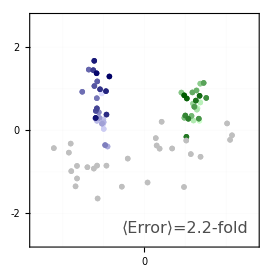

```mathematica
createLandscape[{coordsVirusStem,coordsAbStem},"Tooltip"->True,"ErrorLabel"->"⟨Error⟩=","ErrorValue"->landscapeError,"LabelColor"->GrayLevel[0.3]]
```

#### Panel D: Examples for an Antibody and Virus

A deeper look into how one virus (H1N1 A/Michigan/45/2015) and one antibody (315-23-1C09) are positioned on the map. Each IC_50 measurement is represented by a red circle with radius r=log_10(IC_50/(10^-10 Molar)), and an antibody or virus must lie as close to all of these circles as possible. For clarity, we only show a small number of the measurements used to constrain their positions.

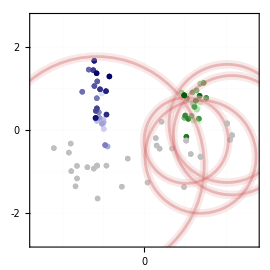
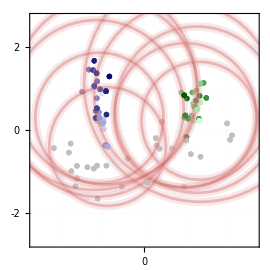

```mathematica
Block[{extraViruses={},virusOfInterest,antibodyOfInterest,coords,showEntries},
(* Emphasize a virus or antibody *)
If[MemberQ[labelVirus,#],
{virusOfInterest,antibodyOfInterest,coords}={#,None,coordsAbStem},
{virusOfInterest,antibodyOfInterest,coords}={None,#,coordsVirusStem}
];
Show[
(* Show all entries on landscape with small opacity *)
createLandscape[{coordsVirusStem,coordsAbStem},"MarkerVirusOpacity"->0.02,"MarkerAbOpacity"->0.1],
(* Entries whose Subscript[IC, 50] s are shown as red circles *)
showEntries=Cases[Replace[If[virusOfInterest=!=None,Table[{antibody,data[virusOfInterest,antibody]},{antibody,labelAbStem}],Table[{virus,data[virus,antibodyOfInterest]},{virus,labelVirus}]],{val:(_Real|_Integer):>Log[10,val/10^-10]},{2}],{Switch[#,
"H1N1 A/Michigan/45/2015","315-02-1H01"|"315-53-1A09"|"CR6261"|"CR9114"|"55-1D06",
"315-23-1C09","H1N1 A/Weiss/1943"|"H1N1 A/USSR/90/1977"|"H1N1 A/Beijing/262/1995"|"H1N1 A/California/07/2009"|"H1N1 A/Michigan/45/2015"|"H3N2 A/Colorado/2/1986"|"H3N2 A/Sichuan/2/1987"|"H3N2 A/Brisbane/10/2007"|"H3N2 A/Victoria/361/2011"|"H3N2 A/Singapore/INFIMH-160019/2016"],_}];
Graphics[{Opacity[0.3],{{Lighter[colorAbDecomposition,0.6],Thickness[0.0225],Circle[coords@#[[1]],#[[2]]]},{colorAbDecomposition,Thickness[0.0075],Circle[coords@#[[1]],#[[2]]]}}&/@showEntries}],createLandscape[If[virusOfInterest=!=None,{Association[],KeySelect[coordsAbStem,MatchQ[#,Alternatives@@First/@showEntries]&]},{KeySelect[coordsVirusStem,MatchQ[#,Alternatives@@Join[First/@showEntries,extraViruses]]&],Association[]}],"Tooltip"->True],
(* Antibody or virus of interest *)
If[virusOfInterest=!=None,ListPlot[{coordsVirusStem@virusOfInterest},PlotMarkers->markerVirus[0.13,"OpacityFaceFormFactor"->1],PlotStyle->plotStyleVirus@virusOfInterest],ListPlot[{coordsAbStem@antibodyOfInterest},PlotMarkers->markerAb[0.13],PlotStyle->colorAbInMixture]],FrameTicksStyle->22]
]&/@{"H1N1 A/Michigan/45/2015","315-23-1C09"}
```

### Figure 2: Quantifying the Spectrum of mAb Behavior

Once the positions of antibodies or viruses are determined on the landscape, additional entries can be rapidly added by using a few measurements to triangulate their coordinates and then predict their behavior against all other mapped entries. Currently, this implies that 6 antibody measurements can provide ~45 predictions; as the number of antibodies and viruses on the landscape grows, this predictive power will grow correspondingly.

```mathematica
resLeaveOneOutAntibody=;
resLeaveMultiOutAntibody=;
resLeaveOneOutVirus=;
resLeaveMultiOutVirus=;
```

#### Canned: Leave-One-Out Analysis

Removing 1 antibody

```mathematica
resLeaveOneOutAntibody=Association@Table[
PrintTemporary[Row[{"Removing antibody: ",leftOutAb}]];
PrintTemporary[runMDS[DeleteCases[labelAbStem,leftOutAb],labelVirus,"SearchPoints"->50]];
leftOutAb->{coordsVirus,coordsAb}
,{leftOutAb,labelAbStem}];
Iconize[resLeaveOneOutAntibody,"Leave-One-Out: Antibody MDS",Method->Compress]
```

Removing 10 antibodies from either the left- or right-half of the landscape to empty out a region on the plot, which should be a difficult test!

```mathematica
(*Grid[{{Show[mapStem,ListPlot[Values@SortBy[coordsAbStem,First][[;;10]],PlotMarkers->markerAb[0.115]]],Show[mapStem,ListPlot[Values@KeyDrop[ReverseSortBy[coordsAbStem,First][[;;13]],{"MEDI8852","CR9114","02-1B02"}],PlotMarkers->markerAb[0.115]]]}}]*)
```

```mathematica
resLeaveMultiOutAntibody=Association@Table[
PrintTemporary[Row[{"Removing antibodies: ",leftOutAntibodies}]];
PrintTemporary[runMDS[DeleteCases[labelAbStem,Alternatives@@leftOutAntibodies],labelVirus,"SearchPoints"->50]];
leftOutAntibodies->{coordsVirus,coordsAb}
,{leftOutAntibodies,{Keys@SortBy[coordsAbStem,First][[;;10]],Keys@KeyDrop[ReverseSortBy[coordsAbStem,First][[;;13]],{"MEDI8852","CR9114","02-1B02"}]}}];
Iconize[resLeaveMultiOutAntibody,"Leave-Multi-Out: Antibody MDS",Method->Compress]
```

Removing 1 virus at a time

```mathematica
resLeaveOneOutVirus=Association@Table[
PrintTemporary[Row[{"Removing virus: ",leftOutVirus}]];
PrintTemporary[runMDS[labelAbStem,DeleteCases[labelVirus,leftOutVirus],"SearchPoints"->50]];
leftOutVirus->{coordsVirus,coordsAb}
,{leftOutVirus,labelVirus[[;;]]}]
Iconize[resLeaveOneOutVirus,"Leave-One-Out: Virus MDS",Method->Compress]
```

Removing 10 viruses from the last 10 years (2010-2019)

```mathematica
resLeaveMultiOutVirus=Association@Table[
PrintTemporary[Row[{"Removing viruses: ",leftOutViruses}]];
PrintTemporary[runMDS[labelAbStem,DeleteCases[labelVirus,Alternatives@@leftOutViruses],"SearchPoints"->50]];
leftOutViruses->{coordsVirus,coordsAb}
,{leftOutViruses,{Cases[labelVirus,virus_/;virusYear@virus≥2010]}}];
Iconize[resLeaveMultiOutVirus,"Leave-Multi-Out: Virus MDS",Method->Compress]
```

#### Panel A: Example of Triangulation

To test the predictive power of a new antibody not used for the MDS, we withhold one antibody from our dataset and recreate the landscape. On the new landscape, we triangulate the antibody using 6 neutralization measurements, and then predict the remaining 45 measurements.

For visualization purposes, all landscapes are oriented as closely as possible to the Neutralization Landscape in Figure 1C (using translations, rotations, and reflections).

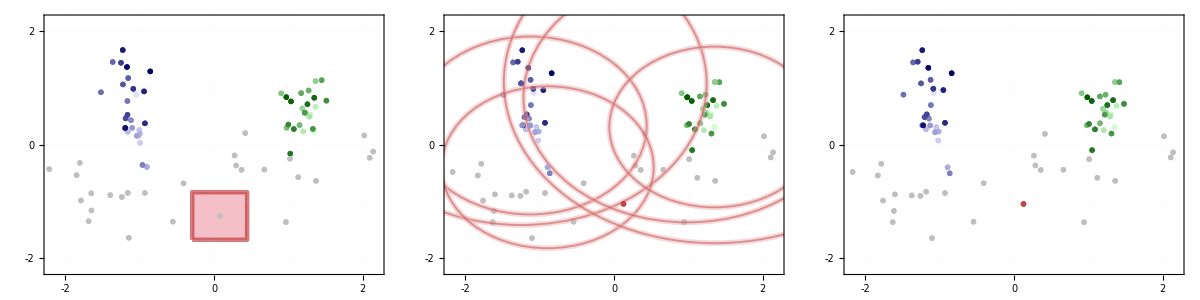

```mathematica
Block[{coordsVirus,coordsAb,
(* Antibody to withhold *)
leftOutAb="315-23-1C09",
(* Viruses used to triangulate the withheld antibody *)
virusSubset={"H3N2 A/Brisbane/10/2007","H3N2 A/Sichuan/2/1987","H3N2 A/Colorado/2/1986","H1N1 A/Weiss/1943","H1N1 A/Michigan/45/2015","H1N1 A/Beijing/262/1995"},boxSize={0.37,0.42},plotRange=2.2{{-1,1},{-1,1}},frameTicksStyle=20},
(* MDS results after withholding antibody *)
{coordsVirus,coordsAb}=resLeaveOneOutAntibody[leftOutAb];
(* Show the original landscape with the withheld antibody boxed *)
mapA=Show[createLandscape[{coordsVirusStem,Delete[coordsAbStem,Key[leftOutAb]]},"MarkerVirusSize"->0.13,"MarkerVirusOpacity"->1],Graphics[{EdgeForm[{Thickness[0.012],RGBColor[Rational[2, 3], 0, 0, 0.5]}],FaceForm[RGBColor[0.93, 0.504, 0.5733, 0.5]],Rectangle[coordsAbStem@leftOutAb-boxSize,coordsAbStem@leftOutAb+boxSize]}],ListPlot[{coordsAbStem@leftOutAb},PlotMarkers->markerAb[0.15],PlotStyle->colorAbInMixture],PlotRange->plotRange,FrameTicksStyle->frameTicksStyle];
(* On the new landscape, triangulate the withheld antibody using 6 measurements *)
mapB=Show[triangulate[virusSubset,leftOutAb,{coordsVirus,coordsAb},"ShowMap"->True]/.{
(* Red circles *)Opacity[0.8]->Opacity[0.5]
},PlotRange->plotRange,FrameTicksStyle->frameTicksStyle];
(* We can now predict the antibody's interaction with the remaining 45 viruses *)
mapC=Show[createLandscape[{coordsVirus,coordsAb},"MarkerVirusSize"->0.13,"MarkerVirusOpacity"->1,"MarkerAbOpacity"->0.05],ListPlot[{newCoord},PlotMarkers->markerAb[0.15],PlotStyle->colorAbDecomposition],PlotRange->plotRange,FrameTicksStyle->frameTicksStyle];
(* Plotting *)
Grid[{{mapA,mapB,mapC}}]
]
```

#### Panel B: Summary Statistics for Ab Triangulation

This algorithm was carried out for all 27 stem antibodies, predicting 623 antibody-virus neutralization measurements.

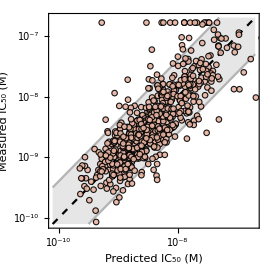

Fraction within 2x:  0.65

Fraction within 4x:  0.9

```mathematica
(* Individual Subscript[IC, 50] s predicted via triangulation versus measured values *)
predictedMeasuredIC50s=Table[
triangulate[virusSubset,antibodyOfInterest,resLeaveOneOutAntibody@antibodyOfInterest,"ReturnFoldError"->False]
,{antibodyOfInterest,labelAbStem},{virusSubset,selectSubset[antibodyOfInterest,resLeaveOneOutAntibody@antibodyOfInterest,6]}];
(* Plotting *)
Show[Plot[{x,4x,x/4},{x,10^-10.1,10^-6.7},],
ListPlot[First/@DeleteCases[predictedMeasuredIC50s,{},{2}],]]
(* Fraction of measurements within 2x or 4x *)
Echo[Round[(Length@Cases[#,entry_/;foldError@entry≤2.])/(Length@#),0.01]&[Flatten[First/@predictedMeasuredIC50s,1]],"Fraction within 2x:"];
Echo[Round[(Length@Cases[#,entry_/;foldError@entry≤4.])/(Length@#),0.01]&[Flatten[First/@predictedMeasuredIC50s,1]],"Fraction within 4x:"];
```

#### Panel C: Leave-Out-Virus and Leave-Multi-Out

We repeated this procedure withholding 1 antibody, 10 antibodies, 1 virus, and 10 viruses

The distributions in this panel show the average results from numSubsets=15 different choices of the viruses/antibodies used for triangulation (to ensure that one specific choice was not particularly good or bad). Each withheld entry is triangulated using sizeSubset=6 measurements

Because the dynamic range of our experiments goes up to 1.6·10^-7 M, we clip all predictions to lie within the interval (-∞,1.6·10^-7M)

```mathematica
Block[{withheldAntibody,coords,virusSubsets,withheldAntibodies,withheldViruses,antibodySubsets,
(* Specifications for triangulation *)
numSubsets=15,sizeSubset=6
},
(* Withhold 1 antibody *)
plotDataLeaveOneOutAntibody=(
{withheldAntibody,coords}=#;
virusSubsets=selectSubset[withheldAntibody,coords,sizeSubset,numSubsets];
triangulate[#,withheldAntibody,coords,"ReturnFoldError"->False]&/@virusSubsets
)&/@KeyValueMap[List,resLeaveOneOutAntibody];
plotDataLeaveOneOutAntibody=Flatten@Map[foldError,Clip[Join@@plotDataLeaveOneOutAntibody,{-∞,1.65 10^-7}],{2}];
(* Withhold 10 antibodies *)
plotDataLeaveMultiOutAntibodies=(
{withheldAntibodies,coords}=#;
Table[
virusSubsets=selectSubset[leftOutAntibody,coords,sizeSubset,numSubsets];
triangulate[#,leftOutAntibody,coords,"ReturnFoldError"->False]&/@virusSubsets
,{leftOutAntibody,withheldAntibodies}]
)&/@KeyValueMap[List,resLeaveMultiOutAntibody];
plotDataLeaveMultiOutAntibodies=Flatten@Map[foldError,Clip[Join@@plotDataLeaveMultiOutAntibodies,{-∞,1.65 10^-7}],{3}];
(* Withhold 1 virus *)
plotDataLeaveOneOutVirus=(
{withheldViruses,coords}=#;
antibodySubsets=selectSubset[withheldViruses,coords,sizeSubset,numSubsets];
triangulate[withheldViruses,#,coords,"ReturnFoldError"->False]&/@antibodySubsets
)&/@KeyValueMap[List,resLeaveOneOutVirus];
plotDataLeaveOneOutVirus=Flatten@Map[foldError,Clip[Join@@plotDataLeaveOneOutVirus,{-∞,1.65 10^-7}],{2}];
(* Withhold 10 viruses *)
plotDataLeaveMultiOutVirus=(
{withheldViruses,coords}=#;
Table[
antibodySubsets=selectSubset[leftOutVirus,coords,sizeSubset,numSubsets];
triangulate[leftOutVirus,#,coords,"ReturnFoldError"->False]&/@antibodySubsets
,{leftOutVirus,withheldViruses}]
)&/@KeyValueMap[List,resLeaveMultiOutVirus];
plotDataLeaveMultiOutVirus=Flatten@Map[foldError,Clip[Join@@plotDataLeaveMultiOutVirus,{-∞,1.65 10^-7}],{3}];
]
(* Plotting *)
DistributionChart[{{plotDataLeaveOneOutAntibody,plotDataLeaveMultiOutAntibodies,plotDataLeaveOneOutVirus,plotDataLeaveMultiOutVirus}},]
(* Fraction of measurements within 2x or 4x *)
Echo[Round[(Length@Cases[#,entry_/;entry≤2.])/(Length@#),0.01]&/@{plotDataLeaveOneOutAntibody,plotDataLeaveMultiOutAntibodies,plotDataLeaveOneOutVirus,plotDataLeaveMultiOutVirus},"Fraction of measurements within 2x:"];
Echo[Round[(Length@Cases[#,entry_/;entry≤4.])/(Length@#),0.01]&/@{plotDataLeaveOneOutAntibody,plotDataLeaveMultiOutAntibodies,plotDataLeaveOneOutVirus,plotDataLeaveMultiOutVirus},"Fraction of measurements within 4x:"];
```

-Graphics-

Fraction of measurements within 2x:  {0.61,0.5,0.58,0.5}

Fraction of measurements within 4x:  {0.88,0.78,0.85,0.78}

### Figure 3: Tradeoff between Potency and Breadth

What is the smallest enclosing circle all of the H1N1 and H3N2 vaccine strains from the 2004-05 season to 2018-19 seasons?

H3N2 vaccine strains: A/Fujian/411/2002, A/California/07/2004, A/Wisconsin/67/2005, A/Brisbane/10/2007, A/Perth/16/2009, A/Victoria/361/2011, A/Texas/50/2012, A/Switzerland/9715293/2013, A/Hong Kong/4801/2014, and A/Singapore/INFIMH-160019/2016

H1N1 vaccine strains: A/New Caledonia/20/1999, A/Solomon Islands/03/2006, A/Brisbane/59/2007, A/California/07/2009, and A/Michigan/45/2015

All of these viruses are included in our virus panel except H1N1 A/Brisbane/59/2007, which we substituted with A/New York/08-1326/2008 (whose HA sequence only differs by 2 amino acids)

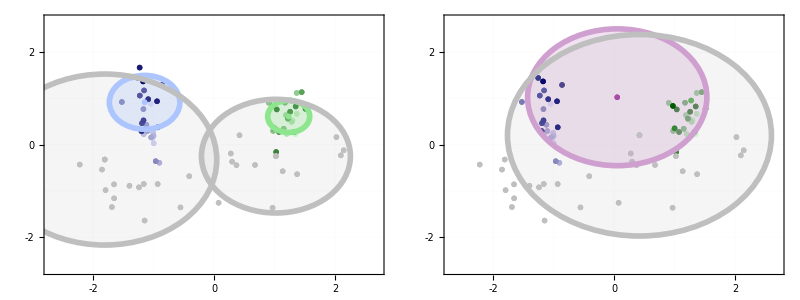

```mathematica
Block[{colorH1N1=RGBColor[0.5544, 0.9, 0.5544],colorH3N2=RGBColor[0.6733333333333333, 0.7733333333333333, 1.],colorBoth=RGBColor[0.8133333333333334, 0.6266666666666667, 0.8133333333333334],opacity=Opacity[0.15],opacity2=Opacity[0.3],thickness=Thickness[0.015],frameTicksStyle=22,sizeAb=0.15,sizeVirus=0.13,
(* H1N1 vaccine strains *)
virusSubsetH1N1={"H1N1 A/New Caledonia/20/1999","H1N1 A/Solomon Islands/03/2006","H1N1 A/New York/08-1326/2008","H1N1 A/California/07/2009","H1N1 A/Michigan/45/2015"},
(* H3N2 vaccine strains *)
virusSubsetH3N2={"H3N2 A/Fujian/411/2002","H3N2 A/California/07/2004","H3N2 A/Wisconsin/67/2005","H3N2 A/Brisbane/10/2007","H3N2 A/Perth/16/2009","H3N2 A/Victoria/361/2011","H3N2 A/Texas/50/2012","H3N2 A/Switzerland/9715293/2013","H3N2 A/Hong Kong/4801/2014","H3N2 A/Singapore/INFIMH-160019/2016"},
virusSubset,coordsH1N1,minBoundingCircleH1N1,bestAbTheoreticalH1N1,bestAbMeasuredH1N1,coordsH3N2,minBoundingCircleH3N2,bestAbTheoreticalH3N2,bestAbMeasuredH3N2,mapWithinSubtypes,coords,minBoundingCircle,bestAbTheoretical,bestAbMeasured,mapAcrossSubtypes
},
virusSubset=Join[virusSubsetH1N1,virusSubsetH3N2];
(* Best theroetical and measured antibody against each virus subset *)
coordsH1N1=coordsVirusStem/@virusSubsetH1N1;
minBoundingCircleH1N1=BoundingRegion[coordsH1N1,"MinDisk"];
bestAbTheoreticalH1N1=First@minBoundingCircleH1N1;
bestAbMeasuredH1N1=First@SortBy[labelAbStem,Max@DeleteMissing[Table[data[virus,#],{virus,virusSubsetH1N1}]/.GreaterThan[val_]:>val]&];
coordsH3N2=coordsVirusStem/@virusSubsetH3N2;
minBoundingCircleH3N2=BoundingRegion[coordsH3N2,"MinDisk"];
bestAbTheoreticalH3N2=First@minBoundingCircleH3N2;
bestAbMeasuredH3N2=First@SortBy[labelAbStem,Max@DeleteMissing[Table[data[virus,#],{virus,virusSubsetH3N2}]/.GreaterThan[val_]:>val]&];
(* Plotting *)
mapWithinSubtypes=Show[createLandscape[{KeySelect[coordsVirusStem,!MemberQ[Join[virusSubsetH1N1,virusSubsetH3N2],#]&],coordsAbStem},"MarkerAbOpacity"->0.04,"MarkerVirusOpacity"->0.02],Graphics[{FaceForm[{opacity2,colorH1N1}],minBoundingCircleH1N1,FaceForm[{opacity2,colorH3N2}],minBoundingCircleH3N2,FaceForm[{opacity,colorAbInMixture}],Disk[coordsAbStem@bestAbMeasuredH1N1,10+Log10@Max@Table[10^(-10+Norm[coordsAbStem@bestAbMeasuredH1N1-coordsVirusStem@virus]),{virus,virusSubsetH1N1}]],Disk[coordsAbStem@bestAbMeasuredH3N2,10+Log10@Max@Table[10^(-10+Norm[coordsAbStem@bestAbMeasuredH3N2-coordsVirusStem@virus]),{virus,virusSubsetH3N2}]]}],ListPlot[List/@coordsVirusStem/@Join[virusSubsetH1N1,virusSubsetH3N2],PlotMarkers->markerVirus[sizeVirus],PlotStyle->plotStyleVirus/@Join[virusSubsetH1N1,virusSubsetH3N2]],Graphics[{FaceForm[],EdgeForm[{thickness,colorH1N1}],minBoundingCircleH1N1,EdgeForm[{thickness,colorH3N2}],minBoundingCircleH3N2,EdgeForm[{thickness,colorAbInMixture}],Disk[coordsAbStem@bestAbMeasuredH1N1,10+Log10@Max@Table[10^(-10+Norm[coordsAbStem@bestAbMeasuredH1N1-coordsVirusStem@virus]),{virus,virusSubsetH1N1}]],Disk[coordsAbStem@bestAbMeasuredH3N2,10+Log10@Max@Table[10^(-10+Norm[coordsAbStem@bestAbMeasuredH3N2-coordsVirusStem@virus]),{virus,virusSubsetH3N2}]]}],ListPlot[List/@{bestAbTheoreticalH3N2,bestAbTheoreticalH1N1,coordsAbStem@bestAbMeasuredH3N2,coordsAbStem@bestAbMeasuredH1N1},PlotMarkers->markerAb[sizeAb],PlotStyle->{colorH3N2,colorH1N1,colorAbInMixture,colorAbInMixture}],FrameTicksStyle->frameTicksStyle];

(* Best theroetical and measured antibody against both virus subsets *)
coords=coordsVirusStem/@virusSubset;
minBoundingCircle=BoundingRegion[coords,"MinDisk"];
bestAbTheoretical=First@minBoundingCircle;
bestAbMeasured=First@SortBy[labelAbStem,Max@DeleteMissing[Table[data[virus,#],{virus,virusSubset}]/.GreaterThan[val_]:>val]&];
(* Plotting *)
mapAcrossSubtypes=Show[createLandscape[{KeySelect[coordsVirusStem,!MemberQ[virusSubset,#]&],coordsAbStem},"MarkerAbOpacity"->0.04,"MarkerVirusOpacity"->0.02],Graphics[{FaceForm[{opacity2,colorBoth}],minBoundingCircle,FaceForm[{opacity,colorAbInMixture}],Disk[coordsAbStem@bestAbMeasured,10+Log10@Max@Table[10^(-10+Norm[coordsAbStem@bestAbMeasured-coordsVirusStem@virus]),{virus,virusSubset}]]}],ListPlot[List/@coordsVirusStem/@virusSubset,PlotMarkers->markerVirus[sizeVirus],PlotStyle->plotStyleVirus/@virusSubset],Graphics[{FaceForm[],EdgeForm[{thickness,colorBoth}],minBoundingCircle,EdgeForm[{thickness,colorAbInMixture}],Disk[coordsAbStem@bestAbMeasured,10+Log10@Max@Table[10^(-10+Norm[coordsAbStem@bestAbMeasured-coordsVirusStem@virus]),{virus,virusSubset}]]}],ListPlot[List/@{bestAbTheoretical,coordsAbStem@bestAbMeasured},PlotMarkers->markerAb[sizeAb],PlotStyle->{RGBColor[0.65, 0.3, 0.65],colorAbInMixture}],FrameTicksStyle->frameTicksStyle];
Grid[{{mapWithinSubtypes,mapAcrossSubtypes}}]
]
```

### Figure 4: Head+Stem Antibody Mixtures

By defining the range of all possible stem antibody behavior, we can also detect and computationally remove any non-stem behavior. In particular, we can create antibody mixtures containing both HA head and HA stem antibodies, and use their collective neutralization to characterize just the stem antibody within.

#### Panel C: Removing Head Neutralization

We demonstrate an example decomposition for a mixture containing (1 head antibody + 1 stem antibody). In the left panel, we show the original measurements for this mixture, where red circles represent concrete IC_50 values while gold disks represent measurements outside out dynamic range (IC_50>1.6·10^-7M). Although this mixture contains 1 stem antibody, we cannot determine its location because the of the head neutralization. Geometrically, there is no single point that lies on all the red circles while simultaneously being outside the gold disks.

The right panel shows what happens when we computationally remove the head neutralization signal. The neutralization from all the blue H3N2 viruses are now given as lower bounds, since we correctly detected that the head antibody was causing their neutralization patterns. As a result, we can now predict the behavior of the stem antibody (red) and compare it to the true location of the stem antibody (gray, inferred from this antibody’s individual neutralization measurements that we did not access during the decomposition).

The head neutralization is removed by looking at each pair of viruses and comparing whether the difference between their neutralization (see SI section Removing Head Antibody Neutralization). More precisely, if two viruses are separated by d_(V1-V2) on the map, and their IC_50s differ by more than 10·10^(d_(V1-V2)), then we increase the smaller value IC_50^(min)→≥IC_50^(max)/(10·10^(d_(V1-V2))). Thus, the smaller IC_50 (caused by an HA head antibody) is increased and changed to a lower bound. The factor 10^(d_(V1-V2)) quantifies the theoretical maximum discrepancy between neutralization for two viruses lying a distance d_(V1-V2) apart, while the prefactor of 10 adds extra leniency to account for noise in the assay, so that we only alter measurements when we see a substantial non-HA-stem signal

The gold disks show IC_50 values bounded from below (for example, a value of ≥10^-8 M corresponds to a disk with radius Log_10[(10^-8 M)/(10^-10 M)]=2). The red disks represent concrete IC_50 values (for example, a value of 10^-8.5 M corresponds to a circle with radius Log_10[(10^-8.5 M)/(10^-10 M)]=1.5)

We remove the head neutralization using measurements against the full H1N1 and H3N2 panel. For simplicity, we just show the resulting changes to a subset of viruses. (If we only considered this subset of measurements when removing the head neutralization, the results would have been slightly different, since we would not have as many virus pairs to constrain the neutralization measurements.)

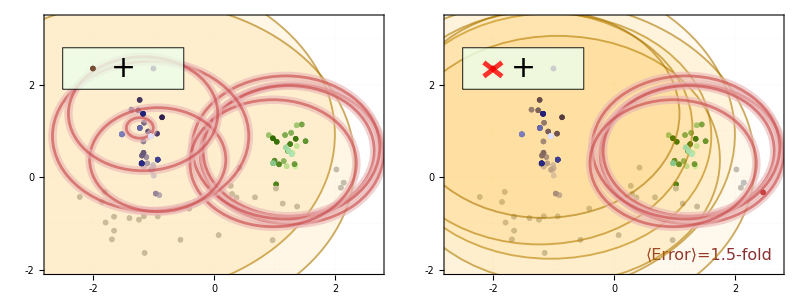

```mathematica
Block[{antibody=orderedMixtures[[7]],pnt1={-2.5,1.8+0.1},pnt2={-0.5,2.7+0.1},offset={-0.15,-0.15},offset2={0,-0.02},mean,virusesGreaterThan,opacity,plotError,virusesMeasuredH1N1,virusesMeasuredH3N2,virusesMeasured,dataOriginal,dataSmoothed,index,virusesGreaterThanOriginal,virusesGreaterThanSmoothed,plotOriginal,plotSmoothed,showEntries,ab1},
(* Error to show for the decomposition (including all viruses, not just the ones shown) *)
decomposeSerum[orderedMixtures[[7]],1,labelVirus,"RemoveHeadAbSignal"->True,"ShowMap"->False];
plotError=mapError;
(* Viruses measured against the antibody mixture *)
virusesMeasuredH1N1=Cases[labelVirusH1N1,virus_/;!MissingQ@data[virus,antibody]];
virusesMeasuredH3N2=Cases[labelVirusH3N2,virus_/;!MissingQ@data[virus,antibody]];
virusesMeasured=Join[virusesMeasuredH1N1,virusesMeasuredH3N2];
(* Combine the raw data with the Neutralization Landscape to remove the head antibody signal *)
dataOriginal=Table[data[virus,antibody],{virus,virusesMeasured}];
dataSmoothed=removeHeadAbSignal[dataOriginal,virusesMeasured];
(* After removing the head antibody, compute the coordinate of the predicted stem antibody *)
decomposeSerum[antibody,1,virusesMeasured,"RemoveHeadAbSignal"->True,"Show50%Neutralization"->False,"ErrorFontSize"->20,"EpilogLabelPosition"->{2.6,-2.},"PlotMarkerAntibody"->markerAb[0.15],PlotRange->{2.7{-1,1},2.7{-1,1}+0.3}];
(* Show a subset of viruses *)
index={5,6,7,10,18,30,32,37,38,39};
(* Highlight viruses with GreaterThan IC50s with a glow *)
virusesGreaterThanOriginal=virusesMeasured[[Cases[index,val_/;MatchQ[dataOriginal[[val]],_GreaterThan]]]];
virusesGreaterThanSmoothed=virusesMeasured[[Cases[index,val_/;MatchQ[dataSmoothed[[val]],_GreaterThan]]]][[(* Draw Sydney 1997 on top *){1,3,4,5,6,2}]];
(* Plotting *)
mean=Mean[{pnt1,pnt2}];
{plotOriginal,plotSmoothed}=MapIndexed[(
virusesGreaterThan=If[First@#2==1,virusesGreaterThanOriginal,virusesGreaterThanSmoothed];
opacity=If[First@#2==1,0.1,0.07];
Show[createLandscape[{coordsVirusStem,coordsAbStem},PlotRange->{2.7{-1,1},{-2.,3.4}},"MarkerAbOpacity"->0.05,"MarkerVirusOpacity"->0.02,Sequence@@If[First@#2==2,{"ErrorValue"->plotError,"ErrorLabel"->"⟨Error⟩=","LabelPosition"->{2.62,-1.69}},{}]],
(* Gold disks of exclusion around all GreaterThan values *)
showEntries=Replace[Transpose@{virusesMeasured[[index]],#},{val:(_Real|_Integer):>Log[10,val/10^-10]},{2,3}];
Graphics[{Opacity[opacity],EdgeForm[{Opacity[0.6],Thickness[0.005],Darker@RGBColor[1, 0.6900000000000001, 0]}],RGBColor[1, 0.6900000000000001, 0],Disk[coordsVirusStem@#[[1]],#[[2]]]}&/@Cases[showEntries,{virus_,GreaterThan[val_]}:>{virus,val}]],
(* Red circles around each concrete Subscript[IC, 50] value *)
Graphics[{Opacity[0.6],{{Lighter[colorAbDecomposition,0.6],Thickness[1.5 0.015],Circle[coordsVirusStem@#[[1]],Clip[#[[2]],{0.01,∞}]]},colorAbDecomposition,Thickness[1.5 0.005],Circle[coordsVirusStem@#[[1]],Clip[#[[2]],{0.01,∞}]]}&/@Cases[showEntries,{virus_,Except[_GreaterThan]}]}],
(* Subset of viruses with concrete Subscript[IC, 50] s *)
ListPlot[List/@coordsVirusStem/@virusesMeasured[[index]],PlotMarkers->markerVirus["Opacity"->1,"OpacityFaceFormFactor"->1],PlotStyle->(Lighter[plotStyleVirus@#,0.1]&/@virusesMeasured[[index]])],
(* Subset of viruses with Subscript[IC, 50] s given as GreaterThan values *)
ListPlot[List/@coordsVirusStem/@virusesGreaterThan,PlotMarkers->markerVirus[0.13,"Opacity"->1,"OpacityFaceFormFactor"->1,"GlowColor"->Directive[Darker[colorAbDecompositionCombined,0.15],Thickness[0.12]]],PlotStyle->(Lighter[plotStyleVirus@#,0.1]&/@virusesGreaterThan)],
(* Plot the predicted and actual location of the stem antibody *)
If[First@#2==2,ListPlot[{coordsAbStem/@antibody[[-1]],mixtureAbCoord},PlotMarkers->markerAb[0.13],PlotStyle->{colorAbInMixture,colorAbDecomposition}],{}],
(* Legend at the top-left *)
Graphics[{{EdgeForm[Black],Lighter@LightGreen,Opacity[0.8],Rectangle[pnt1,pnt2,RoundingRadius->0.1]},Text[font["+",30],mean]}],ListPlot[{{ab1={-2,Last[mean]}},{{-1,Last[mean]}}},PlotMarkers->markerAb["Thickness"->0.01],PlotStyle->{RGBColor[0.4549020823970525, 0.3058815906405108, 0.19999958424451392],GrayLevel[0.8]}],
If[First@#2==1,{},Graphics[{Red,Opacity[0.8],Thickness[0.013],Line[{{ab1+offset2-offset,ab1+offset2+offset},{ab1+offset2-{1,-1}offset,ab1+offset2+{1,-1}offset}}]}]],FrameTicksStyle->22]/.Opacity[0.7]->Opacity[1]
)&,{dataOriginal,dataSmoothed}[[All,index]]];
Grid[{{plotOriginal,plotSmoothed}}]
]
```

#### Panel D: Two More Example Decompositions

We apply this decomposition to two additional mixtures containing (1 head + 1 stem, mixture #1) or (2 head + 1 stem, mixture #12).

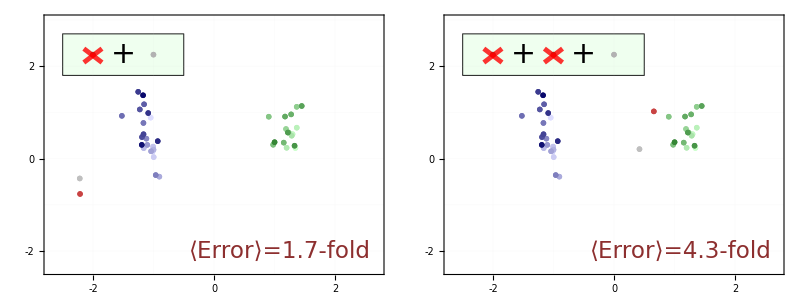

```mathematica
Block[{xMin=-2.5,xMax,yMin=1.8,yMax=2.7,coordX,coordY,posAbs,offset={-0.15,-0.15}},
Grid[{
Table[
(* Remove head neutralization and characterize the stem antibody *)
Show[decomposeSerum[mixture,1,labelVirus,"RemoveHeadAbSignal"->True,"Show50%Neutralization"->False,"ErrorFontSize"->23,"EpilogLabelPosition"->{2.6,-2.},"PlotMarkerAntibody"->markerAb[0.15],PlotRange->{2.7{-1,1},2.7{-1,1}+0.3},FrameTicksStyle->22],
(* Legend in the top-left *)
xMax=xMin+Length@Flatten@mixture;
coordX=Subdivide[xMin,xMax,2Length@Flatten@mixture];
coordY=Mean[{yMin,yMax}];
posAbs=Thread[{coordX[[2;;-2;;2]],coordY}];Graphics[{{EdgeForm[Black],Lighter@LightGreen,Opacity[0.8],Rectangle[{xMin,yMin},{xMax,yMax},RoundingRadius->0.1]},Text[font["+",30],#]&/@Thread[{coordX[[3;;-3;;2]],coordY}]}],ListPlot[List/@posAbs,PlotMarkers->markerAb[],PlotStyle->Join[ConstantArray[RGBColor[0.4549020823970525, 0.3058815906405108, 0.19999958424451392],Length@First@mixture],ConstantArray[RGBColor[0.6980392002989493, 0.698038666521795, 0.6980383860654681],Length@Last@mixture]]],Graphics[{Red,Opacity[0.8],Thickness[0.013],Line[{{#-offset,#+offset},{#-{1,-1}offset,#+{1,-1}offset}}]&/@(#+{0,-0.02}&/@posAbs[[;;Length@First@mixture]])}]]
,{mixture,orderedMixtures[[{1,12}]]}
]}]
]
```

### Figure 5: Stem+Stem Antibody Mixtures

Using the positions of each virus [Figure 1C], we can take a mixture’s neutralization data and infer the number of stem antibodies within as well as their stoichiometry and individual neutralization properties (i.e. their locations on these maps). We call this process a decomposition, since it takes the net neutralization of multiple antibodies and teases apart their individual behavior. We visualize the results by drawing the locations of the actual antibodies in the mixture in gray and the predicted antibodies from the decomposition in red.

#### Panel B: Predicted vs Measured Mixture IC50

We test how well the neutralization of each individual antibody predicts the combined neutralization of a mixture. We assume a competitive binding model, where all antibodies inhibit one another’s binding (i.e. no two antibodies can be simultaneously bound).

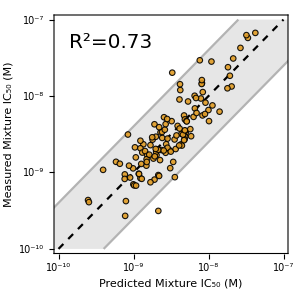

```mathematica
(* Increase all lower bound measurements (Subscript[IC, 50]>1.65·10^-7 M) to Subscript[IC, 50]≈10^-5 M *)
plotData=DeleteMissing[Join@@Table[{data[virus,#]&/@Flatten@antibodyMixture,data[virus,antibodyMixture]},{virus,labelVirus},{antibodyMixture,mixtures2AbStem}],1,All]/._GreaterThan:>10^-5.;
(* Combined neutralization assuming that all antibodies in a mixture compete for the same binding site. The Length argument in front accounts for the fact that each antibody is at 1/2 concentration in a 2-antibody mixture *)
plotData={predictionCompetitive[#[[1]],1./(Length@#[[1]])],#[[2]]}&/@plotData;
(* Once the mixture neutralizations have been determined, clip decrease values outside our dynamic range (Subscript[IC, 50]^mixture>1.65·10^-7 M) to this lower bound *)
plotData=Clip[plotData,{0,1.65 10^-7}];
(* Plotting *)
Block[{meanError=4},
Show[Plot[{x,meanError x,x/meanError},{x,10^-11.3,10^-6},Epilog->{Text[font[Row[{"R^2=",format[rSquared@Log10@plotData,2]}],20],Log@{10^-9.3,10^-7.3}]},],ListPlot[plotData,ScalingFunctions->{"Log","Log"},PlotMarkers->plotMarker[0.035,0.9],PlotStyle->ColorData[97][2]]]
]
```

#### Panel C: Mixtures on the Landscape

We can visualize the competitive binding model on our map by considering a mixture with two antibodies with a 50%/50% composition. We outline the regions inside which any virus will be ≥50% at different concentrations of antibody. Compared to each antibody’s individual neutralization (dashed circles), a mixture’s collective neutralization occurs over a larger region.

The legend gives the concentration of each antibody. For example, when each antibody has a concentration of 10^-9 M (so the mixture has a total antibody concentration of 2·10^-9M), the region of ≥50% neutralization will be roughly a circle of radius 1 around each antibody

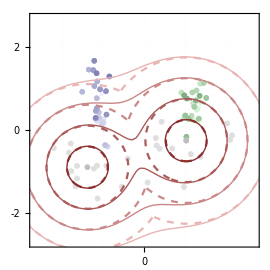
-Graphics- |

```mathematica
Block[{Ab1,Ab2,antibodyOfInterest=orderedMixtures[[10,-1]],colors=Blend[{Darker[colorAbDecomposition,0.3],Lighter[colorAbDecomposition,0.6]},#]&/@Subdivide[3],
(* Show regions of ≥50% neutraliation when both antibodies are at the following concentrations *)
cutOffs=10^Range[-9.5,-8,0.5]},
{Ab1,Ab2}=coordsAbStem/@antibodyOfInterest;
Grid[{{Show[
(* Neutralization landscape *)
createLandscape[{coordsVirusStem,coordsAbStem},"MarkerAbOpacity"->0.1,"MarkerVirusOpacity"->0.6],
Graphics[{Opacity[0.5],White,Rectangle[2.7{-1,-1},2.7{1,1}]}],
(* Antibodies in mixture *)
ListPlot[{{Ab1,Ab2}},PlotMarkers->markerAb[],PlotStyle->colorAbInMixture],
(* Regions of ≥50% virus neutralization *)
ContourPlot[Evaluate[Join@@({predictionCompetitive[{10^(-10.+Norm[{x,y}-Ab1]),10^(-10.+Norm[{x,y}-Ab2])},1]==#,Min[{10^(-10.+Norm[{x,y}-Ab1]),10^(-10.+Norm[{x,y}-Ab2])}]==#}&/@cutOffs)],{x,-5,5},{y,-5,5},ContourStyle->Join@@({{Thick,#},{Dashed,#}}&/@colors),PlotPoints->50],FrameTicksStyle->18],LineLegend[colors,font/@{"10^-9.5 M","10^-9.0 M","10^-8.5 M","10^-8.0 M"},LegendFunction->frameOpaque,LegendMarkerSize->12,LegendLabel->Placed[font["Antibody"],Above],Spacings->{0.2,0}]}}]
]
```

#### Panel D: Decomposing a Stem+Stem Mixture

An example of the mixture #9 (stem+stem antibodies, true positions shown in gray) decomposed as two stem antibodies (red).

The circle surrounding each antibody represents the region of the landscape where a virus will be ≥50% neutralized when the total mixture concentration equals 10^-8.5 Molar.

Therefore, the size of the circles correspond to an antibody's stoichiometry. For example, the gray circles both have the same radius, since the true mixture has a 50%/50% composition using these antibodies. Thus, their radius equals 1.5+Log_10[1/2]=1.2, where 1.5 corresponds to the mixture concentration of 10^-8.5 Molar while Log_10[1/2] accounts for the fact that each antibody only comprises half the mixture.

The size of the red circles similarly shows their stoichiometry, with the predicted mixture having a 90%/10% composition for the red antibodies on the left/right. Thus, the left antibody has a circle of radius 1.5+Log_10[9/10]=1.5 while the right antibody has a smaller circle of radius 1.5+Log_10[1/10]=0.5

The two gray circles and the two red circles do not merged together because these antibodies are so far apart on the landscape that they do not interact. Said another way, no virus can be appreciably neutralized by both antibodies, and therefore, the mixture’s behavior is identical to the individual behaviors of the two constituent antibodies added together (similar to the circles in Figure 4C when Antibody=10^-9.5 M, where the dashed and solid lines overlap). In Figure 4F, we see examples where the antibodies are sufficiently close to interact and expand the region of ≥50% neutralization.

Note that although the decomposition did not perfectly predict the positions of the antibodies nor their stoichiometry. However, both of these discrepancies somewhat offset each other, so that the neutralization profile is well-described by either the gray or red antibody mixture. In other words, this exemplifies that neutralization measurements may not uniquely identify an antibody mixture (especially when considering measurement error), and that multiple distinct antibody combinations could give rise to similar neutralization responses.

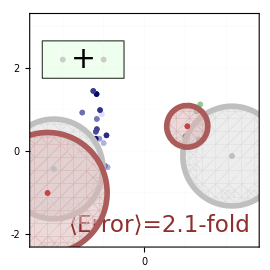

```mathematica
Block[{pnt1,pnt2,mean,offset={0,-0.05}},
pnt1={-2.5,1.8}+offset;
pnt2={-0.5,2.7}+offset;
mean=Mean[{pnt1,pnt2}];
Show[
(* Decomposition of the stem+stem antibody mixture *)
decomposeSerum[orderedMixtures[[8]],Automatic,virusesForDecomp,"RemoveHeadAbSignal"->True,"ErrorFontSize"->23,"EpilogLabelPosition"->{2.6,-1.8},"PlotMarkerAntibody"->markerAb[0.15],"PlotMarkerVirus"->markerVirus[0.13,"Opacity"->0.8,"OpacityFaceFormFactor"->0.9],PlotRange->{2.7{-1,1},2.7{-1,1}+0.5},"Radius"->1.5,"ShowCombinedNeutralization"->True,"RingColor"->Blend[{Darker[colorAbDecomposition,0.3],Lighter[colorAbDecomposition,0.6]},1/3]],
(* Legend in the top-left *)
Graphics[{{EdgeForm[Black],Lighter@LightGreen,Opacity[0.8],Rectangle[pnt1,pnt2,RoundingRadius->0.1]},Text[font["+",30],mean]}],ListPlot[{{{-2,Last@mean}},{{-1,Last@mean}}},PlotMarkers->markerAb["Thickness"->0.01],PlotStyle->{GrayLevel[0.8],GrayLevel[0.8]}]]
]
```

#### Panel E: Statistics for all Antibody Mixtures

Analysis of all 14 antibody mixtures mixtures, stratified by the number of antibodies they contain. A monoclonal antibody is considered to be a "mixture" of 1 antibody.

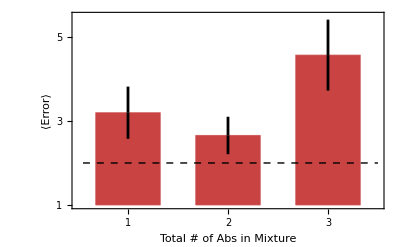

Correct Decompositions for Mixtures with 1, 2, or 3 Antibodies:  {23/27,10/11,3/3}

```mathematica
BarChart[MeanAround[Last@decomposeError[#,virusesForDecomp]&/@Cases[Join[mixtures1AbStem,mixtures2AbStem,mixtures2AbHeadStem,mixtures3AbHeadStem],entry_/;Length[Join@@entry]==#]]&/@Range@3,]/.Rectangle[{a_,0.},b__]:>Rectangle[{a,1.},b]
(* Fraction of decompositions with the correct # of stem antibodies *)
Echo[Row[{Total@#,"/",Length@#}]&/@Map[Boole[First@decomposeError[#,virusesForDecomp]==Length@Last@#]&,Cases[Join[mixtures1AbStem,mixtures2AbStem,mixtures2AbHeadStem,mixtures3AbHeadStem],entry_/;Length[Join@@entry]==#]&/@Range@3,{2}],"Correct Decompositions for Mixtures with 1, 2, or 3 Antibodies:"];
```

#### Panel F: Two More Example Decompositions

Two additional examples where we decompose either a stem+stem mixture (#10) or a head+stem+stem mixture (#14).

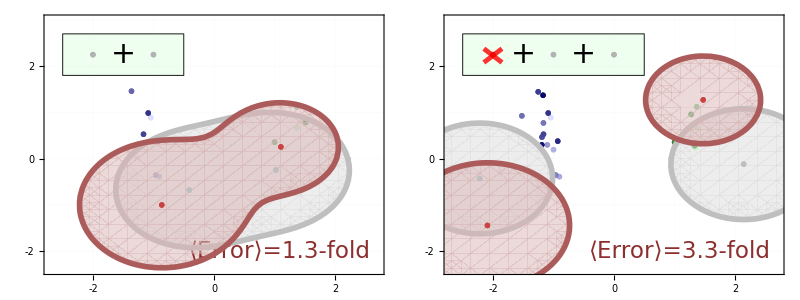

```mathematica
Block[{xMin=-2.5,xMax,yMin=1.8,yMax=2.7,coordX,coordY,posAbs,offset={-0.15,-0.15}},
Grid[{
Table[
Show[
(* Remove head neutralization and characterize the stem antibody mixture *)
decomposeSerum[mixture,Automatic,virusesForDecomp,"RemoveHeadAbSignal"->True,"ErrorFontSize"->23,"EpilogLabelPosition"->{2.6,-2.},"PlotMarkerAntibody"->markerAb[0.15],"PlotMarkerVirus"->markerVirus[0.13,"Opacity"->0.8,"OpacityFaceFormFactor"->0.9],PlotRange->{2.7{-1,1},2.7{-1,1}+0.3},"RingColor"->Blend[{Darker[colorAbDecomposition,0.3],Lighter[colorAbDecomposition,0.6]},1/3],"ShowCombinedNeutralization"->True],
(* Legend in the top-left *)
xMax=xMin+Length@Flatten@mixture;
coordX=Subdivide[xMin,xMax,2Length@Flatten@mixture];
coordY=Mean[{yMin,yMax}];
posAbs=Thread[{coordX[[2;;-2;;2]],coordY}];
Graphics[{{EdgeForm[Black],Lighter@LightGreen,Opacity[0.8],Rectangle[{xMin,yMin},{xMax,yMax},RoundingRadius->0.1]},Text[font["+",30],#]&/@Thread[{coordX[[3;;-3;;2]],coordY}]}],ListPlot[List/@posAbs,PlotMarkers->markerAb[],PlotStyle->Join[ConstantArray[RGBColor[0.4549020823970525, 0.3058815906405108, 0.19999958424451392],Length@First@mixture],ConstantArray[RGBColor[0.6980392002989493, 0.698038666521795, 0.6980383860654681],Length@Last@mixture]]],Graphics[{Red,Opacity[0.8],Thickness[0.013],Line[{{#-offset,#+offset},{#-{1,-1}offset,#+{1,-1}offset}}]&/@(#+{0,-0.02}&/@posAbs[[;;Length@First@mixture]])}],FrameTicksStyle->22]
,{mixture,orderedMixtures[[{11,14}]]}]
}]
]
```

### Extra Figure: Neutralization Profiles (3D Visualization)

A neat visualization tool to examine how the monoclonal antibodies and mixtures are decomposed using 1-3 antibodies.

```mathematica
Manipulate[
DynamicModule[{dataOriginal,planeH1N1,planeH3N2,r=2.2,max,antibodies,antibody,nTot,nStem,virusesMeasuredH1N1,virusesMeasuredH3N2,virusesMeasured},
Switch[mix,
"mAb",antibodies={{},{#}}&/@labelAbStem,
"Stem+Stem",antibodies=mixtures2AbStem,
"Head+Stem",antibodies=mixtures2AbHeadStem,
"3+ Abs",antibodies=mixtures3AbHeadStem
];
If[index>Length@antibodies,index=1];
antibody=antibodies[[index]];
nTot=Length@Flatten@antibody;
nStem=Length@Last@antibody;
virusesMeasuredH1N1=Cases[labelVirusH1N1,virus_/;!MissingQ@data[virus,antibody]];
virusesMeasuredH3N2=Cases[labelVirusH3N2,virus_/;!MissingQ@data[virus,antibody]];
virusesMeasured=Join[virusesMeasuredH1N1,virusesMeasuredH3N2];
max=3.2+(nTot-1)Log10[2.];
dataOriginal=Table[data[virus,antibody],{virus,virusesMeasured}];
If[TrueQ@smoothing,dataOriginal=removeHeadAbSignal[dataOriginal,virusesMeasured]];
Switch[type,
"True Ab",
mixtureAbRatio=ConstantArray[1/nStem,nStem];
mixtureAbCoord=coordsAbStem/@Last@antibody,

"1 Ab Decomp",decomposeSerum[antibody,1,virusesMeasured,"VirusAbData"->dataOriginal],
"2 Ab Decomp",decomposeSerum[antibody,2,virusesMeasured,"VirusAbData"->dataOriginal],
"3 Ab Decomp",decomposeSerum[antibody,3,virusesMeasured,"VirusAbData"->dataOriginal]
];
Show[
ListPointPlot3D[MapIndexed[Append[coordsVirusStem@#,Log10[dataOriginal[[First@#2]]/10^-10.]]&,virusesMeasured]/.GreaterThan[val_]:>val,PlotRange->{r{-1,1},r{-1,1},{-0.3,max+0.5}},ImageSize->500,ViewPoint->{-0.0,-3.34,0.52}],
If[type=!="Planes",{Plot3D[Min[predictionCompetitiveLog[First@Sqrt[Outer[(#1-#2).(#1-#2)&,{{x,y}},mixtureAbCoord,1]],mixtureAbRatio],max],{x,-r,r},{y,-r,r},PlotStyle->Opacity[0.2]],
Graphics3D[{Line[MapIndexed[{Append[coordsVirusStem@#,Log10[dataOriginal[[First@#2]]/10^-10.]],Append[coordsVirusStem@#,Min[predictionCompetitiveLog[First@Sqrt[Outer[(#1-#2).(#1-#2)&,{coordsVirusStem@#},mixtureAbCoord,1]],mixtureAbRatio],max]]}&,virusesMeasured]]/.GreaterThan[val_]:>val}]},
{planeH1N1,planeH3N2}=If[Length@#>5,Fit[#,{1,x,y},{x,y}],None]&/@(DeleteCases[MapIndexed[Append[coordsVirusStem@#,Log10[1/10^-10. dataOriginal[[Length[virusesMeasuredH1N1](#2[[1]]-1)+#2[[2]]]]]]&,{virusesMeasuredH1N1,virusesMeasuredH3N2},{2}]/.GreaterThan[val_]:>val,entry_/;Last@entry≥3,{2}]);
{Plot3D[planeH1N1,{x,0,r},{y,-r,r},PlotStyle->{Green,Opacity[0.2]}],Plot3D[planeH3N2,{x,-r,0},{y,-r,r},PlotStyle->{Blue,Opacity[0.2]}]}
]
]
],
{{index,1},1,Length@Switch[mix,
"mAb",labelAbStem,
"Stem+Stem",mixtures2AbStem,
"Head+Stem",mixtures2AbHeadStem,
"3+ Abs",mixtures3AbHeadStem
],1,Appearance->"Open"},{{type,"True Ab"},{"True Ab","1 Ab Decomp","2 Ab Decomp","3 Ab Decomp","Planes"}},
{{mix,"Stem+Stem"},{"mAb","Stem+Stem","Head+Stem","3+ Abs"}},
{{smoothing,False},{True,False}}
]
```

### Extra Figure: Removing Head Neutralization (3D Visualization)

In the 3D plot below, the Neutralization Landscape is shown on the x-y plane with low opacity. For a given serum (in this case the head+stem mixture of C05+CR6261), we plot the mixture’s IC_50 against each virus using the colored spheres, using the same colors for the viruses as in Figure 1B. Spheres lower down represent smaller IC_50s (i.e. stronger neutralization by the mixture).

This neutralization is caused by both the head and stem antibodies. One of the strengths of the landscape is that we can computationally remove the neutralization from the head antibody, since that neutralization will be much more strain-specific than the neutralization from a stem antibody. In particular, notice how some of the H3N2 strains (blue spheres on the left) have no detectable neutralization [IC_50>10^-7M, at the very top of the plot] while other nearby H3N2 strains have appreciable IC_50s in the range of 10^-9-10^-8M. This discrepancy is caused by the head antibody, and when we remove this head neutralization (see Equation 2 in the main text) the IC_50s shift upwards as shown by the red arrows (and also become GreaterThan values).

The gray surface in the plot represents the target IC_50 values from the stem antibody (with the head neutralization removed), and we see that the IC_50 values correctly shift towards this surface. We create this gray surface using the idealized cone of neutralization whose point lies at the stem antibody’s coordinates. For visualization, the stem antibody is boxed in gray on the x-y plane at the coordinate (2.1,-0.1). However, we note that we do not use the stem antibody’s coordinate or the gray surface when removing the head neutralization, but only as a means to verify that this removal was successful. Indeed, we see that the red arrows corresponding to the shifts in IC_50 move the spheres towards this gray surface, thereby enabling us to determine the position of the stem antibody within the mixture.

```mathematica
Block[{antibody=mixtures2AbHeadStem[[1]],plotStyleVirus3D=,nTot,nStem,virusesMeasuredH1N1,virusesMeasuredH3N2,virusesMeasured,r=2.2,max,dataOriginal,dataSmoothed,mixtureAbRatio,coordsActual,pntsOriginal,pntsSmoothed,zMin=-0.5,markerSize=0.07,box={0.19,0.4},offset=0.9,Δz=0.001,mapStemTexture},
nTot=Length@Flatten@antibody;
nStem=Length@Last@antibody;
virusesMeasuredH1N1=Cases[labelVirusH1N1,virus_/;!MissingQ@data[virus,antibody]];
virusesMeasuredH3N2=Cases[labelVirusH3N2,virus_/;!MissingQ@data[virus,antibody]];
virusesMeasured=Join[virusesMeasuredH1N1,virusesMeasuredH3N2];
max=3.2+(nTot-1)Log10[2.];
dataOriginal=Table[data[virus,antibody],{virus,virusesMeasured}];
dataSmoothed=removeHeadAbSignal[dataOriginal,virusesMeasured,"Threshold"->10];

mixtureAbRatio=ConstantArray[1/nStem,nStem];
coordsActual=First[coordsAbStem/@Last@antibody];

pntsOriginal=MapIndexed[{Append[coordsVirusStem@#,Log10[dataOriginal[[First@#2]]/10^-10.]]}&,virusesMeasured]/.GreaterThan[val_]:>val;
pntsSmoothed=MapIndexed[{Append[coordsVirusStem@#,Log10[dataSmoothed[[First@#2]]/10^-10.]]}&,virusesMeasured]/.GreaterThan[val_]:>val;

mapStemTexture=Show[ListPlot[List/@Join[Values@Join[coordsAbStem,coordsVirusStem]],GridLines->ConstantArray[Range[-5,5],2],GridLinesStyle->Opacity[0.1],Frame->False,FrameTicks->None,Axes->False,AspectRatio->Automatic,ImageSize->270,PlotRange->r{{-1,1},{-1,1}},PlotMarkers->Join[ConstantArray[markerAb[markerSize,"Opacity"->0.07,"AspectRatio"->2],Length@coordsAbStem],ConstantArray[markerVirus[markerSize,"Opacity"->0.05,"OpacityFaceFormFactor"->2,"AspectRatio"->2],Length@coordsVirusStem]],PlotStyle->Join[ConstantArray[colorAbInMixture,Length@coordsAbStem],Blend[{plotStyleVirus[#],GrayLevel[0.96]},0.5]&/@Keys@coordsVirusStem]],
Graphics[{FaceForm[Lighter[colorAbInMixture,0.5]],EdgeForm[{Thick,Darker[colorAbInMixture,0.3]}],Rectangle[coordsActual-box,coordsActual+box],Thickness[0.015],Darker[colorAbInMixture,0.3],Line[{coordsActual+{-offset,1}box,coordsActual+{offset,1}box}],Line[{coordsActual+{-offset,-1}box,coordsActual+{offset,-1}box}]}],
ListPlot[{coordsActual},PlotMarkers->markerAb[markerSize,"AspectRatio"->2],PlotStyle->colorAbInMixture]];
Show[
ListPointPlot3D[{},],
Plot3D[Min[predictionCompetitiveLog[First@Sqrt[Outer[(#1-#2).(#1-#2)&,{{x,y}},{coordsActual},1]],mixtureAbRatio],max],{x,-r,r},{y,-r,r},PlotStyle->Directive[Darker@colorAbInMixture,Opacity[0.7]],Lighting->"Neutral",PlotPoints->50],
Graphics3D[{{Darker@colorAbDecomposition,Arrowheads[0.045],Arrow/@DeleteCases[Join@@@Transpose@{pntsOriginal,pntsSmoothed},{pnt1_,pnt2_}/;Norm[pnt1-pnt2]<0.1]}}],
Graphics3D[MapIndexed[{plotStyleVirus3D@#,Translate[Ellipsoid[{0,0,0},0.08{1,1,2.2}],pntsOriginal[[First@#2]]]}&,virusesMeasured]],
Graphics3D[{EdgeForm[],Texture[mapStemTexture],Polygon[{{-r,-r,zMin+Δz},{r,-r,zMin+Δz},{r,r,zMin+Δz},{-r,r,zMin+Δz}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}]
]
]
```

### Figure S1: Overview of MDS

We visualize the antibody-virus data and assess what fraction of the data is needed to make accurate predictions on withheld measurements.

#### Schematic of Dataset

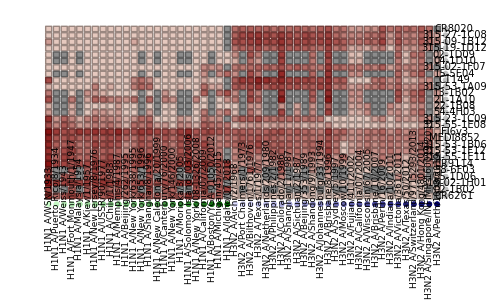

```mathematica
Block[{orderedVirus=Join[SortBy[labelVirusH1N1,virusYear],SortBy[labelVirusH3N2,virusYear]],measurement},Show[Graphics[{MapIndexed[{#,EdgeForm[{Thickness[0.002],Darker@#}],Rectangle[{1.25#2[[1]],-1.4#2[[2]]},{1.25#2[[1]]+1 0.97,-1.4#2[[2]]+1.2 0.97}]}&,Table[
measurement=data[virus,antibody];
If[MissingQ@measurement,
GrayLevel[0.55],Blend[{RGBColor[0.5, 0., 0.],RGBColor[0.9094486033287874, 0.8074808388688726, 0.7643434532363431]},Rescale[Log10@measurement/.GreaterThan[val_]:>val,{-10.4,-6.7}]]
]
,{virus,orderedVirus}
,{antibody,orderedAbStem}
],{2}],
Table[Text[font[StringReplace[orderedAbStem[[j]],"-"->"-"],10],{67,0.6-1.4j},{-1,0}],{j,27}],
Table[Text[Rotate[font[StringReplace[orderedVirus[[j]],"-"->"-"],9],π/2],{1.252j+0.97/2,-40},{0,1}],{j,51}]
},PlotRangePadding->None,ImageSize->500],
ListPlot[List/@Table[{1.25j+0.97/2,-39},{j,51}],PlotMarkers->markerVirus[0.045,"Opacity"->1,"OpacityFaceFormFactor"->1],PlotStyle->(plotStyleVirus/@orderedVirus)],
ListPlot[List/@Table[{65.6,0.6-1.4j},{j,27}],PlotMarkers->markerAb[0.045],PlotStyle->colorAbInMixture]
]
]
```

#### Accuracy of Maps as a Function of Measurements

We measured 83% of all possible antibody-virus interactions in our panel. To understand how multidimensional scaling (MDS) accuracy improves with the fraction of available measurements, we can withhold some antibody-virus interactions, remake the landscape, and then compare the withheld values against the landscape predictions.

```mathematica
(* All antibody-virus interactions *)
virusAbData=Table[data[virus,antibody],{virus,labelVirus},{antibody,labelAbStem}];
(* Positions of measured interactions *)
posMeasured=Position[virusAbData,Except[_Missing],{2},Heads->False];
```

```mathematica
(*(* Randomly withhold additional antibody-virus interactions, remake landscape, predict withheld values *)
resRandomlyWithholdData=Association@Table[
numWithhold=Length@posMeasured-Round[fracMeasured Times@@Dimensions@virusAbData];
SeedRandom[12345];
fracMeasured->Join@@Table[
posWithhold=RandomSample[posMeasured,numWithhold];
runMDS[labelAbStem,labelVirus,"VirusAbData"->ReplacePart[virusAbData,posWithhold->Missing[]]];
DeleteMissing[foldError[10^(-10+Norm[coordsVirus@labelVirus[[First@#]]-coordsAb@labelAbStem[[Last@#]]]),Extract[virusAbData,#]]&/@posWithhold]
,{iteration,5}]
,{fracMeasured,{0.4,0.5,0.6,0.7,0.8}}];
Iconize[resRandomlyWithholdData,"Randomly Withheld Data",Method->Compress]*)
resRandomlyWithholdData=;
```

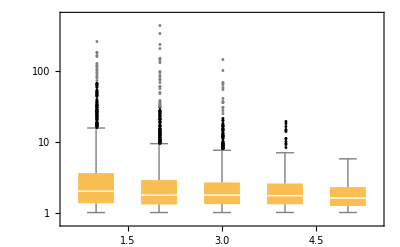

```mathematica
BoxWhiskerChart[resRandomlyWithholdData,"Outliers",PlotRange->{{0.5,5.5},{0.1,All}},ScalingFunctions->"Log",ChartLabels->Keys@resRandomlyWithholdData,FrameLabel->(font[#,14]&/@{"Fraction of Observed Values","⟨Error⟩ of Withheld Values"}),FrameTicksStyle->14]
```

### Figure S2: Patterns in Antibody and Virus Coordinates

We explore some temporal patterns in the positions of the H1N1 and H3N2 viruses on the map.

#### Uncertainty of Antibody and Virus Positions

We show the uncertainty of each antibody or virus on the Neutralization Landscape. Each entry is overlaid with an ellipse showing when the MDS stress increases by Log_10 2≈0.3, which roughly corresponds to an increase of IC_50 fold-error by 2-fold.

We find the eigen-directions where the stress increases maximally and minimally, and calculate and the value of D=(D_xx | D_xy
D_yx | D_yy) (denoted by d) along these directions. then choose the size r of the ellipse to 1/2 d_(r,r)r^2=Log_10 2.

```mathematica
mapStemUncertainty=runMDS[labelAbStem,labelVirus,"ShowMap"->"Uncertainty","ShowError"->False,"SearchPoints"->50];
Rasterize[mapStemUncertainty,ImageSize->250]
```

-Graphics-

#### Temporal Patterns of Viruses

We quantify by how much the H1N1 and H3N2 viruses move upwards along the neutralization landscape, demonstrating the rate at which viruses can shift away from an antibody response. For this analysis, we exclude H1N1 A/New Jersey/8/1976 and H3N2 A/Indiana/10/2011 that crossed over from swine.

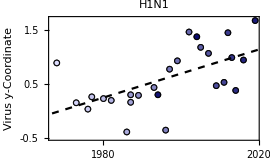
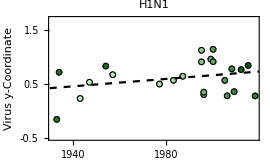

```mathematica
Block[{pnts,fit},
Table[
pnts={virusYear@#,Last@coordsVirusStem@#}&/@labelVirusType;
fit=Fit[pnts,{1,x},x];
Show[ListPlot[List/@pnts,FrameLabel->(font[#,16]&/@{"Year Virus Circulated","Virus y-Coordinate"}),],Plot[fit,{x,1930,2020},PlotStyle->{Black,Dashed}]]
(* We exclude H1N1 A/New Jersey/8/1976 and H3N2 A/Indiana/10/2011 that crossed over from swine *)
,{labelVirusType,{DeleteCases[labelVirusH3N2,"H3N2 A/Indiana/10/2011"],DeleteCases[labelVirusH1N1,"H1N1 A/New Jersey/8/1976"]}}]
]
```

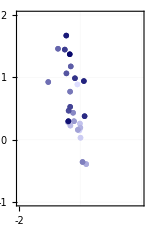
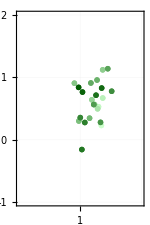
-Graphics-    H3N2 | -Graphics-    H1N1

```mathematica
{mapH3N2,mapH1N1}=Table[Show[createLandscape[{KeySelect[coordsVirusStem,MemberQ[viruses,#]&],Association[]},],],{viruses,{DeleteCases[labelVirusH3N2,"H3N2 A/Indiana/10/2011"],DeleteCases[labelVirusH1N1,"H1N1 A/New Jersey/8/1976"]}}];
Grid[{{Labeled[mapH3N2,font["    H3N2",16],Top],Labeled[mapH1N1,font["    H1N1",16],Top]}}]
```

### Figure S3: Maps in Different Dimensions

We perform metric MDS in 1D, 2D, 3D, and 4D. While 1D is extremely restrictive and more than doubles the error of both plots, 2D does a far better job of characterizing the data. Surprisingly, there seems to be minimal further gain by going to 3D or higher dimensions. We note that the time required for MDS increases substantially in higher dimensions.

#### Canned: Leave-One-Out in Different Dimensions

Removing 1 antibody in 1D and 3D - for speed, we only consider 10 antibodies and use SearchPoints=5

```mathematica
(*resLeaveOneOutAntibody1D=Association@Table[
PrintTemporary[Row[{"Removing antibody: ",leftOutAb}]];
runMDS[DeleteCases[labelAbStem,leftOutAb],labelVirus,"SearchPoints"->5,"ShowMap"->False,"Dimensions"->1];
leftOutAb->{coordsVirus,coordsAb}
,{leftOutAb,labelAbStem[[;;10]]}];
Iconize[resLeaveOneOutAntibody1D,"Leave-One-Out: Antibody MDS (1D)",Method->Compress]*)
```

```mathematica
(*resLeaveOneOutAntibody3D=Association@Table[
PrintTemporary[Row[{"Removing antibody: ",leftOutAb}]];
runMDS[DeleteCases[labelAbStem,leftOutAb],labelVirus,"SearchPoints"->5,"ShowMap"->False,"Dimensions"->3];
leftOutAb->{coordsVirus,coordsAb}
,{leftOutAb,labelAbStem[[;;10]]}];
Iconize[resLeaveOneOutAntibody3D,"Leave-One-Out: Antibody MDS (3D)",Method->Compress]*)
```

```mathematica
(*resLeaveOneOutAntibody4D=Association@Table[
PrintTemporary[Row[{"Removing antibody: ",leftOutAb}]];
runMDS[DeleteCases[labelAbStem,leftOutAb],labelVirus,"SearchPoints"->5,"ShowMap"->False,"Dimensions"->4];
leftOutAb->{coordsVirus,coordsAb}
,{leftOutAb,labelAbStem[[;;10]]}];
Iconize[resLeaveOneOutAntibody4D,"Leave-One-Out: Antibody MDS (4D)",Method->Compress]*)
```

Removing 1 virus in 1D and 3D - for speed, we only consider 10 viruses (5 H1N1 and 5 H3N2) and use SearchPoints=5

```mathematica
(*resLeaveOneOutVirus1D=Association@Table[
PrintTemporary[Row[{"Removing virus: ",leftOutVirus}]];
runMDS[labelAbStem,DeleteCases[labelVirus,leftOutVirus],"SearchPoints"->5,"ShowMap"->False,"Dimensions"->1];
leftOutVirus->{coordsVirus,coordsAb}
,{leftOutVirus,labelVirus[[;;50;;5]]}];
Iconize[resLeaveOneOutVirus1D,"Leave-One-Out: Virus MDS (1D)",Method->Compress]*)
```

```mathematica
(*resLeaveOneOutVirus3D=Association@Table[
PrintTemporary[Row[{"Removing virus: ",leftOutVirus}]];
runMDS[labelAbStem,DeleteCases[labelVirus,leftOutVirus],"SearchPoints"->5,"ShowMap"->False,"Dimensions"->3];
leftOutVirus->{coordsVirus,coordsAb}
,{leftOutVirus,labelVirus[[;;50;;5]]}];
Iconize[resLeaveOneOutVirus3D,"Leave-One-Out: Virus MDS (3D)",Method->Compress]*)
```

```mathematica
(*resLeaveOneOutVirus4D=Association@Table[
PrintTemporary[Row[{"Removing virus: ",leftOutVirus}]];
runMDS[labelAbStem,DeleteCases[labelVirus,leftOutVirus],"SearchPoints"->5,"ShowMap"->False,"Dimensions"->4];
leftOutVirus->{coordsVirus,coordsAb}
,{leftOutVirus,labelVirus[[;;50;;5]]}];
Iconize[resLeaveOneOutVirus4D,"Leave-One-Out: Virus MDS (4D)",Method->Compress]*)
```

```mathematica
resLeaveOneOutAntibody1D=;
resLeaveOneOutAntibody3D=;
resLeaveOneOutAntibody4D=;
resLeaveOneOutVirus1D=;
resLeaveOneOutVirus3D=;
resLeaveOneOutVirus4D=;
```

#### Summary of Predictions in Different Dimensions

```mathematica
(*(* Global error of Neutralization Landscapes (using all data) in 1D, 2D, 3D, or 4D *)
Do[
PrintTemporary["On dimension: "<>ToString@dim];
plotDim[dim]=runMDS[labelAbStem,labelVirus,"SearchPoints"->20,"Dimensions"->dim,"ShowError"->False];
mapErrorDim[dim]=mapError;
coordsDim[dim]={coordsVirus,coordsAb};
,{dim,1,4}];
Iconize[{coordsDim[1],coordsDim[2],coordsDim[3],coordsDim[4]},"Virus/Antibody Coordinates in Different Dimensions",Method->Compress]*)
(* === Canned Results === *)
{mapErrorDim[1],mapErrorDim[2],mapErrorDim[3],mapErrorDim[4]}={10.599,2.184,1.899,1.783};
{coordsDim[1],coordsDim[2],coordsDim[3],coordsDim[4]}=;
```

```mathematica
(* Compare leave-one-out predictions in different dimensions *)
{mapLeaveOneOutDim[1],mapLeaveOneOutDim[2],mapLeaveOneOutDim[3],mapLeaveOneOutDim[4]}=Mean/@Flatten/@Table[
resLeaveOneOut=Switch[dimension,
1,{resLeaveOneOutAntibody1D,resLeaveOneOutVirus1D},
2,{resLeaveOneOutAntibody,resLeaveOneOutVirus},
3,{resLeaveOneOutAntibody3D,resLeaveOneOutVirus3D},
4,{resLeaveOneOutAntibody4D,resLeaveOneOutVirus4D}
];
resAb=Table[
virusSubsets=selectSubset[antibodyOfInterest,First[resLeaveOneOut]@antibodyOfInterest,6,10,If[dimension===2,
2(* Choose viruses spread out by their y-coordinate in 2D *),
1(* Randomly select subsets of viruses in all other dimensions *)]];
Table[
triangulate[virusSubset,antibodyOfInterest,First[resLeaveOneOut]@antibodyOfInterest]
,{virusSubset,virusSubsets}]
,{antibodyOfInterest,labelAbStem[[;;10]]}];
resVirus=Table[
antibodySubsets=selectSubset[virusOfInterest,Last[resLeaveOneOut]@virusOfInterest,6,10,If[dimension===2,
2(* Choose viruses spread out by their y-coordinate in 2D *),
1(* Randomly select subsets of viruses in all other dimensions *)]];
Table[
triangulate[virusOfInterest,antibodySubset,Last[resLeaveOneOut]@virusOfInterest]
,{antibodySubset,antibodySubsets}]
,{virusOfInterest,labelVirus[[;;50;;5]]}];
{resAb,resVirus}
,{dimension,4}]
```

{15.1647,2.83485,3.38545,3.77664}

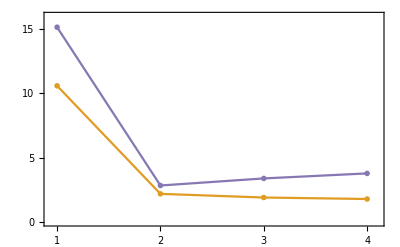

```mathematica
plotDimensions=ListPlot[Transpose[{{#,mapErrorDim[#]},{#,mapLeaveOneOutDim[#]}}&/@Range@4],]
```

#### Error of Embedding

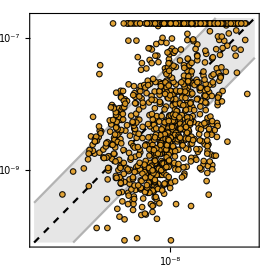
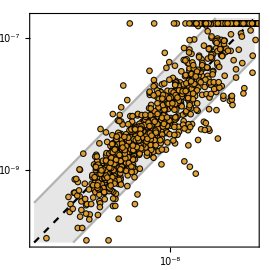
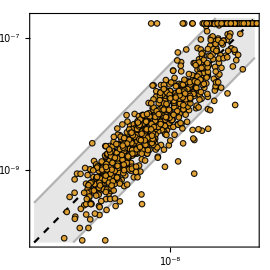
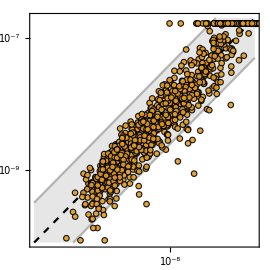

```mathematica
plots=Block[{coordsVirusStem,coordsAbStem},
Table[
{coordsVirusStem,coordsAbStem}=coordsDim[dim];
res=Join@@Table[{antibody,virus,10^(-10+Norm[coordsAbStem@antibody-coordsVirusStem@virus]),data[virus,antibody]},{antibody,labelAbStem},{virus,labelVirus}];
Show[Plot[{x,4x,x/4},{x,10^-10.1,10^-6.7},],
ListPlot[DeleteMissing[res[[All,{3,4}]],1,All]/.GreaterThan[val_]:>val,PlotMarkers->(plotMarker[0.03,0.9]/.Thickness[Tiny]->Thickness[Small]),PlotStyle->ColorData[97][2],ScalingFunctions->{"Log","Log"}]]
,{dim,4}]
]
```

#### Error of Predictions

```mathematica
plotData=Table[
resLeaveOneOut=Switch[dimension,
1,{resLeaveOneOutAntibody1D,resLeaveOneOutVirus1D},
2,{resLeaveOneOutAntibody,resLeaveOneOutVirus},
3,{resLeaveOneOutAntibody3D,resLeaveOneOutVirus3D},
4,{resLeaveOneOutAntibody4D,resLeaveOneOutVirus4D}
];
resAb=Table[
virusSubsets=selectSubset[antibodyOfInterest,First[resLeaveOneOut]@antibodyOfInterest,6,10,If[dimension===2,
2(* Choose viruses spread out by their y-coordinate in 2D *),
1(* Randomly select subsets of viruses in all other dimensions *)]];
Table[
triangulate[virusSubset,antibodyOfInterest,First[resLeaveOneOut]@antibodyOfInterest,"ReturnFoldError"->False]
,{virusSubset,virusSubsets}]
,{antibodyOfInterest,labelAbStem[[;;10]]}];
resVirus=Table[
antibodySubsets=selectSubset[virusOfInterest,Last[resLeaveOneOut]@virusOfInterest,6,10,If[dimension===2,
2(* Choose viruses spread out by their y-coordinate in 2D *),
1(* Randomly select subsets of viruses in all other dimensions *)]];
Table[
triangulate[virusOfInterest,antibodySubset,Last[resLeaveOneOut]@virusOfInterest,"ReturnFoldError"->False]
,{antibodySubset,antibodySubsets}]
,{virusOfInterest,labelVirus[[;;50;;5]]}];
{resAb,resVirus}
,{dimension,4}];
```

```mathematica
plotsPredictions=Table[
Show[Plot[{x,4x,x/4},{x,10^-10.1,10^-6.7},],
ListPlot[Flatten[plotData[[dim]],3],PlotMarkers->(plotMarker[0.03,0.9]/.Thickness[Tiny]->Thickness[Small]),PlotStyle->ColorData[97][5],ScalingFunctions->{"Log","Log"}]]
,{dim,4}]
```

### Figure S4: Outlier Detection

We remeasured some of the antibody-virus interactions that were predicted to be the largest outliers based on the Neutralization Landscape. The results were quite impressive, with 13/16 of the large outliers (whose measurements were more than 10x off from the predictions) now remeasured within 10x  from  spectacular, with nearly all of the big outliers shifting drastically towards the predictions. The result is a much more robust antibody-virus map, and it seems that there are relatively few cases of huge outliers that the map cannot capture!

```mathematica
resBigOutliers=;
resSmallOutliers=;
(* Statistics *)
Echo[Round[Mean[foldError/@resBigOutliers[[All,-2]]],0.1]->Round[Mean[foldError/@resBigOutliers[[All,-1]]],0.1],"fold-error for large outliers:"];
Echo[Round[Mean[foldError/@resSmallOutliers[[All,-2]]],0.1]->Round[Mean[foldError/@resSmallOutliers[[All,-1]]],0.1],"fold-error for small outliers:"];
```

fold-error for large outliers:  21.7→5.9

fold-error for small outliers:  2.2→3.1

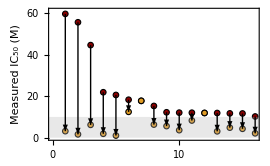
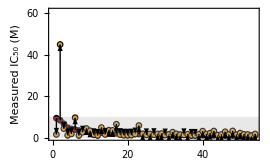

```mathematica
Table[
plotData=Transpose@ReverseSortBy[Transpose@{foldError/@res[[All,-2]],foldError/@res[[All,-1]]},First];
ListPlot[plotData,PlotRange->{0,61},PlotMarkers->{plotMarker[0.05],plotMarker[0.03]},Epilog->{{Directive[Opacity[0.3],GrayLevel[0.7]],Rectangle[{-1,0},{100,10}]},Arrowheads[Medium],MapIndexed[Arrow@{{First@#2,#[[1]]},{First@#2,#[[2]]}}&,Transpose@plotData]},ImageSize->270,Frame->{True,True,False,False},FrameLabel->(font[#,14]&/@{"Indexed Antibody-Virus Measurements","Measured IC_50 (M)"}),FrameTicks->{LinTicks[0,Length@res,TickLengthScale->2],LinTicks[0,60,TickLengthScale->2]},FrameTicksStyle->12,PlotStyle->{RGBColor[0.5411765712177555, 0., 2.7592375640810018*^-8],ColorData[97][2]}]
,{res,{resBigOutliers,resSmallOutliers}}]
```

### Figure S5: Predicting Antibody Behavior in External Dataset

Validating the maps and the ability to position and predict new mAb behavior using an external source of data [Nakamura 2013, Table 1]. We make the following substitutions to have a few extra predictions:

ΔAA=2: H1N1 A/Brisbane/59/2007 → H1N1 A/New York/08-1326/2008

ΔAA=5: H3N2 A/Victoria/3/1975 → H3N2 A/Bilthoven/1761/1976

In addition to triangulating the viruses using all data, we choose 3 H1N1 and 3 H3N2 viruses (spaced widely apart) and predict the remaining measurements. Although the measurements are pretty bimodal, the predictions are 2.6-fold off on average. Moreover, we see that no antibody has an IC_50<=10^-10 Molar against both H1N1 and H3N2 viruses, which our map says should be impossible.

```mathematica
substitute=True;
(* Viruses not in panel: "H1N1 A/Brisbane/59/2007", "H3N2 A/Victoria/3/1975", "H3N2 A/Hong Kong/8/1968" *)
(data[#[[1]],"Nakamura2013_39.18"]=#[[2]])&/@{
{"H1N1 A/California/07/2009",1.1 10^-9.},
{If[substitute,"H1N1 A/New York/08-1326/2008","H1N1 A/Brisbane/59/2007"],2.3 10^-9.},
{"H1N1 A/Solomon Islands/03/2006",8.0 10^-9.},
{"H1N1 A/New Caledonia/20/1999",3.1 10^-9.},
{"H1N1 A/Puerto Rico/8/1934",1.2 10^-9.},
{"H3N2 A/Victoria/361/2011",GreaterThan[1.6 10^-6.]},
{"H3N2 A/Perth/16/2009",GreaterThan[1.6 10^-6.]},
{"H3N2 A/Brisbane/10/2007",GreaterThan[1.6 10^-6.]},
{"H3N2 A/Wisconsin/67/2005",GreaterThan[1.6 10^-6.]},
{If[substitute,"H3N2 A/Bilthoven/1761/1976","H3N2 A/Victoria/3/1975"],GreaterThan[1.6 10^-6.]},
{"H3N2 A/Port Chalmers/1/1973",GreaterThan[1.6 10^-6.]},
{"H3N2 A/Hong Kong/8/1968",GreaterThan[1.6 10^-6.]},
{"H3N2 A/Aichi/2/1968",GreaterThan[1.6 10^-6.]}};
(data[#[[1]],"Nakamura2013_39.29"]=#[[2]])&/@{
{"H1N1 A/California/07/2009",2.5 10^-9.},
{If[substitute,"H1N1 A/New York/08-1326/2008","H1N1 A/Brisbane/59/2007"],1.9 10^-9.},
{"H1N1 A/Solomon Islands/03/2006",25.1 10^-9.},
{"H1N1 A/New Caledonia/20/1999",9.2 10^-9.},
{"H1N1 A/Puerto Rico/8/1934",2.0 10^-9.},
{"H3N2 A/Victoria/361/2011",3.4 10^-9.},
{"H3N2 A/Perth/16/2009",3.0 10^-9.},
{"H3N2 A/Brisbane/10/2007",2.3 10^-9.},
{"H3N2 A/Wisconsin/67/2005",1.3 10^-9.},
{If[substitute,"H3N2 A/Bilthoven/1761/1976","H3N2 A/Victoria/3/1975"],2.5 10^-9.},
{"H3N2 A/Port Chalmers/1/1973",2.2 10^-9.},
{"H3N2 A/Hong Kong/8/1968",45.1 10^-9.},
{"H3N2 A/Aichi/2/1968",35.0 10^-9.}};
(data[#[[1]],"Nakamura2013_81.39"]=#[[2]])&/@{
{"H1N1 A/California/07/2009",2.1 10^-9.},
{If[substitute,"H1N1 A/New York/08-1326/2008","H1N1 A/Brisbane/59/2007"],0.65 10^-9.},
{"H1N1 A/Solomon Islands/03/2006",14.6 10^-9.},
{"H1N1 A/New Caledonia/20/1999",6.1 10^-9.},
{"H1N1 A/Puerto Rico/8/1934",1.9 10^-9.},
{"H3N2 A/Victoria/361/2011",3.6 10^-9.},
{"H3N2 A/Perth/16/2009",1.6 10^-9.},
{"H3N2 A/Brisbane/10/2007",1.9 10^-9.},
{"H3N2 A/Wisconsin/67/2005",0.81 10^-9.},
{If[substitute,"H3N2 A/Bilthoven/1761/1976","H3N2 A/Victoria/3/1975"],2.8 10^-9.},
{"H3N2 A/Port Chalmers/1/1973",1.5 10^-9.},
{"H3N2 A/Hong Kong/8/1968",26.3 10^-9.},
{"H3N2 A/Aichi/2/1968",7.3 10^-9.}};
(data[#[[1]],"Nakamura2013_36.89"]=#[[2]])&/@{
{"H1N1 A/California/07/2009",GreaterThan[1.6 10^-6.]},
{If[substitute,"H1N1 A/New York/08-1326/2008","H1N1 A/Brisbane/59/2007"],GreaterThan[1.6 10^-6.]},
{"H1N1 A/Solomon Islands/03/2006",GreaterThan[1.6 10^-6.]},
{"H1N1 A/New Caledonia/20/1999",GreaterThan[1.6 10^-6.]},
{"H1N1 A/Puerto Rico/8/1934",GreaterThan[1.6 10^-6.]},
{"H3N2 A/Victoria/361/2011",9.7 10^-9.},
{"H3N2 A/Perth/16/2009",1.1 10^-9.},
{"H3N2 A/Brisbane/10/2007",1.9 10^-9.},
{"H3N2 A/Wisconsin/67/2005",1.6 10^-9.},
{If[substitute,"H3N2 A/Bilthoven/1761/1976","H3N2 A/Victoria/3/1975"],2.2 10^-9.},
{"H3N2 A/Port Chalmers/1/1973",1.9 10^-9.},
{"H3N2 A/Hong Kong/8/1968",34.7 10^-9.},
{"H3N2 A/Aichi/2/1968",13.9 10^-9.}};
(* Display data *)
listAbNakamura={"Nakamura2013_39.18","Nakamura2013_39.29","Nakamura2013_81.39","Nakamura2013_36.89"};
listVirusNakamura={"H1N1 A/California/07/2009",If[substitute,"H1N1 A/New York/08-1326/2008","H1N1 A/Brisbane/59/2007"],"H1N1 A/Solomon Islands/03/2006","H1N1 A/New Caledonia/20/1999","H1N1 A/Puerto Rico/8/1934","H3N2 A/Victoria/361/2011","H3N2 A/Perth/16/2009","H3N2 A/Brisbane/10/2007","H3N2 A/Wisconsin/67/2005",If[substitute,"H3N2 A/Bilthoven/1761/1976","H3N2 A/Victoria/3/1975"],"H3N2 A/Port Chalmers/1/1973","H3N2 A/Aichi/2/1968"};
Block[{listAb=listAbNakamura,listVirus=Insert[listVirusNakamura,"H3N2 A/Hong Kong/8/1968",-2]},
showGrid[Transpose@Prepend[Transpose@Prepend[Table[data[virus,antibody],{virus,listVirus},{antibody,listAb}],listAb],Prepend[listVirus,""]]/.GreaterThan[val_]:>font@Row[{">",val}],"Header"->"TopLeft"]
]
```

| Nakamura2013_39.18 | Nakamura2013_39.29 | Nakamura2013_81.39 | Nakamura2013_36.89
H1N1 A/California/07/2009 | 1.1×10^-9 | 2.5×10^-9 | 2.1×10^-9 | >1.6×10^-6
H1N1 A/New York/08-1326/2008 | 2.3×10^-9 | 1.9×10^-9 | 6.5×10^-10 | >1.6×10^-6
H1N1 A/Solomon Islands/03/2006 | 8.×10^-9 | 2.51×10^-8 | 1.46×10^-8 | >1.6×10^-6
H1N1 A/New Caledonia/20/1999 | 3.1×10^-9 | 9.2×10^-9 | 6.1×10^-9 | >1.6×10^-6
H1N1 A/Puerto Rico/8/1934 | 1.2×10^-9 | 2.×10^-9 | 1.9×10^-9 | >1.6×10^-6
H3N2 A/Victoria/361/2011 | >1.6×10^-6 | 3.4×10^-9 | 3.6×10^-9 | 9.7×10^-9
H3N2 A/Perth/16/2009 | >1.6×10^-6 | 3.×10^-9 | 1.6×10^-9 | 1.1×10^-9
H3N2 A/Brisbane/10/2007 | >1.6×10^-6 | 2.3×10^-9 | 1.9×10^-9 | 1.9×10^-9
H3N2 A/Wisconsin/67/2005 | >1.6×10^-6 | 1.3×10^-9 | 8.1×10^-10 | 1.6×10^-9
H3N2 A/Bilthoven/1761/1976 | >1.6×10^-6 | 2.5×10^-9 | 2.8×10^-9 | 2.2×10^-9
H3N2 A/Port Chalmers/1/1973 | >1.6×10^-6 | 2.2×10^-9 | 1.5×10^-9 | 1.9×10^-9
H3N2 A/Hong Kong/8/1968 | >1.6×10^-6 | 4.51×10^-8 | 2.63×10^-8 | 3.47×10^-8
H3N2 A/Aichi/2/1968 | >1.6×10^-6 | 3.5×10^-8 | 7.3×10^-9 | 1.39×10^-8

```mathematica
(* Positioning the antibodies using all meaurements *)
plots=Show[triangulate[listVirusNakamura,#,{coordsVirusStem,coordsAbStem},"ShowMap"->True],PlotRange->3.5{{-1,1},{-1,1}},FrameTicksStyle->20,FrameStyle->Thickness[Medium]]&/@listAbNakamura;
Rasterize[Grid[Partition[plots,2]],ImageSize->300]
```

-Graphics-

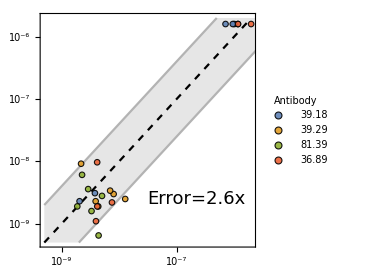

```mathematica
(* 6 Viruses used to predict Only use data from 3 H1N1 and 3 H3N2 viruses - predict the remaining data *)
virusForTriangulation={"H1N1 A/California/07/2009","H1N1 A/Solomon Islands/03/2006","H1N1 A/Puerto Rico/8/1934","H3N2 A/Wisconsin/67/2005","H3N2 A/Port Chalmers/1/1973","H3N2 A/Aichi/2/1968"};
virusForPrediction={"H1N1 A/New Caledonia/20/1999","H1N1 A/New York/08-1326/2008","H3N2 A/Bilthoven/1761/1976","H3N2 A/Brisbane/10/2007","H3N2 A/Perth/16/2009","H3N2 A/Victoria/361/2011"};
predictionNakamuraSubset=triangulate[virusForTriangulation,#,{coordsVirusStem,coordsAbStem},"ReturnFoldError"->False,"KeepBoundedValues"->True]&/@listAbNakamura;
Show[Plot[{x,x/4,4x},{x,0.5 10^-9,10^-5},],ListPlot[DeleteCases[predictionNakamuraSubset,{_,_data},{2}]/.GreaterThan[val_]:>val,]]
```

```mathematica
(* Comparing neutralization against the viruses used for triangulation *)
{color1,color2}={Darker[RGBColor[0.40098143426537214, 0.5419411121910688, 0.7689393936518475],0.2],Darker[RGBColor[0.7885607706078754, 0.5223279640624574, 0.451841954063326],0.2]};
showGrid[Transpose@Prepend[Transpose@Prepend[Join[
Table[font[data[virus,antibody]/.val_Real:>(Round[#,If[#==Round[#],1,0.1]]&[val/10^-10.]),color1],{virus,virusForTriangulation},{antibody,listAbNakamura}]/.GreaterThan[val_]:>Row[{">",val}],
Map[Column[{font[#[[2]]/.val_Real:>(Round[#,If[#==Round[#],1,0.1]]&[val/10^-10.]),color1],font[#[[1]]/.val_Real:>(Which[0<#<100,Round[#,1],100<#<1000,Round[#,10],1000<#,Round[#,100]]&[val/10^-10.]),color2]},Alignment->Center]&,Transpose@DeleteCases[predictionNakamuraSubset,{_,_data},{2}]/.GreaterThan[val_]:>Row[{">",val}],{2}]
],font["Ab "<>StringTake[#,-5]]&/@listAbNakamura],Prepend[Join[virusForTriangulation,virusForPrediction],font["IC_50 (× 10^-10 Molar)",Bold]]]]
```

IC_50 (× 10^-10 Molar) | Ab 39.18 | Ab 39.29 | Ab 81.39 | Ab 36.89
H1N1 A/California/07/2009 | 11 | 25 | 21 | >16000
H1N1 A/Solomon Islands/03/2006 | 80 | 251 | 146 | >16000
H1N1 A/Puerto Rico/8/1934 | 12 | 20 | 19 | >16000
H3N2 A/Wisconsin/67/2005 | >16000 | 13 | 8.1 | 16
H3N2 A/Port Chalmers/1/1973 | >16000 | 22 | 15 | 19
H3N2 A/Aichi/2/1968 | >16000 | 350 | 73 | 139
H1N1 A/New Caledonia/20/1999 | 31
38 | 92
22 | 61
23 | >16000
11700
H1N1 A/New York/08-1326/2008 | 23
21 | 19
43 | 6.5
44 | >16000
19800
H3N2 A/Bilthoven/1761/1976 | >16000
7100 | 25
130 | 28
50 | 22
75
H3N2 A/Brisbane/10/2007 | >16000
11600 | 23
39 | 19
19 | 19
42
H3N2 A/Perth/16/2009 | >16000
10100 | 30
80 | 16
33 | 11
40
H3N2 A/Victoria/361/2011 | >16000
9500 | 34
70 | 36
29 | 97
42

```mathematica
(* Predicting neutralization against the rest of our virus panel *)
predictionNakamuraFull=triangulate[listVirusNakamura,#,{coordsVirusStem,coordsAbStem},"ReturnFoldError"->False,"KeepBoundedValues"->True,"ReturnPurePredictions"->True]&/@listAbNakamura;
gridData=Prepend[#[[All,1]]/.val_Real:>(font[Which[0<#<100,Round[#,1],100<#<1000,Round[#,10],1000<#,Round[#,100]],color2]&[val/10^-10.]),#[[1,-1,1]]/.{"H3N2 A/Switzerland/9715293/2013"->"H3N2 A/Switzerland/.../2013","H1N1 A/Boston/YGA-01050/2012"->"H1N1 A/Boston/.../2012","H3N2 A/Singapore/INFIMH-160019/2016"->"H3N2 A/Singapore/.../2016"}]&/@Transpose@predictionNakamuraFull;
(* Sort viruses by year *)
gridData=gridData[[InversePermutation@Ordering@Cases[labelVirus,virus_/;MemberQ[First/@gridData,virus]]]];
(* Grid *)
gridPanelPredictions=showGrid@Prepend[SortBy[gridData,{StringTake[#[[1]],4],virusYear@#[[1]]}&],Prepend[font["Ab "<>StringTake[#,-5]]&/@listAbNakamura,font["IC_50 (× 10^-10 Molar)",Bold]]]
```

IC_50 (× 10^-10 Molar) | Ab 39.18 | Ab 39.29 | Ab 81.39 | Ab 36.89
H1N1 A/WSN/1933 | 110 | 100 | 54 | 5900
H1N1 A/Weiss/1943 | 41 | 76 | 48 | 11100
H1N1 A/Fort Monmouth/1/1947 | 39 | 44 | 30 | 9800
H1N1 A/Malaysia/1954 | 34 | 33 | 25 | 11500
H1N1 A/Kiev/1/1957 | 33 | 41 | 30 | 11600
H1N1 A/New Jersey/8/1976 | 56 | 60 | 37 | 7900
H1N1 A/USSR/90/1977 | 41 | 45 | 30 | 9500
H1N1 A/Chile/1/1983 | 45 | 37 | 25 | 8500
H1N1 A/Memphis/4/1987 | 49 | 31 | 21 | 7700
H1N1 A/Beijing/262/1995 | 37 | 26 | 23 | 13000
H1N1 A/New York/638/1995 | 97 | 13 | 9 | 4200
H1N1 A/New York/653/1996 | 89 | 39 | 23 | 4700
H1N1 A/Shanghai/8/1996 | 59 | 46 | 29 | 7000
H1N1 A/Canterbury/76/2000 | 52 | 21 | 16 | 7800
H1N1 A/New York/146/2000 | 31 | 31 | 28 | 15800
H1N1 A/Morioka/3/2005 | 47 | 37 | 24 | 8200
H1N1 A/Boston/.../2012 | 70 | 20 | 14 | 5500
H1N1 A/Michigan/45/2015 | 82 | 16 | 11 | 4900
H1N1 A/Idaho/07/2018 | 73 | 46 | 28 | 5900
H3N2 A/Netherlands/209/1980 | 11800 | 62 | 36 | 35
H3N2 A/Philippines/2/1982 | 8200 | 52 | 29 | 52
H3N2 A/Colorado/2/1986 | 8800 | 150 | 76 | 96
H3N2 A/Shanghai/11/1987 | 9100 | 59 | 33 | 48
H3N2 A/Sichuan/2/1987 | 10100 | 51 | 29 | 40
H3N2 A/Beijing/353/1989 | 12700 | 60 | 36 | 32
H3N2 A/Shandong/9/1993 | 10200 | 41 | 25 | 38
H3N2 A/Johannesburg/33/1994 | 12500 | 58 | 35 | 32
H3N2 A/Brisbane/8/1996 | 9800 | 150 | 76 | 82
H3N2 A/Moscow/10/1999 | 25600 | 48 | 37 | 18
H3N2 A/Fujian/411/2002 | 20300 | 25 | 25 | 46
H3N2 A/California/07/2004 | 12700 | 16 | 16 | 59
H3N2 A/Indiana/10/2011 | 6100 | 8 | 7 | 100
H3N2 A/Switzerland/.../2013 | 9500 | 18 | 14 | 49
H3N2 A/Hong Kong/4801/2014 | 6700 | 34 | 19 | 58
H3N2 A/Singapore/.../2016 | 6700 | 14 | 10 | 66
H3N2 A/Perth/1008/2019 | 16500 | 18 | 20 | 80

### Figure S6: Triangle Inequality

For our bipartite data (where antibody-virus distance can be directly measured but not virus-virus or antibody-antibody distance), the typical triangle inequality is modified to the following form:

d_(Ab-V)≤d_(Ab-Ṽ)+d_(OverTilde[Ab]-Ṽ)+d_(OverTilde[Ab]-V)

#### Interpretation of Virus-Virus Distance

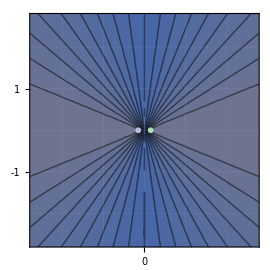
-Graphics- |

```mathematica
Block[{pnt1={-0.15,0},pnt2={0.15,0},colorsAb={RGBColor[0.63, 0.33, 0.],RGBColor[0.91, 0.41000000000000003, 0.],RGBColor[0.868760923512047, 0.5649748779513059, 0.6961601912198824]},blankMap=createLandscape[{<|x->y|>,Association[]}]},
Grid[{{Show[blankMap,ContourPlot[foldError[{10^(-10+Norm[{x,y}-pnt1]),10^(-10+Norm[{x,y}-pnt2])}]/10,{x,-3,3},{y,-3,3},ColorFunctionScaling->False],ListPlot[{{pnt1},{pnt2}},],],BarLegend[{Table[ColorData["M10DefaultDensityGradient"][x],{x,Subdivide[0,0.25,5]}],{1,2}},Subdivide[1,2,5]]}}]
]
```

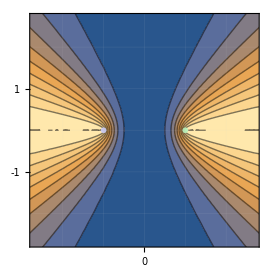
-Graphics- |

```mathematica
Block[{pnt1={-1,0},pnt2={1,0},colorsAb={RGBColor[0.63, 0.33, 0.],RGBColor[0.868760923512047, 0.5649748779513059, 0.6961601912198824]},blankMap=createLandscape[{<|x->y|>,Association[]}]},
Grid[{{Show[blankMap,ContourPlot[foldError[{10^(-10+Norm[{x,y}-pnt1]),10^(-10+Norm[{x,y}-pnt2])}]/100,{x,-3,3},{y,-3,3},ColorFunctionScaling->False],ListPlot[{{pnt1},{pnt2}},],],BarLegend[{"M10DefaultDensityGradient",{0,100}},9,LegendLayout->"Column",LabelStyle->{FontSize->14,FontFamily->"Times"}]}}]
]
```

#### How Often is the Triangle Inequality is Satisfied

Stem map (properly accounting for error): If we think about the inequality in Equation 1 relative to zero (d_(Ab-V)-d_(Ab-Ṽ)-d_(OverTilde[Ab]-Ṽ)-d_(OverTilde[Ab]-V)≤0), the error of the left-hand side will be √4 σ=2σ

```mathematica
{resCorrectStemFac2,resIncorrectStemFac2}=analyzeTriangleInequality[labelVirus,labelAbStem,2];
Echo[Row[{Round[100N@((Length@resCorrectStemFac2)/(Length@resCorrectStemFac2+Length@resIncorrectStemFac2)),0.001],"%"}],"Stem Correct cases:"];
```

Stem Correct cases:  99.797%

### Figure S7: Visualizing the Antibody Mixtures

14 antibody mixtures containing two or three antibodies are shown below, with each antibody labeled with the mixtures that contain it.

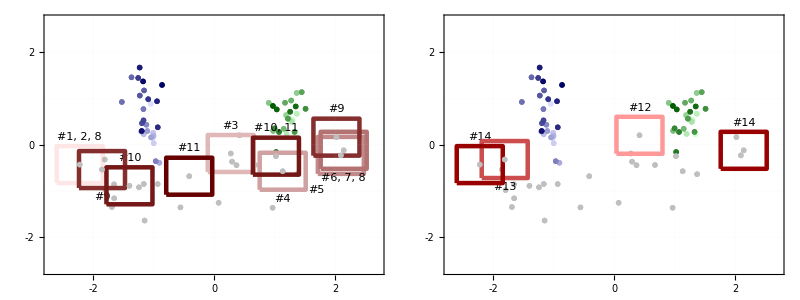

```mathematica
(* Find which mixtures use 'antibody' *)
Clear[writeMixtureLabels]
writeMixtureLabels[antibody_,mixtureSize:(2|3)]:=Block[{mixturesUsingAb,text},
mixturesUsingAb=Join@@Position[orderedMixtures,mix_/;Length@Flatten@mix==mixtureSize&&MemberQ[Last@mix,antibody],{1},Heads->False];
text=If[Length@mixturesUsingAb==0,"",Row@Prepend[Riffle[font[#,14,Bold,Darker[Join[boxColors[2,11],boxColors[3,3]][[#]],0.15]]&/@mixturesUsingAb,font[", ",14,GrayLevel[0.59]]],font["#",14,GrayLevel[0.59]]]];
Text[text,coordsAbStem@antibody+If[mixturesUsingAb=={5},{-0.4,-0.75},{0,If[(mixtureSize==2&&antibody=="315-27-1C08"||MemberQ[{{4},{6,7,8}},mixturesUsingAb])||(mixtureSize==3&&MemberQ[{{13}},mixturesUsingAb]),-1,1]0.6}],Background->Directive[White,Opacity[0.8]]]
]
(* Draw all of the mixtures with either 2 or 3 antibodies *)
showMixtures[mixtureSize:(2|3)]:=Block[{mixturesOfInterest,labelAbStemMixtures,size={0.38,0.4}},
mixturesOfInterest=Cases[orderedMixtures,mixture_/;Length@Flatten[mixture]==mixtureSize];
labelAbStemMixtures=DeleteDuplicates[Join@@Last/@mixturesOfInterest];
Show[createLandscape[{coordsVirusStem,KeyTake[coordsAbStem,Complement[labelAbStem,labelAbStemMixtures]]},"MarkerAbOpacity"->0.1],Graphics[{FaceForm[],{EdgeForm[Directive[Thickness[0.012],boxColors[mixtureSize][[Min[First/@Position[mixturesOfInterest,#]]]]]],Rectangle[coordsAbStem@#-size,coordsAbStem@#+size]}&/@labelAbStemMixtures,writeMixtureLabels[#,mixtureSize]&/@labelAbStemMixtures}],ListPlot[List/@coordsAbStem/@labelAbStemMixtures,PlotMarkers->markerAb[],PlotStyle->colorAbInMixture]]
]
Grid[{{showMixtures[2],showMixtures[3]}},Spacings->3]
```

```mathematica
colors=Join[boxColors[2],boxColors[3]];
Block[{labelAbStem=orderedAbStem},
MapIndexed[(
mixture=#;
color=colors[[First@#2]];
Row@Join[font[#,color]&/@{"Mixture #",ToString@First@#2,": "},Riffle[Join[font@Subscript["Stem Ab",#]&/@Flatten[Position[labelAbStem,#]&/@Last@mixture],font[Subscript["Head Ab",#],Gray]&/@Flatten[Position[labelAbHead,#]&/@First@mixture]]," + "]]
)&,orderedMixtures]//Column
]
```

Mixture #1: (Stem Ab)_1 + (Head Ab)_3
Mixture #2: (Stem Ab)_1 + (Head Ab)_4
Mixture #3: (Stem Ab)_18 + (Head Ab)_1
Mixture #4: (Stem Ab)_23 + (Head Ab)_5
Mixture #5: (Stem Ab)_26 + (Head Ab)_2
Mixture #6: (Stem Ab)_27 + (Head Ab)_2
Mixture #7: (Stem Ab)_27 + (Head Ab)_1
Mixture #8: (Stem Ab)_27 + (Stem Ab)_1
Mixture #9: (Stem Ab)_25 + (Stem Ab)_2
Mixture #10: (Stem Ab)_8 + (Stem Ab)_22
Mixture #11: (Stem Ab)_12 + (Stem Ab)_22
Mixture #12: (Stem Ab)_17 + (Head Ab)_6 + (Head Ab)_1
Mixture #13: (Stem Ab)_3 + (Head Ab)_1 + (Head Ab)_4
Mixture #14: (Stem Ab)_27 + (Stem Ab)_1 + (Head Ab)_1

### Figure S9: Decomposition Pathway

Here, we follow the decomposition algorithm for two mixtures:

Mixture #1 [top row]: Decomposition starts with n=1 antibody, tries n=2 antibodies, but does not find the necessary ≥20% decrease in decomposition error. The optimal decomposition with n=1 antibody is returned.

Mixture #14 [bottom row]: Decomposition starts with n=1 antibody, tries and accepts n=2 antibodies, tries and declines n=3 antibodies. The optimal decomposition with n=2 antibodies is returned.

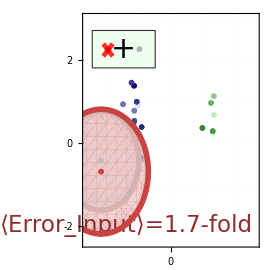
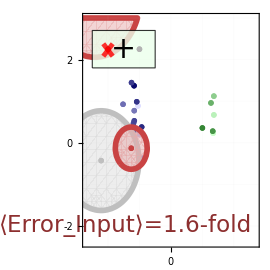

```mathematica
Block[{pnt1={-2.5,1.8},pnt2={-0.5,2.7},mean,offset1={-0.15,-0.15},offset2={0,-0.02},posAbs},
mean=Mean[{pnt1,pnt2}];
(
mixture=orderedMixtures[[1]];
posAbs={{-2,Last@mean},{-1,Last@mean}};
Show[decomposeSerum[mixture,#,virusesForDecomp,"RemoveHeadAbSignal"->True,"ErrorFontSize"->23,"EpilogLabelPosition"->{2.6,-2.},"PlotMarkerAntibody"->markerAb[0.15],"PlotMarkerVirus"->markerVirus[0.13],PlotRange->{2.7{-1,1},2.7{-1,1}+0.3},"ErrorComputedAgainst"->"Input"],Graphics[{{EdgeForm[Black],Lighter@LightGreen,Opacity[0.8],Rectangle[pnt1,pnt2,RoundingRadius->0.1]},Text[font["+",30],mean]}],ListPlot[List/@posAbs,PlotMarkers->markerAb[],PlotStyle->{RGBColor[0.4549020823970525, 0.3058815906405108, 0.19999958424451392],RGBColor[0.6980392002989493, 0.698038666521795, 0.6980383860654681]}],Graphics[{Red,Opacity[0.8],Thickness[0.013],Line[{{#+offset2-offset1,#+offset2+offset1},{#+offset2-{1,-1}offset1,#+offset2+{1,-1}offset1}}]&/@posAbs[[;;Length@First@mixture]]}](*font[Row@Riffle[Join[Style[Subsuperscript["Ab",#,"Head"],Darker[Brown,0.1]]&/@Flatten[Position[labelAbHead,#]&/@First@mixture],Style[Subsuperscript["Ab",#,"Stem"],Gray]&/@Flatten[Position[labelAbStem,#]&/@Last@mixture]]," + "],24]*)]/."⟨Error⟩="->"⟨Error_Input⟩="
)&/@Range@2
]
```

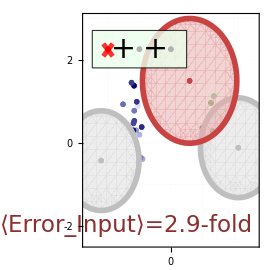
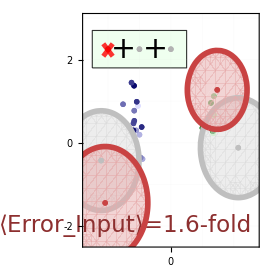
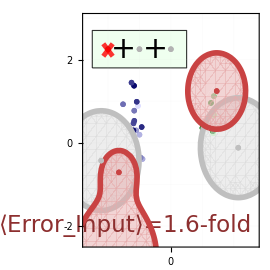

```mathematica
Block[{pnt1={-2.5,1.8},pnt2={0.5,2.7},mean,offset1={-0.15,-0.15},offset2={0,-0.02},posAbs},
mean=Mean[{pnt1,pnt2}];
(
posAbs={{-2,Last@mean},{-1,Last@mean},{0,Last@mean}};
mixture=orderedMixtures[[14]];
Show[decomposeSerum[mixture,#,virusesForDecomp,"RemoveHeadAbSignal"->True,"ErrorFontSize"->23,"EpilogLabelPosition"->{2.6,-2.},"PlotMarkerAntibody"->markerAb[0.15],"PlotMarkerVirus"->markerVirus[0.13],PlotRange->{2.7{-1,1},2.7{-1,1}+0.3},"ErrorComputedAgainst"->"Input"],Graphics[{{EdgeForm[Black],Lighter@LightGreen,Opacity[0.8],Rectangle[pnt1,pnt2,RoundingRadius->0.1]},Text[font["+",30],Mean@posAbs[[1;;2]]],Text[font["+",30],Mean@posAbs[[2;;3]]]}],ListPlot[{{{-2,Last@mean}},{{-1,Last@mean}},{{0,Last@mean}}},PlotMarkers->markerAb[],PlotStyle->{RGBColor[0.4549020823970525, 0.3058815906405108, 0.19999958424451392],RGBColor[0.6980392002989493, 0.698038666521795, 0.6980383860654681],RGBColor[0.6980392002989493, 0.698038666521795, 0.6980383860654681]}],Graphics[{Red,Opacity[0.8],Thickness[0.013],Line[{{#+offset2-offset1,#+offset2+offset1},{#+offset2-{1,-1}offset1,#+offset2+{1,-1}offset1}}]&/@posAbs[[;;Length@First@mixture]]}]]/."⟨Error⟩="->"⟨Error_Input⟩="
)&/@Range@3
]
```

### Figure S10: Decomposing All Antibody Mixtures

We decompose our 14 antibody mixtures, letting the algorithm determine the number of antibodies, their stoichiometry, and their location on the map. The resulting predicted antibodies are shown in red while the actual antibodies in the mixture are shown in gray. The radius of the circles around each antibody correspond to their stoichiometry, with a larger radius indicating that the antibody makes up a larger fraction of the mixture.

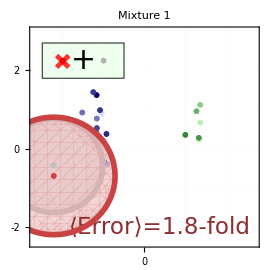
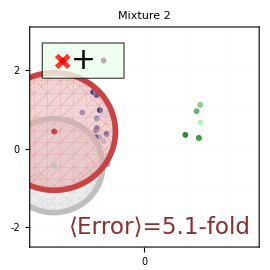
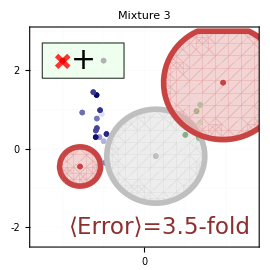
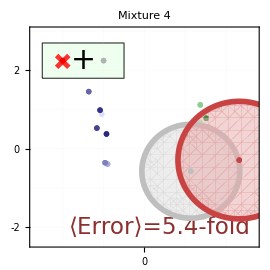
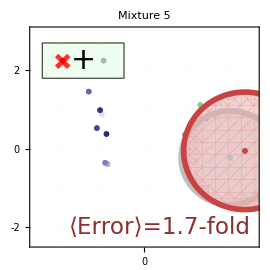
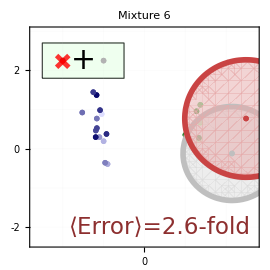
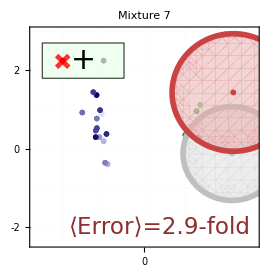
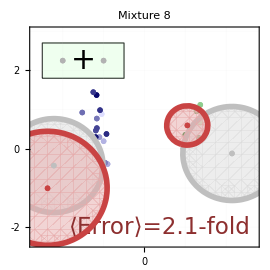

```mathematica
Block[{xMin=-2.5,xMax,yMin=1.8,yMax=2.7,coordX,coordY,posAbs,offset={-0.15,-0.15}},
Table[
xMax=xMin+Length@Flatten@mixture;
coordX=Subdivide[xMin,xMax,2Length@Flatten@mixture];
coordY=Mean[{yMin,yMax}];
posAbs=Thread[{coordX[[2;;-2;;2]],coordY}];
Show[decomposeSerum[mixture,Automatic,virusesForDecomp,"RemoveHeadAbSignal"->True,"ErrorFontSize"->23,"EpilogLabelPosition"->{2.6,-2.},"PlotMarkerAntibody"->markerAb[0.15],"PlotMarkerVirus"->markerVirus[0.13],PlotRange->{2.7{-1,1},2.7{-1,1}+0.3}],Graphics[{{EdgeForm[Black],Lighter@LightGreen,Opacity[0.8],Rectangle[{xMin,yMin},{xMax,yMax},RoundingRadius->0.1]},Text[font["+",30],#]&/@Thread[{coordX[[3;;-3;;2]],coordY}]}],ListPlot[List/@posAbs,PlotMarkers->markerAb[],PlotStyle->Join[ConstantArray[RGBColor[0.4549020823970525, 0.3058815906405108, 0.19999958424451392],Length@First@mixture],ConstantArray[RGBColor[0.6980392002989493, 0.698038666521795, 0.6980383860654681],Length@Last@mixture]]],Graphics[{Red,Opacity[0.8],Thickness[0.013],Line[{{#-offset,#+offset},{#-{1,-1}offset,#+{1,-1}offset}}]&/@(#+{0,-0.02}&/@posAbs[[;;Length@First@mixture]])}],PlotLabel->font["Mixture "<>ToString@Position[orderedMixtures,mixture][[1,1]],26]]
,{mixture,orderedMixtures}]
]
```

We also plot the stoichiometries inferred in the decomposition (red) and compare it to the true stoichiometries (gray) which were 50%/50% for the 2-antibody mixtures and 33%/33%/33% for the 3-antibody mixtures.

```mathematica
Block[{Δx=0.12,pntsMix,pntsDecomp},
pntsMix=Join@@MapIndexed[Switch[Length@Last@#,
1,{{First@#2,1/(Length@Last@#)}},
2,{{First@#2-Δx,1/(Length@Last@#)},{First@#2+Δx,1/(Length@Last@#)}}]&,orderedMixtures];
pntsDecomp=Join@@MapIndexed[Thread[{First@#2,decomposeAbRatios[#]}]&,orderedMixtures];
ListPlot[{pntsMix,pntsDecomp},]
]
```

-Graphics-

### Table S1: Virus and Antibody Map Coordinates

The coordinates of the viruses and antibodies on the Neutralization Maps.

```mathematica
(*(* Calculate the uncertainty of each antibody/virus coordinate *)
runMDS[labelAbStem,labelVirus,"ShowMap"->"Uncertainty","SearchPoints"->50]
Iconize[radiiAntibody,"Antibody Uncertainty (Radii)"]
Iconize[anglesAntibody,"Antibody Uncertainty (Angles)"]
Iconize[radiiVirus,"Virus Uncertainty (Radii)"]
Iconize[anglesVirus,"Virus Uncertainty (Angles)"]*)
radiiAntibody=;
anglesAntibody=;
radiiVirus=;
anglesVirus=;
```

```mathematica
Grid[Map[font,Prepend[Join[MapIndexed[{StringReplace[#,"-"->"-"],round[coordsVirusStem@#],Subscript[round@radiiVirus[[First@#2,2]],"θ="<>ToString@round@Mod[π/2+anglesVirus[[First@#2]],π]],Subscript[round@radiiVirus[[First@#2,1]],"θ="<>ToString@round@Mod[anglesVirus[[First@#2]],π]]}&,Join[labelVirusH1N1,labelVirusH3N2]],SortBy[MapIndexed[{translateNameToIndex@#,round[coordsAbStem@#],Subscript[round@radiiAntibody[[First@#2,2]],"θ="<>ToString@round@Mod[π/2+anglesAntibody[[First@#2]],π]],Subscript[round@radiiAntibody[[First@#2,1]],"θ="<>ToString@round@Mod[anglesAntibody[[First@#2]],π]]}&,labelAbStem],ToExpression@StringTake[#[[1]],{9,10}]&],{translateNameToIndex[#],"–","–","–"}&/@labelAbHead],font[#,Bold]&/@{"Virus or Antibody","Coordinate","Large Error_Axis","Small Error_Axis"}],{2}],Alignment->{{Left,{Center}}},Background->{None,{Darker[RGBColor[1., 0.956, 0.876],0.05],{White,GrayLevel[0.9400000000000001]}}},Dividers->{{RGBColor[0.2, 0.2, 0.2],{RGBColor[0.75, 0.75, 0.75]},RGBColor[0.2, 0.2, 0.2]},{RGBColor[0.2, 0.2, 0.2],RGBColor[0.2, 0.2, 0.2],{False},RGBColor[0.2, 0.2, 0.2]}}]
```

Virus or Antibody | Coordinate | Large Error_Axis | Small Error_Axis
H1N1 A/Weiss/1943 | {1.34,0.23} | 0.34_(θ=2.05) | 0.17_(θ=0.48)
H1N1 A/Fort Monmouth/1/1947 | {1.30,0.53} | 0.24_(θ=2.35) | 0.14_(θ=0.78)
H1N1 A/Kiev/1/1957 | {1.37,0.67} | 0.25_(θ=2.47) | 0.15_(θ=0.89)
H1N1 A/New Jersey/8/1976 | {1.20,0.23} | 0.24_(θ=2.11) | 0.12_(θ=0.54)
H1N1 A/USSR/90/1977 | {1.28,0.50} | 0.24_(θ=2.31) | 0.14_(θ=0.74)
H1N1 A/Chile/1/1983 | {1.23,0.57} | 0.23_(θ=2.36) | 0.14_(θ=0.79)
H1N1 A/Memphis/4/1987 | {1.19,0.64} | 0.23_(θ=2.45) | 0.14_(θ=0.88)
H1N1 A/Beijing/262/1995 | {1.37,1.12} | 0.30_(θ=2.75) | 0.15_(θ=1.18)
H1N1 A/New York/638/1995 | {0.90,0.91} | 0.24_(θ=2.64) | 0.14_(θ=1.07)
H1N1 A/New York/653/1996 | {0.98,0.30} | 0.30_(θ=2.17) | 0.16_(θ=0.60)
H1N1 A/Shanghai/8/1996 | {1.15,0.35} | 0.24_(θ=2.17) | 0.13_(θ=0.60)
H1N1 A/New Caledonia/20/1999 | {1.27,0.96} | 0.32_(θ=2.69) | 0.17_(θ=1.11)
H1N1 A/Canterbury/76/2000 | {1.17,0.91} | 0.25_(θ=2.64) | 0.14_(θ=1.07)
H1N1 A/New York/146/2000 | {1.45,1.14} | 0.32_(θ=2.75) | 0.15_(θ=1.18)
H1N1 A/Morioka/3/2005 | {1.22,0.56} | 0.29_(θ=2.30) | 0.17_(θ=0.73)
H1N1 A/Solomon Islands/03/2006 | {1.33,0.28} | 0.26_(θ=2.18) | 0.16_(θ=0.61)
H1N1 A/New York/08-1326/2008 | {1.51,0.78} | 0.26_(θ=2.52) | 0.15_(θ=0.94)
H1N1 A/California/07/2009 | {1.00,0.36} | 0.25_(θ=2.18) | 0.12_(θ=0.61)
H1N1 A/Idaho/07/2018 | {1.07,0.28} | 0.34_(θ=2.27) | 0.17_(θ=0.70)
H1N1 A/WSN/1933 | {1.03,-0.16} | 0.18_(θ=1.90) | 0.11_(θ=0.33)
H1N1 A/Puerto Rico/8/1934 | {1.26,0.71} | 0.31_(θ=2.47) | 0.18_(θ=0.90)
H1N1 A/Malaysia/1954 | {1.35,0.83} | 0.32_(θ=2.55) | 0.18_(θ=0.98)
H1N1 A/Boston/YGA-01050/2012 | {1.04,0.76} | 0.31_(θ=2.44) | 0.16_(θ=0.87)
H1N1 A/Michigan/45/2015 | {0.97,0.84} | 0.25_(θ=2.57) | 0.14_(θ=1.00)
H3N2 A/Aichi/2/1968 | {-1.05,0.89} | 0.20_(θ=0.27) | 0.13_(θ=1.84)
H3N2 A/Port Chalmers/1/1973 | {-1.01,0.15} | 0.23_(θ=1.63) | 0.16_(θ=0.06)
H3N2 A/Bilthoven/1761/1976 | {-1.00,0.03} | 0.16_(θ=1.65) | 0.14_(θ=0.08)
H3N2 A/Texas/1/1977 | {-1.01,0.26} | 0.15_(θ=0.86) | 0.14_(θ=2.43)
H3N2 A/Netherlands/209/1980 | {-1.16,0.23} | 0.22_(θ=1.53) | 0.18_(θ=3.10)
H3N2 A/Philippines/2/1982 | {-1.00,0.19} | 0.23_(θ=1.59) | 0.16_(θ=0.02)
H3N2 A/Colorado/2/1986 | {-0.90,-0.39} | 0.18_(θ=1.81) | 0.12_(θ=0.24)
H3N2 A/Shanghai/11/1987 | {-1.04,0.16} | 0.24_(θ=1.62) | 0.16_(θ=0.04)
H3N2 A/Sichuan/2/1987 | {-1.10,0.30} | 0.19_(θ=1.13) | 0.16_(θ=2.70)
H3N2 A/Beijing/353/1989 | {-1.20,0.29} | 0.22_(θ=1.39) | 0.19_(θ=2.96)
H3N2 A/Shandong/9/1993 | {-1.12,0.43} | 0.17_(θ=0.41) | 0.14_(θ=1.98)
H3N2 A/Brisbane/8/1996 | {-0.96,-0.36} | 0.17_(θ=1.71) | 0.12_(θ=0.14)
H3N2 A/Sydney/5/1997 | {-1.17,0.77} | 0.23_(θ=0.47) | 0.17_(θ=2.04)
H3N2 A/Moscow/10/1999 | {-1.52,0.93} | 0.27_(θ=0.46) | 0.18_(θ=2.03)
H3N2 A/Fujian/411/2002 | {-1.36,1.46} | 0.29_(θ=0.24) | 0.13_(θ=1.81)
H3N2 A/Wisconsin/67/2005 | {-1.15,1.18} | 0.26_(θ=0.28) | 0.16_(θ=1.85)
H3N2 A/Brisbane/10/2007 | {-1.23,1.06} | 0.27_(θ=0.31) | 0.18_(θ=1.88)
H3N2 A/Perth/16/2009 | {-1.19,0.47} | 0.21_(θ=0.78) | 0.19_(θ=2.35)
H3N2 A/Victoria/361/2011 | {-1.16,0.53} | 0.18_(θ=0.35) | 0.14_(θ=1.92)
H3N2 A/Texas/50/2012 | {-1.25,1.45} | 0.28_(θ=0.21) | 0.13_(θ=1.78)
H3N2 A/Switzerland/9715293/2013 | {-1.09,0.99} | 0.22_(θ=0.25) | 0.13_(θ=1.82)
H3N2 A/Hong Kong/4801/2014 | {-0.93,0.38} | 0.15_(θ=0.88) | 0.15_(θ=2.45)
H3N2 A/Singapore/INFIMH-160019/2016 | {-0.94,0.94} | 0.22_(θ=0.43) | 0.17_(θ=2.00)
H3N2 A/Perth/1008/2019 | {-1.23,1.67} | 0.36_(θ=0.30) | 0.15_(θ=1.87)
H3N2 A/Johannesburg/33/1994 | {-1.19,0.30} | 0.22_(θ=1.46) | 0.19_(θ=3.03)
H3N2 A/California/07/2004 | {-1.17,1.37} | 0.26_(θ=0.20) | 0.13_(θ=1.77)
H3N2 A/Indiana/10/2011 | {-0.86,1.29} | 0.24_(θ=0.24) | 0.15_(θ=1.81)
Stem Ab 1 (CR8020) | {-2.22,-0.43} | 0.40_(θ=2.27) | 0.11_(θ=0.70)
Stem Ab 2 (315-27-1C08) | {-1.85,-0.54} | 0.24_(θ=2.38) | 0.10_(θ=0.81)
Stem Ab 3 (315-09-1B12) | {-1.81,-0.32} | 0.21_(θ=2.21) | 0.09_(θ=0.64)
Stem Ab 4 (315-19-1D12) | {-1.79,-0.98} | 0.33_(θ=2.64) | 0.11_(θ=1.07)
Stem Ab 5 (02-1D09) | {-1.65,-1.16} | 0.33_(θ=2.63) | 0.14_(θ=1.06)
Stem Ab 6 (04-1D10) | {-1.69,-1.35} | 0.44_(θ=2.74) | 0.15_(θ=1.17)
Stem Ab 7 (315-02-1F07) | {-1.65,-0.86} | 0.29_(θ=2.53) | 0.10_(θ=0.96)
Stem Ab 8 (15-5E04) | {-1.40,-0.89} | 0.25_(θ=2.46) | 0.12_(θ=0.89)
Stem Ab 9 (CT149) | {-1.24,-0.92} | 0.16_(θ=2.61) | 0.09_(θ=1.04)
Stem Ab 10 (315-53-1A09) | {-1.16,-0.85} | 0.17_(θ=2.65) | 0.09_(θ=1.08)
Stem Ab 11 (13-1B02) | {-0.93,-0.85} | 0.20_(θ=2.61) | 0.12_(θ=1.04)
Stem Ab 12 (21-1A10) | {-0.41,-0.68} | 0.16_(θ=2.60) | 0.13_(θ=1.03)
Stem Ab 13 (22-1B08) | {-1.15,-1.64} | 0.33_(θ=2.85) | 0.12_(θ=1.28)
Stem Ab 14 (54-4H03) | {-0.55,-1.36} | 0.20_(θ=2.92) | 0.11_(θ=1.35)
Stem Ab 15 (315-23-1C09) | {0.08,-1.26} | 0.14_(θ=0.09) | 0.09_(θ=1.66)
Stem Ab 16 (315-55-1E08) | {0.97,-1.36} | 0.17_(θ=0.30) | 0.09_(θ=1.87)
Stem Ab 17 (FI6v3) | {0.42,0.21} | 0.15_(θ=1.63) | 0.08_(θ=0.06)
Stem Ab 18 (MEDI8852) | {0.28,-0.19} | 0.13_(θ=1.68) | 0.09_(θ=0.11)
Stem Ab 19 (315-53-1B06) | {0.30,-0.37} | 0.12_(θ=1.63) | 0.10_(θ=0.06)
Stem Ab 20 (315-53-1F12) | {0.37,-0.44} | 0.11_(θ=1.46) | 0.10_(θ=3.03)
Stem Ab 21 (315-55-1E11) | {0.68,-0.44} | 0.11_(θ=0.92) | 0.11_(θ=2.49)
Stem Ab 22 (CR9114) | {1.02,-0.25} | 0.12_(θ=0.67) | 0.10_(θ=2.24)
Stem Ab 23 (58-6F03) | {1.13,-0.57} | 0.18_(θ=0.39) | 0.11_(θ=1.97)
Stem Ab 24 (55-1D06) | {1.37,-0.64} | 0.23_(θ=0.45) | 0.12_(θ=2.03)
Stem Ab 25 (315-02-1H01) | {2.02,0.16} | 0.23_(θ=1.28) | 0.09_(θ=2.85)
Stem Ab 26 (02-1B02) | {2.10,-0.23} | 0.32_(θ=0.99) | 0.13_(θ=2.56)
Stem Ab 27 (CR6261) | {2.14,-0.12} | 0.30_(θ=1.05) | 0.11_(θ=2.62)
Head Ab 1 (C05) | – | – | –
Head Ab 2 (CH65) | – | – | –
Head Ab 3 (F005-126) | – | – | –
Head Ab 4 (F045-092) | – | – | –
Head Ab 5 (310-33-1G04) | – | – | –
Head Ab 6 (5J8) | – | – | –

# Initialization

## Importing Data

### Creanga 2021

The monoclonal antibody data is a combination of the published data from Creanga 2021 as well as some new antibody-virus measurements (or re-measurements) for this work. All mixture neutralization data were newly measured in this work to test our decomposition algorithm.

#### Monoclonal Antibody Neutralization Data

The following data is taken in part from Creanga 2021, where 17 Stem-binding antibodies were measured against a panel of influenza viruses. Since its publication, we have analyzed some additional stem antibodies and viruses.

```mathematica
labelAbStem={"315-02-1F07","315-02-1H01","315-09-1B12","315-19-1D12","315-23-1C09","315-27-1C08","315-53-1A09","315-53-1B06","315-53-1F12","315-55-1E08","315-55-1E11","CR6261","CR8020","CR9114","MEDI8852","CT149","FI6v3","02-1D09","04-1D10","21-1A10","15-5E04","55-1D06","02-1B02","22-1B08","54-4H03","13-1B02","58-6F03"};
labelAbHead={"C05","CH65","F005-126","F045-092","310-33-1G04","5J8"};
labelVirusH1N1={"H1N1 A/Weiss/1943","H1N1 A/Fort Monmouth/1/1947","H1N1 A/Kiev/1/1957","H1N1 A/New Jersey/8/1976","H1N1 A/USSR/90/1977","H1N1 A/Chile/1/1983","H1N1 A/Memphis/4/1987","H1N1 A/Beijing/262/1995","H1N1 A/New York/638/1995","H1N1 A/New York/653/1996","H1N1 A/Shanghai/8/1996","H1N1 A/New Caledonia/20/1999","H1N1 A/Canterbury/76/2000","H1N1 A/New York/146/2000","H1N1 A/Morioka/3/2005","H1N1 A/Solomon Islands/03/2006","H1N1 A/New York/08-1326/2008","H1N1 A/California/07/2009","H1N1 A/Idaho/07/2018","H1N1 A/WSN/1933","H1N1 A/Puerto Rico/8/1934","H1N1 A/Malaysia/1954","H1N1 A/Boston/YGA-01050/2012","H1N1 A/Michigan/45/2015"};
labelVirusH3N2={"H3N2 A/Aichi/2/1968","H3N2 A/Port Chalmers/1/1973","H3N2 A/Bilthoven/1761/1976","H3N2 A/Texas/1/1977","H3N2 A/Netherlands/209/1980","H3N2 A/Philippines/2/1982","H3N2 A/Colorado/2/1986","H3N2 A/Shanghai/11/1987","H3N2 A/Sichuan/2/1987","H3N2 A/Beijing/353/1989","H3N2 A/Shandong/9/1993","H3N2 A/Brisbane/8/1996","H3N2 A/Sydney/5/1997","H3N2 A/Moscow/10/1999","H3N2 A/Fujian/411/2002","H3N2 A/Wisconsin/67/2005","H3N2 A/Brisbane/10/2007","H3N2 A/Perth/16/2009","H3N2 A/Victoria/361/2011","H3N2 A/Texas/50/2012","H3N2 A/Switzerland/9715293/2013","H3N2 A/Hong Kong/4801/2014","H3N2 A/Singapore/INFIMH-160019/2016","H3N2 A/Perth/1008/2019","H3N2 A/Johannesburg/33/1994","H3N2 A/California/07/2004","H3N2 A/Indiana/10/2011"};
labelVirus=Join[labelVirusH1N1,labelVirusH3N2];
(* Reordering stem antibodies (for aesthetic purposes) in terms of landscape positions *)
orderedAbStem=labelAbStem[[{13,6,3,4,18,19,1,21,16,7,26,20,24,25,5,10,17,15,8,9,11,14,27,22,2,23,12}]];
```

```mathematica
Block[{
(* Subscript[IC, 50] values for our antibody-virus panel *)
rawDataMonoclonalAbs=
},
(* Load these Subscript[IC, 50] values into the master function 'data' *)
Do[
data[virus,antibody]=rawDataMonoclonalAbs@{virus,antibody}
,{antibody,labelAbStem},{virus,labelVirus}]
]
```

#### Antibody Mixture Neutralization Data

New experiments were performed to measure the neutralization of antibody combinations from the Creanga 2021 panel. The IC_50 values of these mixtures against our virus panel are given below.

```mathematica
labelMixturesFull={{{"C05","CH65"},{}},{{"C05"},{"CR6261"}},{{"C05"},{"MEDI8852"}},{{"CH65"},{"CR6261"}},{{"F005-126"},{"CR8020"}},{{"F045-092"},{"CR8020"}},{{},{"315-02-1H01","315-27-1C08"}},{{},{"CR6261","CR8020"}},{{"C05","CH65","F045-092"},{}},{{"5J8","C05"},{"FI6v3"}},{{"C05","F045-092"},{"315-09-1B12"}},{{"C05"},{"CR6261","CR8020"}},{{"310-33-1G04","C05"},{}},{{"310-33-1G04","F005-126"},{}},{{"310-33-1G04"},{"58-6F03"}},{{"CH65"},{"02-1B02"}},{{},{"21-1A10","CR9114"}},{{},{"15-5E04","CR9114"}}};
```

```mathematica
Block[{
(* Subscript[IC, 50] values for the mixture data *)
rawDataAbMixtures=
},
(* Load these Subscript[IC, 50] values into the master function 'data' *)
Do[
data[virus,antibody]=rawDataAbMixtures@{virus,antibody}
,{antibody,labelMixturesFull},{virus,labelVirus}]
]
```

```mathematica
(* Can call 'data' without needing to sort the antibodies *)
data[virus_,{headAbs_List,stemAbs_List}/;headAbs=!=Sort@headAbs||stemAbs=!=Sort@stemAbs]:=data[virus,Sort/@{headAbs,stemAbs}]
```

```mathematica
(* Mixtures with a single antibody return that monoclonal antibody's data *)
data[virus_,{headAbs_List,stemAbs_List}/;Length@Flatten[{headAbs,stemAbs}]==1]:=data[virus,First@Flatten[{headAbs,stemAbs}]]
```

```mathematica
(* === Define mixtures with different numbers of head and stem antibodies === *)
(* Stem-only mixtures *)
mixtures1AbStem={{},{#}}&/@labelAbStem;
mixtures2AbStem=Cases[labelMixturesFull,{{},stemAbs_List}/;Length@stemAbs==2];
(* Head-only mixtures *)
{mixtures2AbHead,mixtures3AbHead}=Cases[labelMixturesFull,{headAbs_List,{}}/;Length@headAbs==#]&/@{2,3};
(* Head+Stem mixtures *)
{mixtures2AbHeadStem,mixtures3AbHeadStem}=Cases[labelMixturesFull,{headAbs_List,stemAbs_List}/;Length@headAbs>0&&Length@stemAbs>0&&Length@headAbs+Length@stemAbs==#]&/@Range[2,3];
```

```mathematica
orderedMixtures=Join[mixtures2AbHeadStem,mixtures2AbStem,mixtures3AbHeadStem];
(* Aesthetic change - order mixtures so that antibodies shift from right-to-left on the landscape, and that stem+stem mixtures go from furthest apart to closest together in Figure S10 *)
orderedMixtures=orderedMixtures[[{4,5,2,6,7,3,1,9,8,11,10,12,13,14}]];
```

#### Modeling Antibody Mixtures

To quantify antibody mixtures, we first characterize how multiple antibodies within a mixture affect one another’s ability to neutralize a virus. As shown in Figures 5A, we consider a competitive binding model where all antibodies inhibit one another’s binding to the same extent, so that no two antibodies can be simultaneously bound. Computationally, this model is very simple to implement.

```mathematica
(* === Competitive Binding Model === *)
Clear[predictionCompetitive]
predictionCompetitive[ICval_?NumberQ,___]:=ICval
predictionCompetitive[{},___]:={}
predictionCompetitive[ICvals_List,___]/;Or@@MissingQ/@ICvals:=Missing[]
predictionCompetitive[ICvals_List,frac:_?NumberQ:1.]:=Total[frac/N@ICvals]^-1
predictionCompetitive[ICvals_List,frac_List]/;Length@ICvals==Length@frac:=Total[frac/ICvals]^-1
```

```mathematica
(* Because this binding model is used in our serum decomposition algorithm, we also create a log-version that takes in antibody-virus map distances (Subscript[Log, 10][Subscript[IC, 50]/(10^-10 Molar)]) and outputs the map distance corresponding to the mixture's neutralization (Subscript[Log, 10][Subscript[IC, 50]^Mixture/(10^-10 Molar)]) *)
predictionCompetitiveLog[log10ICvals_,frac:_?NumberQ:1.]:=Log[10,Total[1/10^(log10ICvals-10)]^-1/10^-10]
predictionCompetitiveLog[log10ICvals_,frac_List]/;Length@log10ICvals==Length@frac:=Log[10,Total[frac/10^(log10ICvals-10)]^-1/10^-10]
```

```mathematica
(* Coefficient of determination R^2, mean corrected by subtracting the mean of the data to make it scale-invariant *)
rSquared[data_]:=Module[{mean=Mean[data[[All,2]]]},
1-Total[(#[[1]]-#[[2]])^2&/@data]/Total[(#[[2]]-mean)^2&/@data]
]
```

```mathematica
(* Fraction of variance explained via Pearson's correlation coefficient squared *)
Clear[correlation]
correlation[data_/;MatchQ[Min[StandardDeviation/@Transpose@data],0|0.]]:=Missing[]
correlation[data_]:=(Correlation@@Transpose@data)^2
```

```mathematica
(* Show a number with 'digits' of precision past the decimal point *)
format[num_,digits_:1]:=If[0<Chop@num<0.005,
NumberForm[0.0,{2,digits}],
NumberForm[Chop[num],{digits+Max[Ceiling[Log[10,Abs@Chop@num]],0],digits}]
]
(* When decomposing using all GreaterThan values *)
format[Mean[{}]]:="N/A"
```

```mathematica
(*Clear[format2]
format2[num_]:=num
format2[num:(_Real|_Integer)]:=Round[num,0.1^(2-Ceiling@Log10[num])]*)
```

Note: We used the CustomTicks package to precisely control the size, location, and labels of the FrameTicks in all of the figures. We highly recommend using this excellent package!

## Figure Style

#### Basic Formatting

```mathematica
(* Figure 1 colors: Showing the H1N1 (green) and H3N2 (blue) viruses *)
plotStyleVirus=Association@Join[Thread[Join[SortBy[labelVirusH1N1,virusYear],SortBy[labelVirusH3N2,virusYear]]->(Join[Blend[{RGBColor[0.8, 1., 0.8],RGBColor[0., 0.36, 0.]},#]&/@Subdivide[Length@labelVirusH1N1-1],Blend[{RGBColor[0.865, 0.865, 1.],RGBColor[0., 0., 0.4]},#]&/@Subdivide[Length@labelVirusH3N2-1]])],
{"H2N2 A/Singapore/1/1957"->RGBColor[0.8, 0.8, 0.],
"H5N1 A/Vietnam/1204/2004"->RGBColor[1., 0.55, 0.1],
"H5N1 A/Indonesia/5/2005"->RGBColor[0.9, 0.45, 0.],
"H7N9 A/Anhui/01/2013"->RGBColor[0.6666666666666666, Rational[1, 3], 0.6666666666666666],
"H7N9 A/Shanghai/02/2013"->RGBColor[0.5, 0, 0.5],
"H10N8 A/Jiangxi-Donghu/346-2/2013"->RGBColor[1, 0.5, 0.5]}
];
```

```mathematica
(* Figure 3 colors: A subset of viruses are used for decomposition (red), and the remaining out-of-sample viruses (gray) are used for prediction *)
{colorVirusDecomposition,colorVirusPrediction}={RGBColor[0.6699999999999999, 0.22333333333333333, 0.22333333333333333],GrayLevel[0.8]};
{colorAbDecomposition,colorAbInMixture}={RGBColor[Rational[67, 85], Rational[67, 255], Rational[67, 255]],GrayLevel[0.75]};
(* Color of antibodies in combined head+stem map decompositions *)
colorAbDecompositionCombined=RGBColor[Rational[72, 85], Rational[178, 255], Rational[24, 85]];
```

```mathematica
(* Figure 4 colors: Boxes around each antibody *)
Clear[boxColors]
boxColors[2,num_:11]:=Blend[{Lighter[Red,0.9],Darker[Red,0.6]},#]&/@Subdivide[num-1];
boxColors[3,num_:3]:=Blend[{Lighter[Red,0.6],Darker[Red,0.4]},#]&/@Subdivide[num-1];
```

```mathematica
(* To format String expressions *)
font[text_,size:(_Integer|_Real):12,opts___]:=Style[text,FontFamily->"Times",size,opts];
```

```mathematica
(* Styling for plot legends *)
frame[leg_,roundingMargin_:0,roundingRadius_:10,frameStyle_:Black]:=Framed[leg,RoundingRadius->roundingRadius,FrameMargins->roundingMargin,FrameStyle->frameStyle,Background->White];
frameOpaque[leg_,roundingMargin_:0,roundingRadius_:10,frameStyle_:Black]:=Framed[leg,RoundingRadius->roundingRadius,FrameMargins->roundingMargin,FrameStyle->frameStyle,Background->Directive[White,Opacity[0.8]]];
```

#### Plot Markers

```mathematica
Options[plotMarker]={"Type"->"Circle","EdgeColor"->Black,"EdgeThickness"->Tiny};
plotMarker[size:(_Real|_Integer):0.04,opacity:(_Real|_Integer):1,OptionsPattern[]]:={Graphics[{Opacity[opacity],EdgeForm[{Opacity[opacity],Thickness[OptionValue["EdgeThickness"]],OptionValue["EdgeColor"]}],Switch[OptionValue["Type"],
"Circle",Disk[],
"Square",Rectangle[]
]}],size};
```

```mathematica
globalMarkerSize=0.115;
ClearAll[markerAb]
Options[markerAb]={"Opacity"->1,"Thickness"->0.02,"AspectRatio"->1};
markerAb[sizeRaw:(_Real|_Integer):globalMarkerSize,OptionsPattern[]]:=Block[{size,segLarge=,segSmall=,opacity=OptionValue["Opacity"],thickness=OptionValue["Thickness"],aspect=OptionValue["AspectRatio"]},
size=sizeRaw aspect;
segLarge=MapAt[aspect#&,segLarge,{All,2}];
segSmall=MapAt[aspect#&,segSmall,{All,2}];
{Graphics[{Opacity[opacity],EdgeForm[{Opacity[opacity],JoinForm["Round"],Thickness[thickness]}],FilledCurve/@Line/@{segLarge,{-1,1}#&/@segLarge,segSmall,{-1,1}#&/@segSmall}}],size}
]
```

```mathematica
ClearAll[markerVirus]
Options[markerVirus]={"Thickness"->0.015,"Thickness2"->0.015,"Opacity"->0.7,"OpacityFaceFormFactor"->0.8,"AspectRatio"->1,"GlowColor"->None};
markerVirus[sizeRaw:(_Real|_Integer):globalMarkerSize,OptionsPattern[]]:=Block[{size,thickness=Thickness[OptionValue["Thickness"]],thickness2=Thickness[OptionValue["Thickness2"]],
glowColor=OptionValue["GlowColor"],opacity=OptionValue["Opacity"],aspect=OptionValue["AspectRatio"]},
size=sizeRaw aspect;
{Graphics[{Opacity[opacity OptionValue["OpacityFaceFormFactor"]],
If[glowColor=!=None,{FaceForm[],EdgeForm[glowColor],Table[Triangle[MapAt[aspect#&,RotationMatrix[θ].#&/@{{0,0.95},{0.18,0.7},{-0.18,0.7}},{All,2}]],{θ,0,11π/6,π/6}]},{}],
EdgeForm[{thickness2,Opacity[opacity],Black}],Table[Triangle[MapAt[aspect#&,RotationMatrix[θ].#&/@{{0,0.95},{0.18,0.7},{-0.18,0.7}},{All,2}]],{θ,0,11π/6,π/6}],{EdgeForm[],Disk[{0,0},0.7{1,aspect}]},{Black,Opacity[opacity],thickness,Circle[{0,0},0.7{1,aspect}]}}],size}
]
```

#### Formatted Grid

```mathematica
Options[showGrid]=Join[{"Header"->"Top",Dividers->Automatic},FilterRules[Options@Grid,Except[Dividers]]];
showGrid[data_,opts:OptionsPattern[]]:=Block[{header=OptionValue["Header"],dividers=OptionValue[Dividers],tan=Darker[RGBColor[1., 0.956, 0.876],0.05]},
If[dividers===Automatic,
dividers={{RGBColor[0.2, 0.2, 0.2],If[MatchQ[header,"Left"|"TopLeft"],RGBColor[0.2, 0.2, 0.2],Nothing],{RGBColor[0.75, 0.75, 0.75]},RGBColor[0.2, 0.2, 0.2]},{RGBColor[0.2, 0.2, 0.2],If[MatchQ[header,"Top"|"TopLeft"],RGBColor[0.2, 0.2, 0.2],Nothing],{False},RGBColor[0.2, 0.2, 0.2]}}
];
If[!MemberQ[{"Top","TopLeft","Left",None},header],Echo["Option 'Header' does not have appropriate form","Error!"];Return[$Failed]];
Grid[Map[If[MatchQ[#,_String|_Real|_Integer|_Row|_GreaterThan|_LessThan|_NumberForm],font@#,#]&,data,{2}],Background->{{If[MemberQ[{"TopLeft","Left"},header],tan,None]},{If[MemberQ[{"TopLeft","Top"},header],tan,Nothing],{White,GrayLevel[0.9400000000000001]}}},Dividers->dividers,If[Length@{opts}>=1,Sequence@@FilterRules[{opts},Options@Grid],Sequence@@{}]]
]
```

## Metric MDS

### HA Head and Stem Maps

#### Metric Multidimensional Scaling (MDS)

Using metric multidimensional scaling (MDS) to transform antibody-virus IC_50 values into a map where an antibody-virus distance of d translates into an IC_50=10^(=10+d) Molar. The map error is defined as squared error between the predicted and measured map distances for each IC_50 value, namely,

⟨map error^2⟩=(1/N)∑_(j∈antibodies,k∈viruses) (d_(j,k)^Predicted-d_(j,k)^Measured)^2 Θ[d_(j,k)^Predicted,d_(j,k)^Measured]

where N represents the number of measurements, d_(j,k)^Predicted represents the map distance between antibody j and virus k, and d_(j,k)^Measured=10+Log_10[IC_50^(j,k)] denotes the experimentally measured IC_50 converted into map distance. The function Θ[d_(j,k)^Predicted,d_(j,k)^Measured] account for IC_50 measurements >1.6·10^-7M (beyond the dynamic range of our measurements) and ensures that these measurements only contribute to the error when d_(j,k)^Predicted is smaller than this lower bound (in other words, like these experimental measurements, the precise value of d_(j,k)^Predicted is not fixed but is bounded below by 1.6·10^-7M). To enact this constraint, we define Θ[d_(j,k)^Predicted,d_(j,k)^Measured]=1 when for exact antibody-virus IC_50 values (i.e. for IC_50 measurements <1.6·10^-7M) while Θ[d_(j,k)^Predicted,d_(j,k)^Measured]=(1+e^(-10(d_(j,k)^Predicted-d_(j,k)^Measured)))^-1 when an IC_50 value is bounded below (>1.6·10^-7M). We note that this same quenching factor was enacted in Smith 2004 for HAI measurements.

Because only the distances between antibodies and viruses (and not their absolute coordinates) determine IC_50 values, we apply an aesthetic rigid transformation (rotation+translation+reflection) to orient each map nicely.

```mathematica
(* Updating the map with additional Ab-virus measurements, but aligning it to previous results *)
ClearAll[runMDS]
Options[runMDS]={"VirusAbData"->Automatic,"SearchMethod"->"RandomSearch","InitialPoints"->False,"SearchPoints"->10,"Dimensions"->2,"ShowMap"->True,"ShowError"->True};
runMDS[labelAb_,labelVirus_,OptionsPattern[]]:=Block[{searchPoints=OptionValue["SearchPoints"],dimensions=OptionValue["Dimensions"],coordsVirusMap,coordsAbMap,labelVirusOriginal,labelAbOriginal,dataCartography,dataCartographyLog,aboveDynamicRange,pntsVirus,pntsAb,dist,stress,pAb,pVirus,minVar,removeIndex,map,opacity=0.5,minSolRotated,eigenAntibody,eigenVirus,uncertaintyEllipseAntibody,uncertaintyEllipseVirus,Dxx,Dxy,Dyy},
If[!ContainsAny[labelAb,labelAbStem],Echo["Warning! Antibody is not in the stem list"];Return[$Failed]];
coordsVirusMap=coordsVirusStem;
coordsAbMap=coordsAbStem;
labelVirusOriginal=labelVirus;
labelAbOriginal=labelAbStem;

(* Prepare data for Metric MDS, analyzing Subscript[Log, 10][Subscript[IC, 50]] where a distance d corresponds to an Subscript[IC, 50]=10^(-10+d)M *)
dataCartography=If[OptionValue["VirusAbData"]===Automatic,
Table[data[virus,antibody],{virus,labelVirus},{antibody,labelAb}],
OptionValue["VirusAbData"]
];
(* Some Subscript[IC, 50] measurements were above the dynamic range of the experiment (Subscript[IC, 50]>1.6·10^-7M or Subscript[IC, 50]≥25μg/mL) *)
aboveDynamicRange=Position[dataCartography,_GreaterThan];
dataCartography=MapAt[First,dataCartography,aboveDynamicRange];
(* Transform Subscript[IC, 50] values into map distance, given by Subscript[log, 10][Subscript[IC, 50]/(10^-10 Molar)] *)
dataCartographyLog=Log10[dataCartography/10^-10.];
(* Metric MDS *) 
pntsVirus=Array[pVirus,{First@Dimensions@dataCartographyLog,dimensions}];
pntsAb=Array[pAb,{Last@Dimensions@dataCartographyLog,dimensions}];
minVar=Flatten@{pntsVirus,pntsAb};
(* Distance beween every pair of antigen and antibody *)
dist=(Outer[Sqrt[(#1-#2).(#1-#2)]&,pntsVirus,pntsAb,1]-dataCartographyLog);
(* === Bounded values only take effect when the bound is not met === *)
(* Weak antibodies with Subscript[IC, 50] above dynamic range of experiment have distance (Subscript[D, ij]-Subscript[d, ij])=(map distance - measured distance) multiplied by (1/(1+ⅇ^(10(Subscript[D, ij]-Subscript[d, ij])))) so that their error is negligible provided their map distance is larger than the measured bound (Subscript[D, ij]>Subscript[d, ij]) *)
dist=MapAt[#/Sqrt[1.+Exp[10. #]]&,dist,aboveDynamicRange];

(* Strain is given by the distance squared *)
stress=Total[DeleteMissing[dist,2,All]^2,2];
(* Numerically minimize the location of the antigen and antibodies *)
minSol=NMinimize[stress,minVar,Method->{OptionValue["SearchMethod"],"SearchPoints"->searchPoints,If[OptionValue["InitialPoints"]=!=False,"InitialPoints"->{OptionValue["InitialPoints"]},Sequence@@{}]}];
coordsVirus=Association[Thread[labelVirus->(pntsVirus/.Last@minSol)]];
coordsAb=Association[Thread[labelAb->(pntsAb/.Last@minSol)]];

(* Compute the error of the map *)
mapError=Transpose[{Sqrt[Outer[(#1-#2).(#1-#2)&,Values@coordsVirus,Values@coordsAb,1]],dataCartographyLog},{3,1,2}];
(* To prevent artifically deflating the error, ignore antibody-virus pairs where the measurement lies outside the dynamic range of the experiment (e.g. Subscript[IC, 50]>1.6·10^-7M) and the map prediction is also outside this range *)
removeIndex=Cases[aboveDynamicRange,index_/;Greater@@mapError[[Sequence@@index]]];
mapError=Mean[10^Abs[Subtract@@@Join@@DeleteMissing[Delete[mapError,removeIndex],2,All]]];
(* In 2D, show the results oriented to the original maps *)
If[OptionValue["Dimensions"]==2,
(* Align the MDS results as closely as possible with the full Head or Stem maps in Figure 1 *)
{coordsVirus,coordsAb}=Map[transform[Join[coordsVirusMap/@Intersection[labelVirus,labelVirusOriginal],coordsAbMap/@Intersection[labelAb,labelAbOriginal]],Join[coordsVirus/@Intersection[labelVirus,labelVirusOriginal],coordsAb/@Intersection[labelAb,labelAbOriginal]]],{coordsVirus,coordsAb},{2}]
];
(* Return either the map or error *)
Which[
OptionValue["ShowMap"]===False,
mapError,

OptionValue["ShowMap"]==="Uncertainty"&&OptionValue["Dimensions"]===2,
(* === Show the resulting map with uncertainty ellipses === *)
(* Account for the rigid-body transformation upon the solution *)
minSolRotated=Thread[First/@Last@minSol->Flatten[{Values@coordsVirus,Values@coordsAb}]];
eigenAntibody=MapIndexed[(
{Dxx,Dxy,Dyy}={
D[stress,pAb[First@#2,1],pAb[First@#2,1]],
D[stress,pAb[First@#2,1],pAb[First@#2,2]],
D[stress,pAb[First@#2,2],pAb[First@#2,2]]
}/.minSolRotated;
Prepend[Eigensystem[{{Dxx,Dxy},{Dxy,Dyy}}],#])&,labelAb];
eigenVirus=MapIndexed[(
{Dxx,Dxy,Dyy}={
D[stress,pVirus[First@#2,1],pVirus[First@#2,1]],
D[stress,pVirus[First@#2,1],pVirus[First@#2,2]],
D[stress,pVirus[First@#2,2],pVirus[First@#2,2]]
}/.minSolRotated;
Prepend[Eigensystem[{{Dxx,Dxy},{Dxy,Dyy}}],#]
)&,labelVirus];
radiiAntibody=Sqrt[(2. Log10[2.])/#[[2]]]&/@eigenAntibody;
anglesAntibody=ArcTan@@@eigenAntibody[[All,3,1]];
uncertaintyEllipseAntibody=Graphics[{EdgeForm[Directive[Opacity[opacity],Black]],Opacity[opacity],MapIndexed[{Gray,Rotate[Disk[coordsAb@#,(*Min[#,1]&/@*)radiiAntibody[[First@#2]]],anglesAntibody[[First@#2]]]}&,eigenAntibody[[All,1]]]}];
radiiVirus=Sqrt[(2. Log10[2.])/#[[2]]]&/@eigenVirus;
anglesVirus=ArcTan@@@eigenVirus[[All,3,1]];
uncertaintyEllipseVirus=Graphics[{EdgeForm[Directive[Opacity[opacity],Black]],Opacity[opacity],MapIndexed[{plotStyleVirus@#,Rotate[Disk[coordsVirus@#,(*Min[#,1]&/@*)radiiVirus[[First@#2]]],anglesVirus[[First@#2]]]}&,eigenVirus[[All,1]]]}];
Show[createLandscape[{coordsVirus,coordsAb},"Dimensions"->OptionValue["Dimensions"],"ErrorValue"->If[OptionValue["ShowError"],mapError,None],"MarkerAbOpacity"->0.1,"MarkerVirusOpacity"->0.05],uncertaintyEllipseAntibody,uncertaintyEllipseVirus],

(* === Show the map with tooltips over all antibodies/viruses === *)
OptionValue["ShowMap"]==="Tooltip",
createLandscape[{coordsVirus,coordsAb},"Dimensions"->OptionValue["Dimensions"],"ErrorValue"->If[OptionValue["ShowError"],mapError,None],"Tooltip"->True],

(* === Show the resulting map without uncertainty ellipses === *)
True,
createLandscape[{coordsVirus,coordsAb},"Dimensions"->OptionValue["Dimensions"],"ErrorValue"->If[OptionValue["ShowError"],mapError,None]]
]
]
```

```mathematica
(* Plot the resulting map *)
ClearAll[createLandscape]
Options[createLandscape]={"Dimensions"->2,"Tooltip"->False,"ErrorValue"->None,"ErrorLabel"->"⟨Error⟩=","LabelColor"->Darker[colorAbDecomposition,0.3],"LabelPosition"->{2.55,-2.35},"EpilogBackground"->Directive[White,Opacity[0.8]],"MarkerVirusSize"->globalMarkerSize,"MarkerAbSize"->globalMarkerSize,"MarkerVirusOpacity"->0.9,"MarkerAbOpacity"->1.0,PlotRange->2.7{{-1,1},{-1,1}}};

createLandscape[{coordsVirus_,coordsAb_},OptionsPattern[]]:=Block[{dimensions=OptionValue["Dimensions"],errorVal=OptionValue["ErrorValue"],plotMarkers=Join[ConstantArray[markerVirus[OptionValue["MarkerVirusSize"],"Opacity"->OptionValue["MarkerVirusOpacity"]],Length@coordsVirus],ConstantArray[markerAb[OptionValue["MarkerAbSize"],"Opacity"->OptionValue["MarkerAbOpacity"]],Length@coordsAb]],plotStyle=Join[plotStyleVirus/@Keys@coordsVirus,ConstantArray[colorAbInMixture,Length@coordsAb]],optsMap,coords},

If[plotMarkers==={},plotMarkers=None];
optsMap=;
(* Plotting *)
Which[
dimensions==1,
coords=Values@Join[coordsVirus,coordsAb];(* Center coordinates *)
coords-=Mean@MinMax@Flatten@coords;
plotMarkers[[All,2]]=0.5;
ListPlot[List/@(Append[#,0]&/@coords),],

dimensions==2,
ListPlot[List/@If[TrueQ@OptionValue["Tooltip"],KeyValueMap[Tooltip[#2,#1]&,Join[coordsVirus,coordsAb]],Values@Join[coordsVirus,coordsAb]],Evaluate@optsMap],

dimensions==3,
ListPointPlot3D[List/@Values@Join[coordsVirus,coordsAb],],

True,
Null
]
]
```

#### Helper Functions

```mathematica
ClearAll[translateNameToIndex]
Options[translateNameToIndex]={"AntibodyNumber"->Automatic,"ShowAntibodyName"->True,"ReplaceHyphens"->True};

translateNameToIndex[antibodyName_,OptionsPattern[]]:=If[MemberQ[labelAbHead,antibodyName],"Head Ab "<>ToString[If[OptionValue["AntibodyNumber"]===Automatic,Position[labelAbHead,antibodyName][[1,1]],OptionValue["AntibodyNumber"]]]<>If[TrueQ@OptionValue["ShowAntibodyName"]," ("<>StringReplace[antibodyName,"-"->If[TrueQ@OptionValue["ReplaceHyphens"],"-","-"]]<>")",""],"Stem Ab "<>ToString[If[OptionValue["AntibodyNumber"]===Automatic,Position[orderedAbStem,antibodyName][[1,1]],OptionValue["AntibodyNumber"]]]<>If[TrueQ@OptionValue["ShowAntibodyName"]," ("<>StringReplace[antibodyName,"-"->If[TrueQ@OptionValue["ReplaceHyphens"],"-","-"]]<>")",""]];
```

```mathematica
Clear[round]
round[num_Real,rounding_:0.01]:=format[num,Floor[-Log10[rounding]]]
round[list_List,rounding_:0.01]:=round[#,rounding]&/@list
```

```mathematica
(* Order in which to plot the viruses to not have them be a monotone dark-green and dark-blue *)
virusOrdering={"H1N1 A/Weiss/1943","H1N1 A/Fort Monmouth/1/1947","H1N1 A/Kiev/1/1957","H1N1 A/New Jersey/8/1976","H1N1 A/USSR/90/1977","H1N1 A/Chile/1/1983","H1N1 A/Memphis/4/1987","H1N1 A/Beijing/262/1995","H1N1 A/New York/638/1995","H1N1 A/New York/653/1996","H1N1 A/Shanghai/8/1996","H1N1 A/New Caledonia/20/1999","H1N1 A/Canterbury/76/2000","H1N1 A/New York/146/2000","H1N1 A/Morioka/3/2005","H1N1 A/Solomon Islands/03/2006","H1N1 A/New York/08-1326/2008","H1N1 A/California/07/2009","H3N2 A/Aichi/2/1968","H3N2 A/Port Chalmers/1/1973","H3N2 A/Bilthoven/1761/1976","H3N2 A/Texas/1/1977","H3N2 A/Netherlands/209/1980","H3N2 A/Philippines/2/1982","H3N2 A/Colorado/2/1986","H3N2 A/Shanghai/11/1987","H3N2 A/Sichuan/2/1987","H3N2 A/Shandong/9/1993","H3N2 A/Johannesburg/33/1994","H3N2 A/Brisbane/8/1996","H3N2 A/Sydney/5/1997","H3N2 A/Moscow/10/1999","H3N2 A/Fujian/411/2002","H3N2 A/California/07/2004","H3N2 A/Wisconsin/67/2005","H3N2 A/Brisbane/10/2007","H3N2 A/Perth/16/2009","H3N2 A/Victoria/361/2011","H3N2 A/Texas/50/2012","H3N2 A/Switzerland/9715293/2013","H3N2 A/Hong Kong/4801/2014","H3N2 A/Singapore/INFIMH-160019/2016","H1N1 A/Idaho/07/2018","H3N2 A/Perth/1008/2019","H1N1 A/WSN/1933","H1N1 A/Puerto Rico/8/1934","H1N1 A/Malaysia/1954","H1N1 A/Boston/YGA-01050/2012","H1N1 A/Michigan/45/2015","H3N2 A/Beijing/353/1989","H3N2 A/Indiana/10/2011"};
Clear[sort]
sort[viruses_Association,template_List:virusOrdering]:=KeySort[viruses][[InversePermutation@Ordering@Select[template,MemberQ[Keys@viruses,#]&]]]
sort[viruses_List,template_ListvirusOrdering:virusOrdering]:=Sort[viruses][[InversePermutation@Ordering@Select[template,MemberQ[viruses,#]&]]]
sort[viruses_Association,template_Association]:=KeySort[viruses][[InversePermutation@Ordering@Keys@KeySelect[template,MemberQ[Keys@viruses,#]&]]]
sort[viruses_List,template_Association]:=Sort[viruses][[InversePermutation@Ordering@Keys@KeySelect[template,MemberQ[viruses,#]&]]]
```

```mathematica
virusYear[str_String]:=ToExpression@StringTake[str,-4]
```

```mathematica
Clear[selectSubset]
selectSubset[entryOfInterest_,{coordsVirus_,coordsAb_},sizeSubset_,numReplicates_:10,method_:2]:=Block[{antibodyWithheldQ=False,numH1N1,numH3N2,measuredH1N1,measuredH3N2,sampleH1N1,sampleH3N2,measuredAntibody},

If[MemberQ[labelAbStem,entryOfInterest],
(* === Choose 'sizeSubset' viruses to triangulate the withheld antibody's position === *)
(* Number of H1N1 and H3N2 viruses to select *)
numH1N1=Floor[sizeSubset/2];

(* Potential viruses whose Subscript[IC, 50] to the antibodyOfInterest was measured, ordered by their y-coordinate on the map *)
{measuredH1N1,measuredH3N2}=SortBy[Cases[#,virus_/;!MatchQ[data[virus,entryOfInterest],_Missing]],Last@coordsVirus@#&]&/@{labelVirusH1N1,labelVirusH3N2};

If[Length@measuredH1N1+Length@measuredH3N2<sizeSubset,Echo["Not enough measurements. Returning all viruses","Warning!"];Return[ConstantArray[Join[measuredH1N1,measuredH3N2],numReplicates]]];

(* Version 2 is very slightly better, because it chooses more spread-out viruses *)
SeedRandom[12345];
Which[
method==1,
(* Method 1: Choose the viruses randomly *)
Table[
sampleH1N1=RandomSample[measuredH1N1,UpTo[numH1N1]];
Join[sampleH1N1,RandomSample[measuredH3N2,sizeSubset-Length@sampleH1N1]]
,{numReplicates}],

method==2,
(* Split the viruses based on their y-coordinates to choose subsets spaced wide apart *)
numH3N2=sizeSubset-numH1N1;
sampleH1N1=Transpose[If[Length@#<numReplicates,RandomChoice,RandomSample][#,numReplicates]&/@Partition[measuredH1N1,UpTo[Ceiling[Length@measuredH1N1/numH1N1]]]];
sampleH3N2=Transpose[If[Length@#<numReplicates,RandomChoice,RandomSample][#,numReplicates]&/@Partition[measuredH3N2,UpTo[Ceiling[Length@measuredH3N2/numH3N2]]]];
Join@@@Transpose@{sampleH1N1,sampleH3N2}
],

(* === Choose 'sizeSubset' antibodies to triangulate the withheld virus's position === *)
(* Potential antibodies whose Subscript[IC, 50] to the virus (entryOfInterest) was measured, ordered by their x-coordinate on the map *)
measuredAntibody=SortBy[Cases[labelAbStem,antibody_/;!MatchQ[data[entryOfInterest,antibody],_Missing]],First@coordsAb@#&];

If[Length@measuredAntibody<sizeSubset,Echo["Not enough measurements. Returning all antibodies","Warning!"];Return[ConstantArray[measuredAntibody,numReplicates]]];

SeedRandom[123456];
Which[
method==1,
(* Method 1: Choose the viruses randomly *)
Table[
RandomSample[measuredAntibody,UpTo[sizeSubset]]
,{numReplicates}],

method==2,
(* Split the viruses based on their x-coordinates to choose subsets spaced wide apart *)
Transpose[If[Length@#<numReplicates,RandomChoice,RandomSample][#,numReplicates]&/@Partition[measuredAntibody,UpTo[Ceiling[Length@measuredAntibody/sizeSubset]]]]
]
]
]
```

```mathematica
(* Use this subset of viruses to triangulate the left-out antibody *)
ClearAll[triangulate,triangulateMaster]
Options[triangulate]={"SearchPoints"->5,"ReturnFoldError"->True,"KeepBoundedValues"->False,"ReturnPurePredictions"->False,"ShowMap"->False};
Options[triangulateMaster]=Join[Options[triangulate],{"EntryWithheld"->None}];

triangulate[virusSubset_List,antibodyOfInterest_String,{coordsVirus_Association,coordsAb_Association},opts:OptionsPattern[]]:=triangulateMaster[antibodyOfInterest,virusSubset,{coordsVirus,coordsAb},"EntryWithheld"->"Antibody",opts]
triangulate[virusOfInterest_String,antibodySubset_List,{coordsVirus_Association,coordsAb_Association},opts:OptionsPattern[]]:=triangulateMaster[virusOfInterest,antibodySubset,{coordsAb,coordsVirus},"EntryWithheld"->"Virus",opts]
```

```mathematica
triangulateMaster[entryOfInterest_String,triangulationSubset_List,{coords_Association,coordsOther_Association},opts:OptionsPattern[]]:=Block[{boundQ=OptionValue["KeepBoundedValues"],dataCartography,aboveDynamicRange,belowDynamicRange,entriesForPrediction,newEntryDist,dist,stress,minSol,p,pVirus,errorValFull,varMinimize},
dataCartography=If[OptionValue["EntryWithheld"]==="Antibody",
Table[data[virus,entryOfInterest],{virus,triangulationSubset}],
Table[data[entryOfInterest,antibody],{antibody,triangulationSubset}]
];
aboveDynamicRange=Position[dataCartography,_GreaterThan];
belowDynamicRange=Position[dataCartography,_LessThan];
dataCartography=MapAt[First,dataCartography,Join[belowDynamicRange,aboveDynamicRange]];
newEntryDist=Log[10,dataCartography/10^-10];
varMinimize=Table[p[entryOfInterest,jj],{jj,Length@coords[[1]]}];
dist=First@Outer[Sqrt[(#1-#2).(#1-#2)]&,{varMinimize},coords/@triangulationSubset,1]-newEntryDist;
dist=MapAt[#/Sqrt[1.+Exp[10. #]]&,dist,aboveDynamicRange];
dist=MapAt[#/Sqrt[1.+Exp[-10. #]]&,dist,belowDynamicRange];
dist=DeleteMissing[dist,1,All];
stress=Total[dist^2,2];
minSol=NMinimize[stress,varMinimize,Method->{"RandomSearch","SearchPoints"->OptionValue["SearchPoints"]}];
newCoord=varMinimize/.Last@minSol;

(* Viruses/antibodies whose Subscript[IC, 50] will be predicted *)
entriesForPrediction=Complement[If[OptionValue["EntryWithheld"]==="Antibody",labelVirus,labelAbStem],triangulationSubset];
(* If all measurements for a subtype (H1N1 or H3N2) were all GreaterThan or LessThan, we exclude that subtype since the antibody's position cannot be triangulated without concrete Subscript[IC, 50] values *)
If[!boundQ,
If[OptionValue["EntryWithheld"]==="Antibody",
If[Length@DeleteCases[data[#,entryOfInterest]&/@Intersection[triangulationSubset,#],_GreaterThan|_LessThan]<3,
entriesForPrediction=DeleteCases[entriesForPrediction,Alternatives@@#]
]&/@{labelVirusH1N1,labelVirusH3N2},
If[Length@DeleteCases[data[entryOfInterest,#]&/@Intersection[triangulationSubset,labelAbStem],_GreaterThan|_LessThan]<3,
entriesForPrediction={}
]
]
];
If[entriesForPrediction==={},Return[{}]];

(* Compute the prediction error between this left-out Ab and the left-out viruses not used to triangulate its position. To prevent artifically deflating the error, drop antibody-virus pairs where the measurement lies outside the dynamic range of the experiment (e.g. Subscript[IC, 50]>1.6·10^-7M) and the map prediction is also outside this range *)
errorValFull=If[OptionValue["EntryWithheld"]==="Antibody",
Table[{10^(-10+Norm[coords@virus-newCoord]),data[virus,entryOfInterest]},{virus,entriesForPrediction}],
Table[{10^(-10+Norm[newCoord-coords@antibody]),data[entryOfInterest,antibody]},{antibody,entriesForPrediction}]
];
errorValFull=DeleteMissing[If[boundQ,
(* Keep GreaterThan/LessThan bounded values *)
errorValFull,
(* Remove bounded values that are satisfied and only keep the ones that are not satisfied to calculate error *)
DeleteCases[DeleteCases[errorValFull,{mapValue_,measured_GreaterThan}/;mapValue>First@measured],{mapValue_,measured_LessThan}/;mapValue<First@measured]/.{GreaterThan[measured_]:>measured,LessThan[measured_]:>measured}
],1,All];
If[OptionValue["ReturnPurePredictions"]===False,
(* Ignore predictions to viruses that have not been measured *)
errorValFull=DeleteCases[errorValFull,{_,_data}]
];
If[TrueQ@OptionValue["ShowMap"],
Show[createLandscape[If[OptionValue["EntryWithheld"]==="Antibody",{sort@coords,coordsOther},{sort@coordsOther,coords}],"MarkerVirusOpacity"->0.02,"MarkerAbOpacity"->0.05],Graphics[{Opacity[0.15],EdgeForm[{Opacity[0.5],Darker@RGBColor[1, 0.6900000000000001, 0]}],RGBColor[1, 0.6900000000000001, 0],Disk[coords@#[[1]],#[[2]]]}&/@DeleteMissing[Replace[If[OptionValue["EntryWithheld"]==="Antibody",
Table[{virus,data[virus,entryOfInterest]},{virus,triangulationSubset}],
Table[{antibody,data[entryOfInterest,antibody]},{antibody,triangulationSubset}]
],{_Real|_Integer|_LessThan:>Missing[],GreaterThan[val_]:>Log[10,val/10^-10]},{2}],1,All]],Graphics[{Opacity[0.15],EdgeForm[{Opacity[0.5],Darker@RGBColor[0.87, 0.94, 1]}],RGBColor[0.87, 0.94, 1],Disk[coords@#[[1]],#[[2]]]}&/@DeleteMissing[Replace[If[OptionValue["EntryWithheld"]==="Antibody",
Table[{virus,data[virus,entryOfInterest]},{virus,triangulationSubset}],
Table[{antibody,data[entryOfInterest,antibody]},{antibody,triangulationSubset}]
],{_Real|_Integer|_GreaterThan:>Missing[],LessThan[val_]:>Log[10,val/10^-10]},{2}],1,All]],
Graphics[{Opacity[0.8],{{Lighter[colorAbDecomposition,0.6],Thickness[0.015],Circle[coords@#[[1]],Clip[#[[2]],{0.01,∞}]]},colorAbDecomposition,Thickness[0.005],Circle[coords@#[[1]],Clip[#[[2]],{0.01,∞}]]}&/@DeleteMissing[Replace[If[OptionValue["EntryWithheld"]==="Antibody",
Table[{virus,data[virus,entryOfInterest]},{virus,triangulationSubset}],
Table[{antibody,data[entryOfInterest,antibody]},{antibody,triangulationSubset}]
],{_GreaterThan|_LessThan:>Missing[],val:(_Real|_Integer):>Log[10,val/10^-10]},{2}],1,All]}](*,
If[OptionValue["EntryWithheld"]==="Antibody",ListPlot[List/@coords/@Complement[labelVirus,triangulationSubset],PlotMarkers->markerVirus[0.125],PlotStyle->GrayLevel[0.6]],
{}
]*),
If[OptionValue["EntryWithheld"]==="Antibody",Show[ListPlot[List/@coords/@triangulationSubset,PlotMarkers->markerVirus[0.13,"Opacity"->1,"OpacityFaceFormFactor"->1],PlotStyle->plotStyleVirus/@triangulationSubset],ListPlot[{newCoord},PlotMarkers->markerAb[0.15],PlotStyle->colorAbDecomposition]],
Show[ListPlot[List/@coords/@triangulationSubset,PlotMarkers->markerAb[0.13],PlotStyle->colorAbInMixture],ListPlot[{newCoord},PlotMarkers->markerVirus[0.13],PlotStyle->plotStyleVirus@entryOfInterest]]
]
],
If[TrueQ@OptionValue["ReturnFoldError"],Mean[foldError/@errorValFull],errorValFull]/.If[boundQ,{},{GreaterThan[measured_]:>measured,LessThan[measured_]:>measured}]
]
]
```

The functions below are used to characterize how often the triangle inequality is satisfied

```mathematica
(* Convert IC50 values into map distance *)
Clear[mapDist]
mapDist[IC50:(_Real|_Integer)]:=Log10[IC50/10^-10.]
mapDist[GreaterThan[val_]]:=GreaterThan[Log10[val/10^-10.]]
mapDist[_Missing|_data]:=Missing[]
```

```mathematica
(* Modification of the triangle inequality for the Neutralization Maps *)
Clear[triangleInequality]
triangleInequality[virus_,antibody_,otherViruses:(All|_List):All,otherAntibodies:(All|_List):All]:=Block[{listOtherViruses,listOtherAntibodies},
listOtherViruses=Switch[otherViruses,
All,labelVirus,
_List,otherViruses
];
listOtherAntibodies=Switch[otherAntibodies,
All,Which[
MemberQ[labelAbHead,antibody],labelAbHead,
MemberQ[labelAbStem,antibody],labelAbStem
],
_List,otherAntibodies
];
listOtherViruses=DeleteCases[listOtherViruses,virus];
listOtherAntibodies=DeleteCases[listOtherAntibodies,antibody];
DeleteCases[Join@@Table[{
{virus,antibody},
{otherVirus,otherAntibody},
mapDist@data[virus,antibody],
mapDist@data[otherVirus,antibody]+mapDist@data[otherVirus,otherAntibody]+mapDist@data[virus,otherAntibody]
},{otherVirus,listOtherViruses},{otherAntibody,listOtherAntibodies}]
,{_List,_List,shortDist_,triangleDist_}/;Cases[shortDist,_Missing,All]=!={}||Cases[triangleDist,_GreaterThan|_Missing,All]=!={}]
]
```

```mathematica
(* Determine which data points obey the triangle inequality *)
Clear[analyzeTriangleInequality]
analyzeTriangleInequality[labelViruses_:labelVirus,labelAntibodies_:labelAbStem,factorTriangleDistError_:3]:=Block[{errorCorrection,inequalitiesTot,inequalitiesCorrect,inequalitiesIncorrect},
Flatten[#,2]&/@Last@Reap[
Do[
inequalitiesTot=triangleInequality[virus,antibody,labelViruses,labelAntibodies];
(* Wiggle room for 2-fold error *)
errorCorrection=Log10[2.];
inequalitiesCorrect=Cases[inequalitiesTot,({_List,_List,shortDist_Real,triangleDist_}/;Cases[triangleDist,_GreaterThan,All]=!={})|({_List,_List,shortDist_Real,triangleDist_Real}/;shortDist-errorCorrection≤triangleDist+factorTriangleDistError errorCorrection)|({_List,_List,GreaterThan[shortDist_],triangleDist_Real}/;shortDist-errorCorrection≤triangleDist+factorTriangleDistError errorCorrection)];
inequalitiesIncorrect=Cases[inequalitiesTot,({_List,_List,shortDist_Real,triangleDist_Real}/;shortDist-errorCorrection>triangleDist+factorTriangleDistError errorCorrection)|({_List,_List,GreaterThan[shortDist_],triangleDist_Real}/;shortDist-errorCorrection>triangleDist+factorTriangleDistError errorCorrection)];
Sow[inequalitiesCorrect,"Correct"];
Sow[inequalitiesIncorrect,"Incorrect"];
,{virus,labelViruses},{antibody,labelAntibodies}]
,{"Correct","Incorrect"}]
]
```

#### Canned: Creating the Neutralization Landscape

The following code creates the Neutralization Landscape for the HA Stem. To increase the speed of initialization, we commented this code and use canned virus/antibody coordinates.

```mathematica
(*runMDS[labelAbStem,labelVirus,"SearchPoints"->50]
Iconize[coordsAb,"Ab Coordinates"]
Iconize[coordsVirus,"Virus Coordinates"]
landscapeError=mapError*)
coordsAbStem=;
coordsVirusStem=;
landscapeError=2.184;
```

```mathematica
mapStem=createLandscape[{coordsVirusStem,coordsAbStem},"ErrorValue"->landscapeError,"Tooltip"->True];
Rasterize[mapStem,ImageSize->250]
```

-Graphics-

```mathematica
(* Empty map for convenience *)
mapEmpty=createLandscape[{Association[],Association[]}];
```

### Serum Decomposition

#### Helper Functions

```mathematica
RMSE[data_]:=RootMeanSquare[Subtract@@@Log10@data]
```

```mathematica
ClearAll[removeHeadAbSignal]
Options[removeHeadAbSignal]={"Threshold"->5};
removeHeadAbSignal[dataOriginal_,labelVirus_,OptionsPattern[]]:=Block[{threshold=OptionValue["Threshold"],currentSignal=dataOriginal,converged=False,
newSignal,virusPair,IC50RatioTheoretical,IC50measurements,IC50RatioMeasured,posGreaterThan,virusPos},
(* All GreaterThan values will be turned into their values for this calculation *)
posGreaterThan=Position[currentSignal,_GreaterThan];
newSignal=currentSignal=currentSignal/.GreaterThan[val_]:>val;
While[!converged,
(
virusPair=labelVirus[[#]];
IC50RatioTheoretical=10^Norm[Subtract@@coordsVirusStem/@virusPair];
IC50measurements=newSignal[[#]];
IC50RatioMeasured=Divide@@ReverseSort[IC50measurements];
(* When the measured Subscript[IC, 50] fold-difference exceeds the ratio permitted by the stem map, zero out the alleged HA Head signal. Threshold accounts for potential noise in the data *)
If[IC50RatioMeasured/IC50RatioTheoretical>threshold,
(* The stronger antibody (smaller Subscript[IC, 50]) gets pushed up to GreaterThan[theoretical limit] *)
virusPos=If[First@IC50measurements===Min@IC50measurements,#[[1]],#[[2]]];
AppendTo[posGreaterThan,{virusPos}];
newSignal[[virusPos]]=(Max@IC50measurements)/(IC50RatioTheoretical threshold)
]
)&/@Subsets[Range@Length@labelVirus,{2}];
If[newSignal===currentSignal,
converged=True,
currentSignal=newSignal
]
];
(* Return the original GreaterThan designations *)
MapAt[GreaterThan,newSignal,DeleteDuplicates@posGreaterThan]
]
```

```mathematica
(* Combine results from multiple thresholds to get a graded response *)
Clear[weighData]
weighData[dataCartography_,virusForDecomposition_,thresholds_List]:=Block[{thresholdData},
thresholdData=Transpose@Prepend[removeHeadAbSignal[dataCartography,virusForDecomposition,"Threshold"->#]&/@thresholds,virusForDecomposition];
Switch[Length@thresholds,
1,Thread[virusForDecomposition->1],
2,Association[#[[1]]->Which[
#[[2]]===#[[3]],1,
True,0.5
]&/@thresholdData],
3,Association[#[[1]]->Which[
#[[2]]===#[[3]]===#[[4]],1,
#[[2]]===#[[3]],0.7,
True,0.3
]&/@thresholdData]
]
]
```

```mathematica
(* Closest 2D rigid-body transformation (translations+rotations+reflections) that get the points 'coordsToBeTransformed' as close as possible to 'coordsTarget' *)
ClearAll[transform]
Options[transform]={"TransformationClass"->"Rigid"};
transform[coordsTarget_,coordsToBeTransformed_,OptionsPattern[]]:=Block[{trans1,trans2},
trans1=Last@FindGeometricTransform[coordsTarget,coordsToBeTransformed,TransformationClass->OptionValue["TransformationClass"]];
trans2=Last@FindGeometricTransform[coordsTarget,{1,-1}#&/@coordsToBeTransformed,TransformationClass->OptionValue["TransformationClass"]];
(* Return the best transformation *)
If[Mean@MapThread[EuclideanDistance,{coordsTarget,trans1[coordsToBeTransformed]}]<Mean@MapThread[EuclideanDistance,{coordsTarget,trans2[{1,-1}#&/@coordsToBeTransformed]}],
trans1,
Composition[trans2,{1,-1}#&]
]
]
```

```mathematica
(* Fold error between two values (i.e. their ratio, always forced to be greater than 1) *)
foldError[{x_,y_}/;x≤y]:=y/x
foldError[{x_,y_}/;x>y]:=x/y
```

```mathematica
Clear[formatAbName]
formatAbName[antibody_]:=Module[{name=StringReplace[antibody,"-"->"-"]},
Which[
MemberQ[labelAbHead,antibody],Subsuperscript["Ab","Head",name],
MemberQ[labelAbStem,antibody],Subsuperscript["Ab","Stem",name]
]
]
```

```mathematica
formatVirusName[virus_]:=Module[{},
StringRiffle[StringSplit[virus," "|"/"][[{1,3,-1}]]," "]
]
```

#### Decompose an Antibody Mixture on the Neutralization Landscape

The following algorithm lies at the heart of this paper. It uses either neutralization or HAI data against a list of viruses on the HA Head and Stem maps and determines how well a fixed amount of Head- and Stem-targeting antibodies could characterize this data. When combined with the decomposeSearch function (which finds the minimal number of antibodies needed to elicit the neutralization measurements), this algorithm can predict the number and antigenic properties of antibodies comprising a mixture. See the collapsed cells for further details.

The parameters of this function are:

serumIdentity: {List of head antibodies,List of stem antibodies}

numAbsHeadStem: The number of stem antibodies in the decomposition. This parameter can take on two forms:

# of stem antibodies: Explicitly specify the number of stem antibodies

Automatic: Use the decomposeSearch algorithm [see below] to predict the number of stem antibodies

labelVirusForDecomposition: Data for these viruses are used to decomposed the mixture into individual antibodies

Additional notes:

IC_50 values are given in Molar units and transformed into map distance as log_10[(Measured IC_50)/(10^-10 Molar)]. Distances are clipped to be non-negative, so that any IC_50 value ≤10^-10 Molar corresponds to a distance of 0 on the map. An IC_50 value of 10^-9 Molar corresponds to a distance of 1, an IC_50 value of 10^-8 Molar corresponds to a distance of 2, and so on.

After decomposition is performed, the error is computed by comparing d_predicted (map distance between the decomposition and a virus mixture) with d_measured (map distance of the experimentally measured mixture IC_50, given by log_10[(Measured IC_50)/(10^-10 Molar)]). Roughly speaking, ⟨error^2⟩=∑(d_predicted-d_measured)^2 where the summation is taken between the mixture and all virus strains on the map. This error function penalizes predictions that overestimate or underestimate the measured neutralization [but see the bullets below on lower bound measurements].

d_predicted is computed using the competitive binding model which accounts for the neutralization from each antibody in a mixture as well as the stoichiometry of each antibody. For example, if a mixture is composed of two antibodies with a 50%/50% composition, then the predicted IC_50 of each antibody against any virus will need to be multiplied by 2 (since at a given total IgG concentration of the mixture, each antibody will be half as concentrated). If this mixture of two antibodies has a composition of 1%/99%, then the predicted IC_50 of the first antibody will be multiplied by 100 while the stoichiometry of the second antibody is multiplied by 100/99. The predicted stoichiometry of the decomposed antibodies are fit using the data.

Some neutralization data are given as lower bounds of IC_50>1.6·10^-7Molar (or equivalently IC_50>25 μg/mL). In such cases, we still penalize predictions that estimate a smaller IC_50 value than 1.6·10^-7Molar, but we do not penalize predicted IC_50s above 1.6·10^-7Molar. To do this, we multiply the appropriate terms in the error function by a quashing factor Θ[d_predicted-d_measured]=1/(1+e^(10(d_predicted-d_measured))) that quickly vanishes when d_predicted>d_measured but rapidly reaches 1 when d_predicted<d_measured.

Thus, the error function is given by ⟨error^2⟩=1/N∑(d_predicted-d_measured)^2 Θ[d_predicted-d_measured] where N equals the number of viruses while Θ[d_predicted-d_measured]=1 for definite IC_50 measurements and Θ[d_predicted-d_measured]=1/(1+e^(10(d_predicted-d_measured))) for measurements given by a lower bound.

```mathematica
ClearAll[decomposeSerum]
Options[decomposeSerum]=Join[{PlotRange->2.8{{-1,1},{-1,1}},FrameTicksStyle->18,"VirusAbData"->Automatic,"ExtraConstraints"->None,"SearchPoints"->25,"Dimensions"->2,"ShowMap"->True,"Tooltip"->False,"ShowVirusMeasurements"->False,"Show50%Neutralization"->True,"ErrorFontSize"->16,Epilog->None,"EpilogLabelPosition"->{2.6,-2.4},
"PlotMarkerAntibody"->markerAb[0.13],"PlotMarkerVirus"->markerVirus["Opacity"->0.8,"OpacityFaceFormFactor"->0.9],
(* Radius representing the area of 50% neutralization when the total IgG concentration of a mixture is 10^-9 Molar *)
"Radius"->Log[10,10^-8.5/10^-10],"RingColor"->Automatic,
(* Show the combined neutralization from both antibodies *)
"ShowCombinedNeutralization"->True,
(* Removing neutralization signal from non-HA-stem antibodies *)
"RemoveHeadAbSignal"->False,"Weights"->Automatic,"ThresholdAdaptive"->{5,10},
(* Quantify accuracy of decomposition against actual stem response ("GroundTruth") or the input signal ("Input") *)
"ErrorComputedAgainst"->"GroundTruth"
},FilterRules[Options[removeHeadAbSignal],{"Threshold"}]];

decomposeSerum[serum_,numAbsHeadStem:(_Integer|{_Integer,_Integer}|Automatic),labelVirusForDecomposition_List,OptionsPattern[]]:=Block[{
(* Number of search points for numeric minimization *)
searchPoints=OptionValue["SearchPoints"] ,
dim=OptionValue["Dimensions"] (* Map dimensions for the decomposition *),
showPlotQ=OptionValue["ShowMap"],
markerAntibody=OptionValue["PlotMarkerAntibody"],
plotMarkerVirus=OptionValue["PlotMarkerVirus"],
radiusNeut=OptionValue["Radius"],
colorAbRings=OptionValue["RingColor"],
weights=OptionValue["Weights"],
constraints=OptionValue["ExtraConstraints"],
minAbFraction=0.1 (* The minimum fraction of antibody allowed in a decomposition *),
f (* Fraction of each antibody signature in the mixture *),
virusForDecomposition,(* Viruses whose Subscript[IC, 50] values are used to decompose the serum *)
posDelete,plotStyle,showEntries,numAbs,belowDynamicRange,aboveDynamicRange,dataCartography,dataCartographyLog,pntsAb,pAb,ratioAb,ratioAbNormalizedInverse,minVar,epilogText,epilogStem,dist,stress,minSol,serumStem,virusForDecompositionStem,removeIndex
},

(* Color of rings surrounding the antibodies detected by decomposition *)
If[colorAbRings===Automatic,colorAbRings=colorAbDecomposition];

numAbs=Which[
(* If 'numAbs' is specified as an integer, it represents the number of stem antibodies *)
Head@numAbsHeadStem===Integer,numAbsHeadStem,
(* If 'numAbs'===Automatic,  predict the number of antibodies in the mixture *)
numAbsHeadStem===Automatic,
(* If this mixture has not yet been decomposed, search through antibody combinations *)
If[Head@decomposeError[serum,labelVirusForDecomposition]===decomposeError,
(*Echo["Running decomposition search","# of antibodies not yet determined for this serum:"];*)
decomposeSearch[serum,labelVirusForDecomposition,"RemoveHeadAbSignal"->OptionValue["RemoveHeadAbSignal"],"Threshold"->OptionValue["Threshold"],"ErrorComputedAgainst"->OptionValue["ErrorComputedAgainst"]]];
First@decomposeError[serum,labelVirusForDecomposition]
];

(* Experimentally measured Subscript[IC, 50] values for the viruses to be decomposed and predicted *)
If[OptionValue["VirusAbData"]===Automatic,
(* Exclude any viruses with Missing measurements. Exclude viruses used in the decomposition from the predictions *)
virusForDecomposition=DeleteCases[labelVirusForDecomposition,virus_/;MissingQ@data[virus,serum]];
dataCartography=Table[data[virus,serum],{virus,virusForDecomposition}],

dataCartography=OptionValue["VirusAbData"];
(* Check that data has the correct length *)
If[Length@dataCartography=!=Length@labelVirusForDecomposition,Echo["Virus-Ab data specified does not have the same length as the virus list","Error!"];Return[$Failed]];
(* Remove Missing measurements from user-specified data *)
posDelete=Position[dataCartography,_Missing];
virusForDecomposition=Delete[labelVirusForDecomposition,posDelete];
dataCartography=Delete[dataCartography,posDelete];
];
(* Quality control *)
If[MemberQ[dataCartography,_data],Echo[serum,"Missing data for serum: "];Return[$Failed]];
If[Length@virusForDecomposition<3,Echo["Only "<>ToString@Length@virusForDecomposition<>" data point"<>If[Length@virusForDecomposition==1,"","s"]<>" available to determine antibody coordinates","Warning:"]];

(* How much each data point is weighed *)
Switch[weights,
(* Weigh all data equally *)
Automatic,weights=Association@Thread[virusForDecomposition->1],
(* Compare results from multiple thresholds to get a graded response *)
"Adaptive",weights=weighData[dataCartography,virusForDecomposition,OptionValue["ThresholdAdaptive"]],
(* User-specified weights *)
_,If[!MatchQ[weights,_Association]||!ContainsAll[Keys@weights,virusForDecomposition],
Echo["Option Weights be an association containing all viruses as Keys","Error!"];
Return[$Failed]
]
];

(* Remove neutralization from head antibodies in mixtures containing head+stem antibodies *)
If[TrueQ@OptionValue["RemoveHeadAbSignal"],
dataCartography=removeHeadAbSignal[dataCartography,virusForDecomposition,"Threshold"->OptionValue["Threshold"]]
];
(* To show red rings or gold disks of exclusion around viruses *)
If[TrueQ@OptionValue["ShowVirusMeasurements"],
showEntries=Transpose@{virusForDecomposition,dataCartography}/.val_Real:>Log[10.,val/10^-10.]
];

(* Some Subscript[IC, 50] values were above (titer≥1280) or below (titer<10) the dynamic range of the experiment *)
belowDynamicRange=Position[dataCartography,_LessThan];
aboveDynamicRange=Position[dataCartography,_GreaterThan];
dataCartography=MapAt[First,dataCartography,Join[belowDynamicRange,aboveDynamicRange]];
(* Convert measured Subscript[IC, 50] values into map distance (which equals Log10[(Measured Subscript[IC, 50])/(10^-10 Molar)]) *)
dataCartographyLog=Log[10.,#/10^-10.]&/@dataCartography;

(* Define coordinates for serum *)
pntsAb=Array[pAb,{numAbs,dim}];
(* The stoichiometric ratio for n-1 antibodies are fit to the data. These ratios will be normalized and the ratio of the final antibody will be chosen so that the sum of ratios for all n antibodies equals 1. For convenience, the inverse ratios are defined *)
ratioAb=Array[f,{numAbs-1}];
ratioAbNormalizedInverse=Total[Append[ratioAb,Max[1-Total[ratioAb],(minAbFraction/(1-minAbFraction))Total[ratioAb]]]]/Append[ratioAb,Max[1-Total[ratioAb],(minAbFraction/(1-minAbFraction))Total[ratioAb]]];
(* The list of variables to be inferred from the data *)
minVar=Flatten@{pntsAb,ratioAb};

(* === Metric Multidimensional Scaling (MDS) === *)
(* 'dist' computes the closest distance between any antibody in the mixture and each virus strain, while also considering the stoichiometry factor resulting from the fractional composition of the antibody in the mixture. The contributions from all antibodies are combined using the competitive binding model *)
dist=weights@#[[1]](predictionCompetitiveLog[First@Sqrt[Outer[(#1-#2).(#1-#2)&,{coordsVirusStem@#[[1]]},pntsAb,1]],1/ratioAbNormalizedInverse]-#[[2]])&/@Transpose@{virusForDecomposition,dataCartographyLog};

(* === Bounded values only take effect when the bound is not met === *)
(* Weak antibodies with Subscript[IC, 50] above dynamic range of experiment have distance (Subscript[D, ij]-Subscript[d, ij])=(map distance - measured distance)·(1/(1+ⅇ^(10(Subscript[D, ij]-Subscript[d, ij])))) so that their error is negligible provided their map distance is larger than the measured bound (Subscript[D, ij]>Subscript[d, ij]) *)
dist=MapAt[#/Sqrt[1.+Exp[10. #]]&,dist,aboveDynamicRange];
(* Strong antibodies with Subscript[IC, 50] below dynamic range of experiment have distance (Subscript[D, ij]-Subscript[d, ij])·(1/(1+ⅇ^(-10(Subscript[D, ij]-Subscript[d, ij])))) so that their error is negligible provided the map distance is less than the measurement (Subscript[D, ij]<Subscript[d, ij]) *)
dist=MapAt[#/Sqrt[1.+Exp[-10. #]]&,dist,belowDynamicRange];

(* Numerically minimize the location of the antigen and antibodies *)
stress=Total[dist^2,2];
constraints=Switch[constraints,
None,{},
_Disk,{(pAb[1,1]-constraints[[1,1]])^2+(pAb[1,2]-constraints[[1,2]])^2>constraints[[2]]^2},
_,Echo["Inappropriate constraint","Warning!"];{}
];
minSol=NMinimize[{stress,
(* Constraints to ensure that no antibody signature comprises some tiny fraction (such at 0.1%) of the serum *)
And@@Join[Thread[minAbFraction<ratioAb<1-minAbFraction(numAbs-1)],constraints]},minVar,Method->{"RandomSearch","SearchPoints"->searchPoints}];

(* === Compute the average fold-difference between the map Subscript[IC, 50] values and the measured Subscript[IC, 50] values === *)
(* For each virus, calculate the map and measured Subscript[IC, 50] *)
mixtureAbRatio=1/ratioAbNormalizedInverse/.Last@minSol;
mixtureAbCoord=pntsAb/.Last@minSol;

mapError={(* Cumulative effects of all antibodies *)
predictionCompetitiveLog[First@Sqrt[Outer[(#1-#2).(#1-#2)&,{coordsVirusStem@#[[1]]},mixtureAbCoord,1]],mixtureAbRatio],#[[2]]}&/@Transpose@If[OptionValue["ErrorComputedAgainst"]==="Input",
(* Compare decomposition against input data *)
{virusForDecomposition,dataCartographyLog},

(* Compare decomposition against the IC50s of the stem antibodies only (diluted by their stoichiometry in their mixture) *)
serumStem=ReplacePart[serum,1->{}];
(* If characterizing given data *)
virusForDecompositionStem=DeleteCases[labelVirusForDecomposition,virus_/;MissingQ@data[virus,serumStem]];
dataCartography=Table[data[virus,serumStem],{virus,virusForDecompositionStem}]/.val_Real:>val((* Stoichiometry factor *)Length@Flatten@serum/Length@Last@serum);
belowDynamicRange=Position[dataCartography,_LessThan];
aboveDynamicRange=Position[dataCartography,_GreaterThan];
dataCartography=MapAt[First,dataCartography,Join[belowDynamicRange,aboveDynamicRange]];
dataCartographyLog=Log[10.,#/10^-10.]&/@dataCartography;
{virusForDecompositionStem,dataCartographyLog}
];

(* To prevent artifically deflating the error, ignore antibody-virus pairs where the measurement lies outside the dynamic range of the experiment (e.g. Subscript[IC, 50]>1.6·10^-7M) and the map prediction is also outside this range *)
removeIndex=Join[Cases[First@#,index_/;Greater@@mapError[[Sequence@@index]]],Cases[Last@#,index_/;Less@@mapError[[Sequence@@index]]]]&@{aboveDynamicRange,belowDynamicRange};

(* Compute the average Subscript[IC, 50] fold-error between the predicted mixture Subscript[IC, 50] against each virus and the measured value *)
mapError=Mean[10^Abs[Subtract@@@DeleteMissing[Delete[mapError,removeIndex],2,All]]];

(* === Show the resulting decomposition on the Neutralization Maps === *)
If[TrueQ@showPlotQ,
plotStyle=plotStyleVirus/@virusForDecomposition;
epilogText=font[Row[{"⟨"<>Which[
TrueQ@OptionValue["RemoveHeadAbSignal"],"Error",
True,"Error"
]<>"⟩=",format[mapError],"-fold"}],OptionValue["ErrorFontSize"],Darker[colorAbDecomposition,0.3]];

(* Plotting *)
Show[
Show[ListPlot[{},FrameTicksStyle->OptionValue[FrameTicksStyle],PlotRange->OptionValue[PlotRange],Epilog->{Switch[OptionValue[Epilog],
None,{},
_,epilogStem
],Text[epilogText,OptionValue["EpilogLabelPosition"],{1,0},Background->Directive[White,Opacity[0.8]]]},],
(* Show extra constraints for NMinimize *)
If[OptionValue["ExtraConstraints"]=!=None,
Graphics[{OptionValue["ExtraConstraints"]}],
Sequence@@{}
],
(* To show red rings or gold disks of exclusion around viruses *)
If[TrueQ@OptionValue["ShowVirusMeasurements"],
{Graphics[{Opacity[0.02],EdgeForm[{Opacity[0.6],Thickness[0.005],Darker@RGBColor[1, 0.6900000000000001, 0]}],RGBColor[1, 0.6900000000000001, 0],Disk[coordsVirusStem@#[[1]],Clip[#[[2]],{0.01,∞}]]}&/@Cases[showEntries,{virus_,GreaterThan[val_]}:>{virus,val}]],
Graphics[{Opacity[0.6],{{Lighter[colorAbDecomposition,0.6],Thickness[1.5 0.015],Circle[coordsVirusStem@#[[1]],Clip[#[[2]],{0.01,∞}]]},colorAbDecomposition,Thickness[1.5 0.005],Circle[coordsVirusStem@#[[1]],Clip[#[[2]],{0.01,∞}]]}&/@Cases[showEntries,{virus_,Except[_GreaterThan]}]}]
},
{}
],
ListPlot[List/@If[TrueQ@OptionValue["Tooltip"],Tooltip[coordsVirusStem@#,#]&/@virusForDecomposition,coordsVirusStem/@virusForDecomposition],PlotStyle->plotStyle,PlotMarkers->plotMarkerVirus]],
If[TrueQ@OptionValue["Show50%Neutralization"],
If[TrueQ@OptionValue["ShowCombinedNeutralization"],
(* Show the combined neutralization from all antibodies *)
Show[RegionPlot[predictionCompetitive[10^(-10.+Norm[{x,y}-#])&/@coordsAbStem/@Last@serum,1./Length@serum]≤10^(-10.+radiusNeut),{x,-3,3},{y,-3,3},BoundaryStyle->{Thickness[0.015],colorAbInMixture},PlotStyle->Directive[Opacity[0.5],Lighter[colorAbInMixture,0.45]]],
RegionPlot[predictionCompetitive[10^(-10.+Norm[{x,y}-#])&/@mixtureAbCoord,mixtureAbRatio]≤10^(-10.+radiusNeut),{x,-3,3},{y,-3,3},BoundaryStyle->{Thickness[0.015],colorAbRings},PlotStyle->Directive[Opacity[0.5],Lighter[colorAbRings,5/9]]]
],
(* Show the individual neutralization (circles) around each antibody *)
Graphics[{(* Rings surrounding the antibodies within each mixture (gray) *)
{EdgeForm[{Thickness[0.015],colorAbInMixture}],FaceForm[{Opacity[0.5],Lighter[colorAbInMixture,0.45]}],Disk[coordsAbStem@#,Max[radiusNeut+Log[10,1./Length@serum],0.01]]&/@Last@serum},
(* Rings surrounding the antibodies predicted by decomposition (red/gold) *)
EdgeForm[{Thickness[0.015],colorAbRings}],FaceForm[{Opacity[0.5],Lighter[colorAbRings,5/9]}],Disk@@@Transpose@{mixtureAbCoord,Max[radiusNeut-#,0.01]&/@Log[10,1/mixtureAbRatio]}}]
],
{}
],Show[ListPlot[List/@coordsAbStem/@Last@serum,(* Mixtures were made with equal stoichiometry *)
PlotMarkers->markerAntibody,PlotStyle->colorAbInMixture],ListPlot[List/@mixtureAbCoord,PlotMarkers->markerAntibody,PlotStyle->colorAbDecomposition]]]
]
]
```

#### Searching for the Optimal Number of Stem Antibodies in a Mixture

The following algorithm determines the minimum number of antibodies needed to accurately represent a mixture. The algorithm scans through all possible configurations with 1, 2, 3... antibodies to determine which one best describes a mixture. Given the best decomposition with n antibodies, we find the best decomposition with n+1 antibodies and accept it provided that the map error with n+1 antibodies is at least 20% smaller than the map error for n antibodies. This criterion guarantees that adding another antibody markedly improves the decomposition and prevents us from fitting noise.

When this criterion is no longer met, the algorithm terminates and the best decomposition with n antibodies is taken to represent the mixture. In other words, this algorithm applies an Occam’s razor approach where the minimum number of antibodies needed to describe the mixture are used. The resulting number of Head and Stem antibodies is stored in decomposeError.

```mathematica
ClearAll[decomposeSearch]
Options[decomposeSearch]=Join[{"RemoveHeadAbSignal"->False,"ErrorComputedAgainst"->"GroundTruth"},FilterRules[Options[removeHeadAbSignal],{"Threshold"}]];

decomposeSearch[serum_,virusForDecomposition_,OptionsPattern[]]:=Module[{
errorBest=∞ (* Arbitrarily large error as an initial condition *),
totAbs=1 (* Start by looking through single-Ab decompositions *),
searchingQ=True (* Search flag *),
errorCurrent (* Minimum decomposition error found so far *),
decompNumAbs (* Inferred number of antibodies *),
numAbsGuess (* Searching through different configurations of antibodies *)
},

Quiet@While[searchingQ,
(* For Neutralization data, consider head and stem antibodies. Try all possible configurations and choose the best result *)
numAbsGuess=totAbs;
decomposeSerum[serum,numAbsGuess,virusForDecomposition,"RemoveHeadAbSignal"->OptionValue["RemoveHeadAbSignal"],"Threshold"->OptionValue["Threshold"],"ErrorComputedAgainst"->OptionValue["ErrorComputedAgainst"],"ShowMap"->False];
errorCurrent={totAbs,mapError};
(* Criteria for accepting a decomposition with more antibodies is that the error decreases by at least 20% *)
If[Last@errorCurrent<0.8errorBest,
{decompNumAbs,errorBest}=errorCurrent;
totAbs++,
(* If no better decomposition was found, stop the search *)
searchingQ=False
]
];
decomposeError[serum,virusForDecomposition]={decompNumAbs,errorBest}
]
```

#### Choosing Virus Subset for Decomposition

Although we measured the neutralization of each antibody mixture against our 51 virus panel, decomposing using this full panel may provide sub-optimal results because:

Some viruses may be less certain on the landscape and hurt the decompositions

Some regions on the map may be overrepresented and hence be overfit by the full virus panel

As was done with antibody fingerprinting [see Georgiev 2013], we want to choose a subset of viruses that can best identify mixtures with 2 stem antibodies. To that end, using all 4 of our mixtures with stem+stem antibodies, we compare the decomposition using a single antibody to the “ground truth” decomposition using the actual coordinates and stoichiometry of the mixture. We first compute how (singly) removing each virus from our panel will decrease the ratio of (the error from the ground truth decomposition) to (the error of the 1-Ab decomposition), since when this ratio is <0.8 we will correctly identify the mixture as containing more than one antibody. (More precisely, the error from the best 2-Ab decomposition will be at most as high as the error from the ground truth decomposition.)

```mathematica
(*(* Error of mixture (using ground truth stem antibody coordinates and stoichiometry) *)
Clear[decomposeGroundTruthError]
decomposeGroundTruthError[serumIdentity_,labelVirusForDecomposition_List]:=Module[{
serumStem,virusForDecompositionStem,dataCartography,dataCartographyLog,belowDynamicRange,aboveDynamicRange,mapError,removeIndex,mixtureAbRatio,mixtureAbCoord
},
(* Neutralization of the stem antibodies within a mixture *)
serumStem=ReplacePart[serumIdentity,1->{}];
virusForDecompositionStem=DeleteCases[labelVirusForDecomposition,virus_/;MissingQ@data[virus,serumStem]];
dataCartography=Table[data[virus,serumStem],{virus,virusForDecompositionStem}]/.val_Real:>val((* Stoichiometry factor *)Length@Flatten@serumIdentity/Length@Flatten@serumStem);
belowDynamicRange=Position[dataCartography,_LessThan];
aboveDynamicRange=Position[dataCartography,_GreaterThan];
dataCartography=MapAt[First,dataCartography,Join[belowDynamicRange,aboveDynamicRange]];
dataCartographyLog=Log[10.,#/10^-10.]&/@dataCartography;
(* Error from the ground truth stem antibodies *)
mixtureAbRatio=ConstantArray[1/(Length@Last@serumIdentity),Length@Last@serumIdentity];
mixtureAbCoord=coordsAbStem/@Last@serumIdentity;
mapError={(* Cumulative effects of all antibodies *)
predictionCompetitiveLog[First@Sqrt[Outer[(#1-#2).(#1-#2)&,{coordsVirusStem@#[[1]]},mixtureAbCoord,1]],mixtureAbRatio],#[[2]]}&/@Transpose@{virusForDecompositionStem,dataCartographyLog};
removeIndex=Join[Cases[First@#,index_/;Greater@@mapError[[Sequence@@index]]],Cases[Last@#,index_/;Less@@mapError[[Sequence@@index]]]]&@{aboveDynamicRange,belowDynamicRange};
Mean[10^Abs[Subtract@@@DeleteMissing[Delete[mapError,removeIndex],2,All]]]
]
resRemovingAb=SortBy[Table[
{indexAb,Table[decomposeSerum[mixture,1,Delete[labelVirus,indexAb],"RemoveHeadAbSignal"->True,"ShowMap"->False];decomposeGroundTruthError[mixture,Delete[labelVirus,indexAb]]/mapError,{mixture,mixtures2AbStem}]},{indexAb,Length@labelVirus}],Mean@Last@#&]
Iconize[resRemovingAb,"Decompositions after Singly Removing each Stem mAb"]*)
resRemovingAb=;
```

Next, we order the viruses from the most-to-least important to drop in order to decrease this ratio of decomposition error, and we see how well dropping the top 1, 2, 3... viruses decreases the overall error. We find that dropping the ratio of decomposition errors plateaus once we drop 20 viruses, but that this smaller panel of 31 viruses enables us to better distinguish 2 stem antibodies within a mixture.

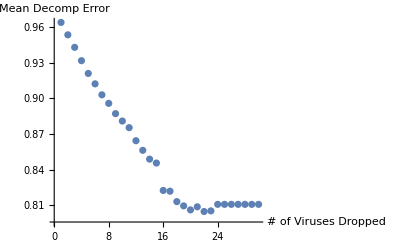

```mathematica
(*resRemovingMultipleAbs=Table[
{numAbsToRemove,Table[decomposeSerum[mixture,1,Delete[labelVirus,List/@First/@resRemovingAb[[;;numAbsToRemove]]],"RemoveHeadAbSignal"->True,"ShowMap"->False];decomposeGroundTruthError[mixture,Delete[labelVirus,List/@First/@resRemovingAb[[;;numAbsToRemove]]]]/mapError,{mixture,mixtures2AbStem}]},{numAbsToRemove,30}];
Iconize[resRemovingMultipleAbs,"Decompositions using a Smaller Virus Panel"]*)
resRemovingMultipleAbs=;
ListPlot[Mean/@Last/@resRemovingMultipleAbs,AxesLabel->{"# of Viruses Dropped","Mean Decomp Error"}]
```

Therefore, in our decompositions of all monoclonal stem antibodies and stem mixtures (Figure S10), we only use neutralization measurements from the following 31 viruses:

```mathematica
virusesForDecomp=SortBy[Delete[labelVirus,List/@First/@resRemovingAb[[;;20]]],{StringTake[#,{1,4}],virusYear@#}&]
```

{H1N1 A/WSN/1933,H1N1 A/Puerto Rico/8/1934,H1N1 A/Weiss/1943,H1N1 A/Malaysia/1954,H1N1 A/Kiev/1/1957,H1N1 A/Beijing/262/1995,H1N1 A/New Caledonia/20/1999,H1N1 A/Solomon Islands/03/2006,H1N1 A/New York/08-1326/2008,H1N1 A/California/07/2009,H1N1 A/Boston/YGA-01050/2012,H1N1 A/Idaho/07/2018,H3N2 A/Aichi/2/1968,H3N2 A/Philippines/2/1982,H3N2 A/Colorado/2/1986,H3N2 A/Sichuan/2/1987,H3N2 A/Beijing/353/1989,H3N2 A/Johannesburg/33/1994,H3N2 A/Brisbane/8/1996,H3N2 A/Sydney/5/1997,H3N2 A/Moscow/10/1999,H3N2 A/Fujian/411/2002,H3N2 A/California/07/2004,H3N2 A/Perth/16/2009,H3N2 A/Indiana/10/2011,H3N2 A/Victoria/361/2011,H3N2 A/Texas/50/2012,H3N2 A/Switzerland/9715293/2013,H3N2 A/Hong Kong/4801/2014,H3N2 A/Singapore/INFIMH-160019/2016,H3N2 A/Perth/1008/2019}

Here are the 20 viruses that we excluded from our decomposition analysis:

```mathematica
Extract[labelVirus,List/@First/@resRemovingAb[[;;20]]]
```

{H1N1 A/New Jersey/8/1976,H1N1 A/New York/638/1995,H3N2 A/Texas/1/1977,H3N2 A/Bilthoven/1761/1976,H3N2 A/Brisbane/10/2007,H3N2 A/Shandong/9/1993,H1N1 A/USSR/90/1977,H3N2 A/Netherlands/209/1980,H1N1 A/Shanghai/8/1996,H3N2 A/Wisconsin/67/2005,H1N1 A/Fort Monmouth/1/1947,H1N1 A/Canterbury/76/2000,H1N1 A/New York/653/1996,H1N1 A/Memphis/4/1987,H1N1 A/Chile/1/1983,H1N1 A/New York/146/2000,H1N1 A/Michigan/45/2015,H3N2 A/Port Chalmers/1/1973,H1N1 A/Morioka/3/2005,H3N2 A/Shanghai/11/1987}

#### Canned: Decomposing Monoclonal Antibodies and Antibody Mixtures

Using the full Creanga virus panel to decompose the monoclonal antibodies and antibody mixtures. To speed up Initialization, the code below is commented and the results have been canned.

To compute the number of antibodies in the mixture, we use the option "ErrorComputedAgainst"->"Input" to specify that the error of the decompositions is computed against the input data (i.e. the mixture IC_50s)

In the rest of the manuscript, we want to quantify the error of the resulting decomposition against measurements from the stem antibodies within the mixture (using the default option "ErrorComputedAgainst"->"GroundTruth"). Hence, after the appropriate number of antibodies is found, each decomposition is rerun with this new option

```mathematica
(*Clear[decomposeError]
cannedDecomposition=Table[
PrintTemporary[antibody];
(* Decompose using the input data to determine the number of antibodies *)
decomposeSerum[antibody,Automatic,virusesForDecomp,"RemoveHeadAbSignal"->True,"ShowMap"->False,"ErrorComputedAgainst"->"Input"];
(* Compare decomposition to the ground truth (i.e. a stem antibody mixture containing those antibodies) *)
decomposeSerum[antibody,Automatic,virusesForDecomp,"RemoveHeadAbSignal"->True,"ShowMap"->False,"ErrorComputedAgainst"->"GroundTruth"];
{antibody,{Length@mixtureAbCoord,mapError},mixtureAbCoord,mixtureAbRatio}
,{antibody,Join[mixtures1AbStem,mixtures2AbStem,mixtures2AbHeadStem,mixtures3AbHeadStem]}]*)
cannedDecomposition={{{{},{"315-02-1F07"}},{1,3.0597224162488055},{{-2.138076559019046,-0.5420055790611648}},{1}},{{{},{"315-02-1H01"}},{1,2.409827758029003},{{2.1336665484606874,0.3517853775763282}},{1}},{{{},{"315-09-1B12"}},{1,1.5053268764777068},{{-1.7241686180245885,-0.4103734143059339}},{1}},{{{},{"315-19-1D12"}},{1,1.8094699987598482},{{-1.8445993184874967,-1.1206596020783315}},{1}},{{{},{"315-23-1C09"}},{2,16.00088014335733},{{1.474118532851982,-2.321181083149912},{0.14702982202336679,2.5978506994558157}},{0.9,0.1}},{{{},{"315-27-1C08"}},{1,1.4201104535506444},{{-1.863930438244253,-0.5977607166472834}},{1}},{{{},{"315-53-1A09"}},{1,2.0943474294785998},{{-1.541879021245837,-0.8124161428693427}},{1}},{{{},{"315-53-1B06"}},{1,2.4902413303224553},{{0.5804972216581605,-0.6572702451417834}},{1}},{{{},{"315-53-1F12"}},{1,2.183460171032175},{{0.6017592295639176,-0.5757168916489878}},{1}},{{{},{"315-55-1E08"}},{1,1.8693747937700238},{{0.8415358343794846,-1.5940047416883876}},{1}},{{{},{"315-55-1E11"}},{1,1.8152553663897824},{{0.6670547541838813,-0.43939908388119503}},{1}},{{{},{"CR6261"}},{1,1.8036577462360486},{{2.2679991764446275,0.007504703507153185}},{1}},{{{},{"CR8020"}},{1,1.7353965017871473},{{-2.1889393891174436,-0.35960929316494744}},{1}},{{{},{"CR9114"}},{1,1.8696125043197998},{{1.0214320013616234,-0.19340846984293983}},{1}},{{{},{"MEDI8852"}},{1,1.8250061396944264},{{0.24675981943272784,-0.20616672698587457}},{1}},{{{},{"CT149"}},{1,6.6586760627634005},{{-1.1548288784542102,-1.540495789309516}},{1}},{{{},{"FI6v3"}},{2,2.3836799647575724},{{1.3033475271974242,0.6093832760975005},{-1.6652311326214997,-0.6261474046695508}},{0.2818057784976821,0.7181942215023178}},{{{},{"02-1D09"}},{1,2.2021515504909783},{{-1.6060979680690168,-1.2907423535003884}},{1}},{{{},{"04-1D10"}},{1,1.6501365640102728},{{-1.671791779637723,-1.2951027405738929}},{1}},{{{},{"21-1A10"}},{2,11.197144932258299},{{3.258078286105624,2.32849580129764},{-1.233134280501389,0.09358334738480818}},{0.9,0.1}},{{{},{"15-5E04"}},{1,3.5020711360068644},{{-1.5055149372261296,-0.8238178338225889}},{1}},{{{},{"55-1D06"}},{1,2.304965635066787},{{1.2803429769175716,-0.6148702452245531}},{1}},{{{},{"02-1B02"}},{1,1.5413852262309595},{{2.0751463898754032,-0.2121281209785165}},{1}},{{{},{"22-1B08"}},{2,2.223426484767585},{{-0.9946726950500464,-2.1798968966176324},{-0.039149753109948005,2.735061587965107}},{0.9,0.1}},{{{},{"54-4H03"}},{1,2.9369786680890853},{{-0.9345174378067342,-1.4910837152446517}},{1}},{{{},{"13-1B02"}},{1,3.3802299202860047},{{-1.0297442254904128,-0.7916711654813431}},{1}},{{{},{"58-6F03"}},{1,2.468722723740482},{{1.5161373782744392,-0.4848132087349757}},{1}},{{{},{"315-02-1H01","315-27-1C08"}},{2,1.469052312565823},{{-1.5288719411457772,-0.3887826746391836},{2.0741732315681563,0.5894839591346742}},{0.3068717760092408,0.6931282239907592}},{{{},{"CR6261","CR8020"}},{2,2.142390226182606},{{-2.371247115903975,-1.008081027738899},{1.0500987883567727,0.5965917898410202}},{0.9,0.1}},{{{},{"21-1A10","CR9114"}},{2,1.2778045310066728},{{1.1046851919094807,0.25363832922894286},{-0.8625151240197967,-1.0030903297077227}},{0.27820157923937766,0.7217984207606223}},{{{},{"15-5E04","CR9114"}},{2,1.1972756725487033},{{1.000785566614582,0.3551927501231966},{-1.6106917352235575,-1.0736459968562848}},{0.24467501382808704,0.7553249861719129}},{{{"C05"},{"CR6261"}},{1,2.9388742872502185},{{2.1757304020494392,1.4369956270576314}},{1}},{{{"C05"},{"MEDI8852"}},{2,3.5477871081243406},{{1.9241944368693251,1.6879662025913735},{-1.5764257269333968,-0.45281647306192574}},{0.9,0.1}},{{{"CH65"},{"CR6261"}},{1,2.6461439985717745},{{2.4864513501152694,0.7718931995465994}},{1}},{{{"F005-126"},{"CR8020"}},{1,1.7692334058917325},{{-2.2192156146705564,-0.6931531301557369}},{1}},{{{"F045-092"},{"CR8020"}},{1,5.147545789208866},{{-2.2101478370643886,0.441381702046172}},{1}},{{{"310-33-1G04"},{"58-6F03"}},{1,5.37596887357985},{{2.3193808168976826,-0.28867159119042746}},{1}},{{{"CH65"},{"02-1B02"}},{1,1.6991039197747337},{{2.4593207677269455,-0.052192532144368683}},{1}},{{{"5J8","C05"},{"FI6v3"}},{1,4.196194198329916},{{0.580992525031241,0.9348385350505518}},{1}},{{{"C05","F045-092"},{"315-09-1B12"}},{1,6.185659383900968},{{-2.228849001610743,1.0570102583468428}},{1}},{{{"C05"},{"CR6261","CR8020"}},{2,3.3298059623142544},{{-2.09077311062748,-1.4468612033266444},{1.4730180716627455,1.2712489231378308}},{0.718473828222245,0.28152617177775496}}};
```

```mathematica
(* Canned results of the form {Serum, {# of Antibodies, Decomposition Error}, {Predicted Coordinates}, {Predicted Mixture Fractions}}. 
 [1] 'Mixture' takes the form {{Head Antibodies}, {Stem Antibodies}}
 [2] # of Antibodies takes the form {Predicted # of Head antibodies, Predicted # of Stem antibodies}
[3] Decomposition error represents the average fold-difference between the measured and map Subscript[IC, 50] s
[4] Predicted coordinates give (x,y) positions for each stem antibody predicted by decomposition
[5] Predicted mixture fractions give the fraction of each mixture occupied by the antibody
 *)
With[{cannedDecomposition=cannedDecomposition},
(
decomposeError[#[[1]],virusesForDecomp]=#[[2]];
decomposeAbCoords[#[[1]]]=#[[3]];
decomposeAbRatios[#[[1]]]=#[[4]];
)&/@cannedDecomposition
];
```